### DMRG ⟨σσ⟩

```mathematica
L=40;
data$temp=Riffle[Table[i,{i,1,20}],0.5293860225014412/0.2999304743017528{0.6319967765174531,0.48857715985398276,0.4389694564183839,0.4068674461684058,0.38490307923708506,0.36804948915813773,0.3549127962952205,0.34421083732363467,0.3354457859814165,0.3281218922228694,0.32201021438733124,0.3168744551810463,0.3125946504591138,0.3090442867441435,0.306156877003633,0.30386097173698334,0.3021205855040111,0.30089617541077623,0.30017216869167634,0.2999304743017528}]//Partition[#,2]&;
data$temp2={(L/π)Sin[#[[1]] π/L],#[[2]]}&/@%//N;
```

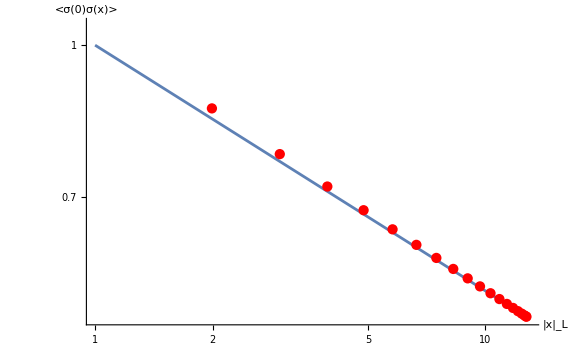

```mathematica
g=Show[LogLogPlot[1/y^(1/4),{y,1,13},PlotRange->{Automatic,{0,1.05}}],ListLogLogPlot[data$temp2[[2;;20]], PlotStyle->Red],AxesLabel->{"|x|_L","<σ(0)σ(x)>"},ImageSize->Large,AxesStyle->Large]
```

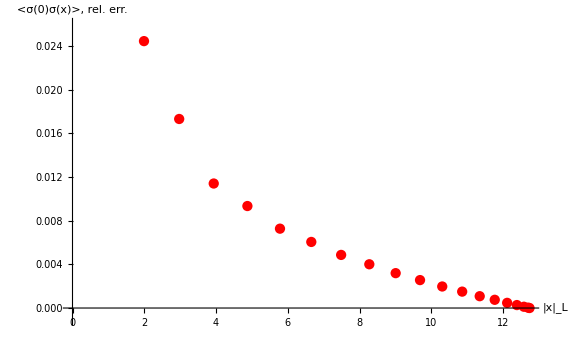

```mathematica
g1=({#[[1]],Abs[#[[2]]/(1/(#[[1]])^(1/4))-1]}&/@data$temp2//ListPlot[#,AxesLabel->{"|x|_L","<σ(0)σ(x)>, rel. err."},PlotRange->{-0.001,0.026},PlotStyle->Red,ImageSize->Large,AxesStyle->Large]&)
```

```mathematica
data$temp2
```

{{0.998972,1.11549},{1.99179,0.862353},{2.97232,0.774794},{3.93453,0.718133},{4.87248,0.679365},{5.78039,0.649618},{6.65266,0.626431},{7.48391,0.607542},{8.26903,0.592072},{9.00316,0.579145},{9.68179,0.568357},{10.3007,0.559293},{10.8562,0.551739},{11.3446,0.545472},{11.7632,0.540376},{12.1092,0.536323},{12.3806,0.533252},{12.5756,0.531091},{12.6931,0.529813},{12.7324,0.529386}}

```mathematica
√(((L/π)Sin[20 π/L])^(-1/4)/0.2999304743017528)
```

1.32854

```mathematica
SetDirectory[NotebookDirectory[]];
Export["fig-sigma-sigma.pdf",g]
```

fig-sigma-sigma.pdf

```mathematica
SetDirectory[NotebookDirectory[]];
Export["fig-sigma-sigma-error.pdf",g1]
```

fig-sigma-sigma-error.pdf

### DMRG ⟨σσ⟩ at Ω/C_6=0.18, Δ/C_6=0.178, the disordered phase

```mathematica
L=40;
data$temp=Riffle[Table[i,{i,1,20}],0.5293860225014412/0.2999304743017528{-0.6043967314873749,0.44782770327693044,-0.3892114081021346,0.35021637281464946,-0.32264287571885064,0.30111771232462864,-0.28401456519883095,0.2699189162200197,-0.25822911672108145,0.24838331818295625,-0.24009659976991707,0.23309507567606327,-0.2272255993909936,0.22233897781638667,-0.21834830204216965,0.2151684136880789,-0.21275104328014682,0.21104909514385084,-0.21004055068996658,0.20970457316162788}]//Partition[#,2]&;
data$temp2={(L/π)Sin[#[[1]] π/L],#[[2]]}&/@%//N;
```

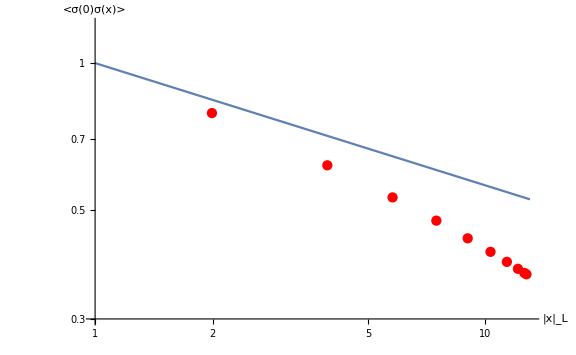

```mathematica
g=Show[LogLogPlot[1/y^(1/4),{y,1,13},PlotRange->{Automatic,{0.3,1.2}}],ListLogLogPlot[data$temp2[[2;;20]], PlotStyle->Red],AxesLabel->{"|x|_L","<σ(0)σ(x)>"},ImageSize->Large,AxesStyle->Large]
```

### DMRG ⟨σσ⟩ at Ω/C_6=0.18, Δ/C_6=0.19, the symmetry breaking phase

```mathematica
L=40;
data$temp=Riffle[Table[i,{i,1,20}],0.5293860225014412/0.2999304743017528{-0.6566719123041851,0.5250750002984526,-0.4836040288692108,0.45775015392037094,-0.4408804651044923,0.42828169158992985,-0.4187639368800001,0.41116570018820503,-0.40507956122179406,0.40007038213780177,-0.39595757579466984,0.39253953625800175,-0.38972466613635026,0.38740760710471844,-0.3855390455065105,0.384060568321491,-0.38294623579190806,0.3821640170204534,-0.38170323751239,0.3815490713011507}]//Partition[#,2]&;
data$temp2={(L/π)Sin[#[[1]] π/L],#[[2]]}&/@%//N;
```

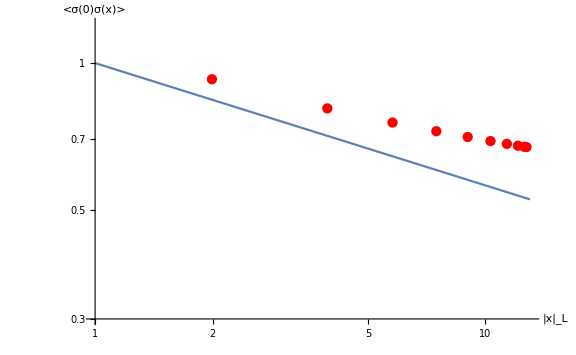

```mathematica
g=Show[LogLogPlot[1/y^(1/4),{y,1,13},PlotRange->{Automatic,{0.3,1.2}}],ListLogLogPlot[data$temp2[[2;;20]], PlotStyle->Red],AxesLabel->{"|x|_L","<σ(0)σ(x)>"},ImageSize->Large,AxesStyle->Large]
```

### DMRG ⟨ϵϵ⟩

```mathematica
L=40;
data$temp=Riffle[Table[i,{i,1,20}],((L/π)Sin[20 π/L])^-2/0.0014561975206714428{0.21036470881938163,0.10380767427270507,0.05828720083840144,0.01953085890256981,0.011722953664760671,0.007745839371092772,0.005711886789146192,0.0044059234222894594,0.0035721543520163546,0.002980672364247927,0.0025638868545783955,0.00225201963193139,0.002021572756812834,0.0018451766607710807,0.0017134080794678208,0.001613788879077288,0.0015425862960726233,0.0014935649314098964,0.0014657867406172587,0.0014561975206714428}]//Partition[#,2]&;
data$temp2={(L/π)Sin[#[[1]] π/L],#[[2]]}&/@%//N;
```

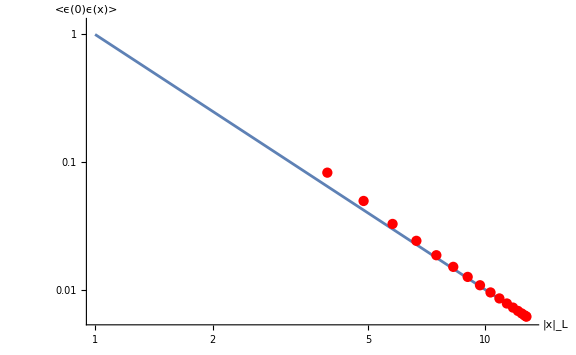

```mathematica
g=Show[LogLogPlot[1/y^2,{y,1,13},PlotRange->{Automatic,{0,1.2}}],ListLogLogPlot[data$temp2[[4;;20]], PlotStyle->Red],AxesLabel->{"|x|_L","<ϵ(0)ϵ(x)>"},ImageSize->Large,AxesStyle->Large]
```

```mathematica
√(((L/π)Sin[20 π/L])^-2/0.0014561975206714428)
```

2.05816

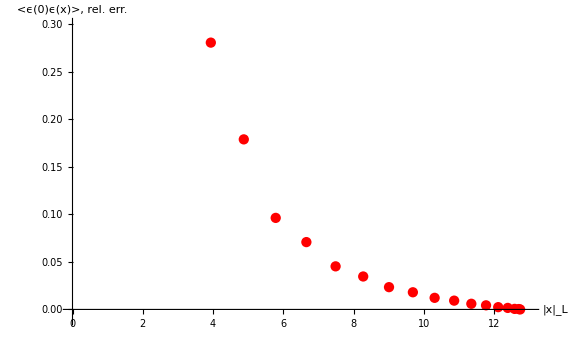

```mathematica
g1={#[[1]],Abs[#[[2]]/(1/(#[[1]])^2)-1]}&/@data$temp2⟦4;;All⟧//ListPlot[#,AxesLabel->{"|x|_L","<ϵ(0)ϵ(x)>, rel. err."},PlotRange->{{0,13},{-0.01,0.3}},PlotStyle->Red,ImageSize->Large,AxesStyle->Large]&
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/slava/Personal/----Fisica----/_Projects/Fork/2025 three_point_function_CFT

```mathematica
Export["fig-eps-eps.pdf",g]
Export["fig-eps-eps-error.pdf",g1]
```

fig-eps-eps.pdf

fig-eps-eps-error.pdf

### DMRG ⟨σσϵ⟩

```mathematica
data$temp=Abs/@{0.12437853107744494, -0.10918628313480952, 0.10380758320196523, -0.10437485622633542, 0.10181807304395053, -0.10023129144748673, 0.09827489616527886, -0.09682192706784315, 0.095382787505695, -0.09426830682280679, 0.0932482893590145, -0.09246478827778926, 0.09179446036934762, -0.09131266592769169, 0.09094914413849978, -0.09074816663718277, 0.09066974634279802, -0.0907419551749113, 0.09094481112578084, -0.09129745426804425, 0.09179554197773128, -0.09245344575569024, 0.09328168280439571, -0.09429314343979764, 0.09551578857094681, -0.09696508908969237, 0.09869372404563323, -0.10072752928921519, 0.10316043330404945, -0.10604840303557848, 0.10956610717780911, -0.1138625901028327, 0.11930337537172636, -0.12639319219383255, 0.1361106885025227, -0.15108371441060794, 0.17633364136277443, -0.2655927392616145, 0.3174038878073508, -0.10918628313480952, 0.05368380312369995, -0.05003900112383972, 0.058196557280829425, -0.06097218962568935, 0.06200030167124257, -0.06221074131816348, 0.06220765501055796, -0.0620170429597612, 0.06183813062734937, -0.06163419726389891, 0.0614929970119651, -0.06138264322374346, 0.061348712116679124, -0.06137012059037291, 0.061473485053079806, -0.06164707852415924, 0.061907952463085274, -0.06225260283778644, 0.06269306642446311, -0.06323397519598374, 0.06388503324873043, -0.06466017015835071, 0.06556907768023622, -0.06663827395118226, 0.06788055343582813, -0.06934212916272522, 0.07104507287173266, -0.07307077725657692, 0.07546621713227043, -0.07838546361382054, 0.08194961957552897, -0.08649291484424608, 0.09241399897047382, -0.10064931316794126, 0.11323109688401985, -0.13505220665577994, 0.20721616027994505, -0.2654537152211821, 0.10380758320196523, -0.05003900112383972, 0.010921369204204261, -0.014408179894977132, 0.01953111684573793, -0.02212185930126251, 0.023655338035249815, -0.02461200855475964, 0.025278069429279505, -0.02576071915659709, 0.026143197338265887, -0.02646301476280229, 0.026751885617137573, -0.02702661166862991, 0.02730208396104019, -0.02758790746263175, 0.027892648502799218, -0.02822347058305118, 0.028586738946455276, -0.028989544867270713, 0.02943823699281524, -0.029941449589369895, 0.03050707116919091, -0.031147374616196755, 0.03187363154262569, -0.03270524904130402, 0.03366015254383807, -0.034772090576570436, 0.03607266780673995, -0.037627425048389083, 0.03949903839463207, -0.041835934093411485, 0.044785745380695886, -0.048775423108706674, 0.054267492865111434, -0.0631891993787549, 0.0784177295209785, -0.13513895680107355, 0.17630767889893129, -0.10437485622633542, 0.058196557280829425, -0.014408179894977132, 0.0070382116416591, -0.008371906108199852, 0.011717511291539131, -0.013726423846409047, 0.01499988669421198, -0.01590477113396483, 0.01657863229060795, -0.017113681479994133, 0.017559056502730472, -0.017948363478002844, 0.018304131133250807, -0.018641685589571428, 0.018973596262692172, -0.0193085503184748, 0.01965512425805105, -0.020019609197160185, 0.02040943382737178, -0.020830729330849618, 0.0212914792607498, -0.021799231827864987, 0.022364475147984595, -0.02299790266540195, 0.023715531594850514, -0.02453424646106054, 0.025481678607986977, -0.026587484577939594, 0.027905719699897323, -0.02949476230641273, 0.03147877591654947, -0.033994523246569916, 0.037405337161162885, -0.04213584945031968, 0.04985964066081792, -0.0631825256136794, 0.11330422270626014, -0.1510440029523342, 0.10181807304395053, -0.06097218962568935, 0.01953111684573793, -0.008371906108199852, 0.003906260879489259, -0.005365413656318449, 0.007745902725498392, -0.00931200225724946, 0.010400669990622865, -0.01121203539733762, 0.011854430249760314, -0.01238358430556789, 0.012840823681979065, -0.013249313245797008, 0.013628492912111986, -0.013990638626506922, 0.014346653053088824, -0.014704756220942227, 0.015072337328902305, -0.01545648689620039, 0.01586354156544692, -0.016301242156415905, 0.016776513220546428, -0.017299659290085492, 0.017879785595689167, -0.01853269369983353, 0.01927228939708939, -0.020125738217889662, 0.02111736854509122, -0.022299962858934843, 0.02372184276925393, -0.025503050814966132, 0.02775901248886508, -0.030837044242181467, 0.03510367214360072, -0.04214173711789027, 0.054267416935425285, -0.10072825263044033, 0.13607806897120778, -0.10023129144748673, 0.06200030167124257, -0.02212185930126251, 0.011717511291539131, -0.005365413656318449, 0.002951684247381624, -0.0038389522213922536, 0.005710544418828136, -0.006995515943984852, 0.007923827731260309, -0.008651884445996533, 0.009244915027438069, -0.009751572019219622, 0.010198401825294166, -0.010606915359542697, 0.010990891292766269, -0.011361987362108557, 0.01172912565523304, -0.012100037837429144, 0.012481990535333653, -0.012881393961069132, 0.013305822306277736, -0.013762093577791916, 0.01425994164202952, -0.01480820862980175, 0.015421549597119295, -0.016113370228903714, 0.01690870532889214, -0.0178308998524431, 0.0189286487675993, -0.020248162404519463, 0.021900622668209125, -0.02399615986456191, 0.026858102400991943, -0.0308351115441791, 0.03740905256089979, -0.04877314084886849, 0.09248884257943617, -0.12635585517957837, 0.09827489616527886, -0.06221074131816348, 0.023655338035249815, -0.013726423846409047, 0.007745902725498392, -0.0038389522213922536, 0.0020766609233634423, -0.0029379812002525486, 0.004405938598625727, -0.005480929436619662, 0.0062931080574906775, -0.0069485666321694945, 0.007500634334318161, -0.007982247301862071, 0.008417086378266448, -0.008820694043679146, 0.009205801176326951, -0.009581910721079313, 0.009957270515000657, -0.010339328523698496, 0.010734634813121964, -0.011150774375606732, 0.011594359771707134, -0.01207500910615684, 0.012601005066866094, -0.013186718204926055, 0.01384449069675231, -0.014598748756378808, 0.015470864270581215, -0.016508184666841653, 0.017753127977037403, -0.01931343790503545, 0.02129087305215428, -0.023997702551273887, 0.027758771357294886, -0.03399992740537294, 0.04478536667883414, -0.0865693595706268, 0.11926750625918617, -0.09682192706784315, 0.06220765501055796, -0.02461200855475964, 0.01499988669421198, -0.00931200225724946, 0.005710544418828136, -0.0029379812002525486, 0.001702323475866355, -0.0023217681772175693, 0.003571624555604575, -0.004499138049176363, 0.005220526640479816, -0.005820221388556789, 0.006335867362866932, -0.006796355484367114, 0.007218895220866229, -0.007617770469101838, 0.008003184060162408, -0.008383997206787308, 0.008767907847953487, -0.009161724709258046, 0.009573020348392415, -0.010008442056743108, 0.010477348842082713, -0.010987914493996115, 0.011553927284805246, -0.012187455168310286, 0.012911809748808428, -0.013747747042970548, 0.01474042730391466, -0.015930958844506994, 0.01742227701433817, -0.01931278802986929, 0.02190156024008527, -0.02550233333240302, 0.031483621007207946, -0.04183483505156585, 0.08202398316637546, -0.1138240084269639, 0.095382787505695, -0.0620170429597612, 0.025278069429279505, -0.01590477113396483, 0.010400669990622865, -0.006995515943984852, 0.004405938598625727, -0.0023217681772175693, 0.0013387147690281027, -0.0019354240008297244, 0.0029806837930386105, -0.0037965862264452903, 0.004448759694202347, -0.005003086411671488, 0.005490696657753977, -0.0059336445278211965, 0.0063472206575724555, -0.006743107895969009, 0.007130636036557492, -0.00751805916786385, 0.007912359276746902, -0.008321309793617978, 0.008751506607029403, -0.009212302870464352, 0.009711620226459874, -0.010263057880252195, 0.010878165698006925, -0.011579799538716438, 0.012387692594547493, -0.01334598339214291, 0.014493782502621195, -0.01593152368407467, 0.017753024458419014, -0.020249690854914088, 0.023721869435316196, -0.029500419908508473, 0.03949883618103863, -0.07846045447204063, 0.10952796697192424, -0.09426830682280679, 0.06183813062734937, -0.02576071915659709, 0.01657863229060795, -0.01121203539733762, 0.007923827731260309, -0.005480929436619662, 0.003571624555604575, -0.0019354240008297244, 0.001158279101953886, -0.001629393629231744, 0.0025636400196057257, -0.003296058828304489, 0.003895464259491337, -0.0044155192196652475, 0.004881111060162838, -0.005311499146885288, 0.005719323763630256, -0.0061151505896943695, 0.006507637105067808, -0.006904259931656359, 0.007312899497261543, -0.007740334536379418, 0.008195811775230388, -0.008687264355201419, 0.00922795335298734, -0.009829292014983627, 0.010513458387008288, -0.01129978587426195, 0.012231046981208478, -0.013345475768569684, 0.014740471496502422, -0.016507528382959897, 0.01892964963779064, -0.02229956158774037, 0.027910972032232202, -0.037626789262413904, 0.07554012373861167, -0.10600867754054302, 0.0932482893590145, -0.06163419726389891, 0.026143197338265887, -0.017113681479994133, 0.011854430249760314, -0.008651884445996533, 0.0062931080574906775, -0.004499138049176363, 0.0029806837930386105, -0.001629393629231744, 0.0009743675490514727, -0.0014324475249051405, 0.0022520493353726046, -0.00292115591336019, 0.0034795489741653823, -0.003973295365750276, 0.004423094836740308, -0.004845365695902821, 0.00525126674128418, -0.005650651694973449, 0.006051260432450605, -0.006461454281755354, 0.006888072260049458, -0.007340503288033706, 0.007826573247351752, -0.008359471113325335, 0.00895031839994229, -0.009620996499009542, 0.010390226530659963, -0.011300048807031943, 0.012387473785421736, -0.013748087425694274, 0.015470485228098739, -0.017832191068443123, 0.021117341196274415, -0.026593155718033726, 0.03607250691833067, -0.07314500797051428, 0.10312078625424392, -0.09246478827778926, 0.0614929970119651, -0.02646301476280229, 0.017559056502730472, -0.01238358430556789, 0.009244915027438069, -0.0069485666321694945, 0.005220526640479816, -0.0037965862264452903, 0.0025636400196057257, -0.0014324475249051405, 0.0008776505310481593, -0.0012633097650256635, 0.0020214534814966337, -0.002642038778761192, 0.003170460249356446, -0.0036453088006546323, 0.004084857492624822, -0.004503500320223887, 0.00491172296534753, -0.005318293075640293, 0.005731791644683043, -0.006159499681094192, 0.006610831481383056, -0.007093748417818875, 0.007621271090203295, -0.008204472398882088, 0.008864818097489515, -0.009620773374642837, 0.010513483830158423, -0.011579343921846492, 0.012911892221643767, -0.014598075685208685, 0.01690966966521232, -0.02012541750844121, 0.025487080989517713, -0.03477167890451078, 0.07111871862632164, -0.10068692093719846, 0.09179446036934762, -0.06138264322374346, 0.026751885617137573, -0.017948363478002844, 0.012840823681979065, -0.009751572019219622, 0.007500634334318161, -0.005820221388556789, 0.004448759694202347, -0.003296058828304489, 0.0022520493353726046, -0.0012633097650256635, 0.0007739777508179832, -0.0011535165935412102, 0.001845187774577111, -0.002429938238293148, 0.0029357977656468727, -0.003398117729453536, 0.003832366083847861, -0.00425216544987936, 0.004666716782923664, -0.005085551121403886, 0.005516115902485702, -0.0059682400832558775, 0.006449880444224002, -0.0069741558589142254, 0.007551970720156466, -0.008204649437437265, 0.008950276656928522, -0.00982949711294168, 0.010877910251533084, -0.012187738498565063, 0.013844000591885957, -0.01611448851646724, 0.019272130611573526, -0.024539845177089313, 0.03366004242384831, -0.06941606771931502, 0.0986531887056776, -0.09131266592769169, 0.061348712116679124, -0.02702661166862991, 0.018304131133250807, -0.013249313245797008, 0.010198401825294166, -0.007982247301862071, 0.006335867362866932, -0.005003086411671488, 0.003895464259491337, -0.00292115591336019, 0.0020214534814966337, -0.0011535165935412102, 0.0007202673276319112, -0.0010562706858839447, 0.001713336685461053, -0.0022713603309577495, 0.0027627223202815517, -0.0032181258645652393, 0.003652455713201408, -0.0040777493337766915, 0.004503977745502406, -0.004939484860661068, 0.005394218073146268, -0.0058765132195865806, 0.006399449487351709, -0.006974022497832829, 0.007621315160299176, -0.008359295174889071, 0.00922801348844683, -0.010262665435997239, 0.011554066306689507, -0.013186061452261777, 0.015422458448147889, -0.018532294645034093, 0.02372087982874011, -0.032704929583073625, 0.06795411985130648, -0.09692390771855827, 0.09094914413849978, -0.06137012059037291, 0.02730208396104019, -0.018641685589571428, 0.013628492912111986, -0.010606915359542697, 0.008417086378266448, -0.006796355484367114, 0.005490696657753977, -0.0044155192196652475, 0.0034795489741653823, -0.002642038778761192, 0.001845187774577111, -0.0010562706858839447, 0.0006586901211014923, -0.000993353029598117, 0.0016137912787249022, -0.002154024268761958, 0.002636542664889881, -0.0030908481461256096, 0.0035298674196032795, -0.0039663006941977694, 0.004408863412030344, -0.004868317126709147, 0.005353103521046325, -0.005876639661564643, 0.006449871727146181, -0.0070939195317234255, 0.007826527133942666, -0.008687454866905147, 0.009711386084998087, -0.010988227287408387, 0.012600523602041188, -0.014809269210080835, 0.017879501941196696, -0.02300335721934169, 0.031873482606154746, -0.06671202078317917, 0.0954746341344328, -0.09074816663718277, 0.061473485053079806, -0.02758790746263175, 0.018973596262692172, -0.013990638626506922, 0.010990891292766269, -0.008820694043679146, 0.007218895220866229, -0.0059336445278211965, 0.004881111060162838, -0.003973295365750276, 0.003170460249356446, -0.002429938238293148, 0.001713336685461053, -0.000993353029598117, 0.0006305383936876785, -0.0009398187421961749, 0.0015425440932291762, -0.0020717444683551025, 0.002552108196672093, -0.0030103564695293885, 0.0034600385436566908, -0.003912499292131159, 0.00437881519865306, -0.004868253050986406, 0.005394269592161103, -0.00596815749441721, 0.00661093971070274, -0.007340400281191091, 0.008195941159729233, -0.009212018111617221, 0.010477613370726392, -0.012074473002288293, 0.014260915807436965, -0.017299237820576657, 0.022369759097822538, -0.031147086433409545, 0.06564260964518115, -0.09425160978378797, 0.09066974634279802, -0.06164707852415924, 0.027892648502799218, -0.0193085503184748, 0.014346653053088824, -0.011361987362108557, 0.009205801176326951, -0.007617770469101838, 0.0063472206575724555, -0.005311499146885288, 0.004423094836740308, -0.0036453088006546323, 0.0029357977656468727, -0.0022713603309577495, 0.0016137912787249022, -0.0009398187421961749, 0.0005943263436559954, -0.0009060567376375034, 0.0014935630889729818, -0.0020189586025214585, 0.002502500358517132, -0.0029709439108676237, 0.0034364484570156536, -0.003912563375328003, 0.0044088920245210165, -0.0049396188052650055, 0.005516122004368793, -0.006159720714204591, 0.006888098698832472, -0.007740599479066477, 0.008751375584147089, -0.010008864812884263, 0.011593983990040213, -0.013763207381116194, 0.016776176868746755, -0.02180456938693968, 0.030506884453553075, -0.06473384827307074, 0.09324021498830103, -0.0907419551749113, 0.061907952463085274, -0.02822347058305118, 0.01965512425805105, -0.014704756220942227, 0.01172912565523304, -0.009581910721079313, 0.008003184060162408, -0.006743107895969009, 0.005719323763630256, -0.004845365695902821, 0.004084857492624822, -0.003398117729453536, 0.0027627223202815517, -0.002154024268761958, 0.0015425440932291762, -0.0009060567376375034, 0.0005838983973645637, -0.0008833439002719895, 0.0014657724396027663, -0.0019935510675876673, 0.0024868427769091607, -0.0029709925510652928, 0.003460096805609905, -0.003966317493693505, 0.004504051853435175, -0.005085493537165277, 0.005731962768171657, -0.00646145566455873, 0.007313153353460843, -0.008321176592174843, 0.009573437551724575, -0.011150391231804049, 0.013306907943322954, -0.01630082904041207, 0.021296697062517248, -0.029941163152444526, 0.06395859667952766, -0.0924117994540811, 0.09094481112578084, -0.06225260283778644, 0.028586738946455276, -0.020019609197160185, 0.015072337328902305, -0.012100037837429144, 0.009957270515000657, -0.008383997206787308, 0.007130636036557492, -0.0061151505896943695, 0.00525126674128418, -0.004503500320223887, 0.003832366083847861, -0.0032181258645652393, 0.002636542664889881, -0.0020717444683551025, 0.0014935630889729818, -0.0008833439002719895, 0.000565242067869787, -0.000870879987385652, 0.0014561943702519852, -0.0019933333002551228, 0.0025025231644632356, -0.003010388852196621, 0.0035299125830241776, -0.004077853715626598, 0.004666719155065224, -0.005318514110418718, 0.006051330550330961, -0.006904611368144266, 0.007912335689592804, -0.009162255811906297, 0.01073438073756891, -0.012882600527346987, 0.015863203806391443, -0.02083598100013564, 0.02943800855042297, -0.06330764896799507, 0.09175399646295189, -0.09129745426804425, 0.06269306642446311, -0.028989544867270713, 0.02040943382737178, -0.01545648689620039, 0.012481990535333653, -0.010339328523698496, 0.008767907847953487, -0.00751805916786385, 0.006507637105067808, -0.005650651694973449, 0.00491172296534753, -0.00425216544987936, 0.003652455713201408, -0.0030908481461256096, 0.002552108196672093, -0.0020189586025214585, 0.0014657724396027663, -0.000870879987385652, 0.0005694481007038228, -0.0008738300109510114, 0.001465790727495051, -0.002019222388583661, 0.0025521911191569054, -0.003090947040396156, 0.0036525785131889233, -0.004252181081086831, 0.004911886107881879, -0.005650658441048596, 0.006507950492232851, -0.007518018722430395, 0.008768430139387228, -0.010339083034453874, 0.012483204855338445, -0.015456119757032465, 0.020414607221736773, -0.0289892448721138, 0.06276667696787556, -0.09125587974365683, 0.09179554197773128, -0.06323397519598374, 0.02943823699281524, -0.020830729330849618, 0.01586354156544692, -0.012881393961069132, 0.010734634813121964, -0.009161724709258046, 0.007912359276746902, -0.006904259931656359, 0.006051260432450605, -0.005318293075640293, 0.004666716782923664, -0.0040777493337766915, 0.0035298674196032795, -0.0030103564695293885, 0.002502500358517132, -0.0019935510675876673, 0.0014561943702519852, -0.0008738300109510114, 0.000565146003751223, -0.0008803874150715809, 0.0014935862337403182, -0.00207158931391813, 0.002636604397120422, -0.0032182197540517894, 0.0038324068399614207, -0.0045036624287361025, 0.005251299016258708, -0.006115508326554085, 0.0071306503542914405, -0.008384583100771342, 0.009957118236238748, -0.012101366426203256, 0.01507207989338311, -0.020024863906914814, 0.028586521775160308, -0.06232632610577242, 0.09090340657930908, -0.09245344575569024, 0.06388503324873043, -0.029941449589369895, 0.0212914792607498, -0.016301242156415905, 0.013305822306277736, -0.011150774375606732, 0.009573020348392415, -0.008321309793617978, 0.007312899497261543, -0.006461454281755354, 0.005731791644683043, -0.005085551121403886, 0.004503977745502406, -0.0039663006941977694, 0.0034600385436566908, -0.0029709439108676237, 0.0024868427769091607, -0.0019933333002551228, 0.001465790727495051, -0.0008803874150715809, 0.000584105913209245, -0.0009090773522883722, 0.0015426088601773456, -0.002154312888809208, 0.0027628405964553746, -0.0033981915923946052, 0.0040850031072430905, -0.004845368865342057, 0.005719614923894325, -0.006743055475994822, 0.008003706920027194, -0.009581724842866379, 0.011730430213748337, -0.014704459423624174, 0.01966031516893511, -0.028223191796976226, 0.061981648180876134, -0.09070065270575756, 0.09328168280439571, -0.06466017015835071, 0.03050707116919091, -0.021799231827864987, 0.016776513220546428, -0.013762093577791916, 0.011594359771707134, -0.010008442056743108, 0.008751506607029403, -0.007740334536379418, 0.006888072260049458, -0.006159499681094192, 0.005516115902485702, -0.004939484860661068, 0.004408863412030344, -0.003912499292131159, 0.0034364484570156536, -0.0029709925510652928, 0.0025025231644632356, -0.002019222388583661, 0.0014935862337403182, -0.0009090773522883722, 0.0005940189750097115, -0.0009367804726919839, 0.0016138062660331516, -0.0022711985901542105, 0.0029358104106274275, -0.0036454128559104356, 0.004423101000204862, -0.005311755905091947, 0.006347148339990267, -0.007618289297865326, 0.00920564756868717, -0.011363344669002795, 0.014346440041058693, -0.01931383396290702, 0.027892471778804273, -0.061720906329468965, 0.09062868565990775, -0.09429314343979764, 0.06556907768023622, -0.031147374616196755, 0.022364475147984595, -0.017299659290085492, 0.01425994164202952, -0.01207500910615684, 0.010477348842082713, -0.009212302870464352, 0.008195811775230388, -0.007340503288033706, 0.006610831481383056, -0.0059682400832558775, 0.005394218073146268, -0.004868317126709147, 0.00437881519865306, -0.003912563375328003, 0.003460096805609905, -0.003010388852196621, 0.0025521911191569054, -0.00207158931391813, 0.0015426088601773456, -0.0009367804726919839, 0.0006309952145692488, -0.0009965153744734803, 0.001713402180019065, -0.002430184610493042, 0.0031705878151358654, -0.003973328509818201, 0.0048813072700921, -0.0059334867197117945, 0.007219303282553923, -0.00882045298576287, 0.010992169811473086, -0.01399036423814436, 0.018978834041736132, -0.027587683767487423, 0.061547333597931596, -0.09070737901823124, 0.09551578857094681, -0.06663827395118226, 0.03187363154262569, -0.02299790266540195, 0.017879785595689167, -0.01480820862980175, 0.012601005066866094, -0.010987914493996115, 0.009711620226459874, -0.008687264355201419, 0.007826573247351752, -0.007093748417818875, 0.006449880444224002, -0.0058765132195865806, 0.005353103521046325, -0.004868253050986406, 0.0044088920245210165, -0.003966317493693505, 0.0035299125830241776, -0.003090947040396156, 0.002636604397120422, -0.002154312888809208, 0.0016138062660331516, -0.0009965153744734803, 0.0006581126700623028, -0.0010530273792449612, 0.001845143828739322, -0.0026418625390856524, 0.0034795125802098924, -0.004415648513623594, 0.0054905271071942555, -0.0067967401629746675, 0.008416873375606338, -0.010608235030032448, 0.01362825280895208, -0.018646956932853186, 0.027301901593253013, -0.06144406788171027, 0.09090866980309822, -0.09696508908969237, 0.06788055343582813, -0.03270524904130402, 0.023715531594850514, -0.01853269369983353, 0.015421549597119295, -0.013186718204926055, 0.011553927284805246, -0.010263057880252195, 0.00922795335298734, -0.008359471113325335, 0.007621271090203295, -0.0069741558589142254, 0.006399449487351709, -0.005876639661564643, 0.005394269592161103, -0.0049396188052650055, 0.004504051853435175, -0.004077853715626598, 0.0036525785131889233, -0.0032182197540517894, 0.0027628405964553746, -0.0022711985901542105, 0.001713402180019065, -0.0010530273792449612, 0.0007210154126281004, -0.0011568940771774603, 0.0020215301202918872, -0.00292138014144698, 0.003895614666147822, -0.005002938947902579, 0.006336195103317052, -0.007982009777849873, 0.010199691203532119, -0.01324901677540226, 0.018309325859074313, -0.027026330266255134, 0.06142269713154509, -0.09127265067395966, 0.09869372404563323, -0.06934212916272522, 0.03366015254383807, -0.02453424646106054, 0.01927228939708939, -0.016113370228903714, 0.01384449069675231, -0.012187455168310286, 0.010878165698006925, -0.009829292014983627, 0.00895031839994229, -0.008204472398882088, 0.007551970720156466, -0.006974022497832829, 0.006449871727146181, -0.00596815749441721, 0.005516122004368793, -0.005085493537165277, 0.004666719155065224, -0.004252181081086831, 0.0038324068399614207, -0.0033981915923946052, 0.0029358104106274275, -0.002430184610493042, 0.001845143828739322, -0.0011568940771774603, 0.0007730236345801562, -0.0012597722146841359, 0.002251986864379078, -0.003295908006370711, 0.004448571327158242, -0.0058205047206002355, 0.007500448368775415, -0.009752916862363755, 0.012840580865357002, -0.017953593996571416, 0.026751576944292338, -0.06145665548671041, 0.09175482494578834, -0.10072752928921519, 0.07104507287173266, -0.034772090576570436, 0.025481678607986977, -0.020125738217889662, 0.01690870532889214, -0.014598748756378808, 0.012911809748808428, -0.011579799538716438, 0.010513458387008288, -0.009620996499009542, 0.008864818097489515, -0.008204649437437265, 0.007621315160299176, -0.0070939195317234255, 0.00661093971070274, -0.006159720714204591, 0.005731962768171657, -0.005318514110418718, 0.004911886107881879, -0.0045036624287361025, 0.0040850031072430905, -0.0036454128559104356, 0.0031705878151358654, -0.0026418625390856524, 0.0020215301202918872, -0.0012597722146841359, 0.0008788648854634949, -0.0014362156323652767, 0.0025637608969795974, -0.003796702024169813, 0.005220861012860175, -0.0069484325614776535, 0.009246235116064242, -0.012383306928464136, 0.01756419774033759, -0.026462583340733196, 0.06156708972754618, -0.09242584259877125, 0.10316043330404945, -0.07307077725657692, 0.03607266780673995, -0.026587484577939594, 0.02111736854509122, -0.0178308998524431, 0.015470864270581215, -0.013747747042970548, 0.012387692594547493, -0.01129978587426195, 0.010390226530659963, -0.009620773374642837, 0.008950276656928522, -0.008359295174889071, 0.007826527133942666, -0.007340400281191091, 0.006888098698832472, -0.00646145566455873, 0.006051330550330961, -0.005650658441048596, 0.005251299016258708, -0.004845368865342057, 0.004423101000204862, -0.003973328509818201, 0.0034795125802098924, -0.00292138014144698, 0.002251986864379078, -0.0014362156323652767, 0.0009728628947755516, -0.0016253812986176453, 0.0029805124691149776, -0.004499161393078905, 0.006292960359876659, -0.008653189497472895, 0.01185421893876057, -0.017118871207737713, 0.02614274402396015, -0.0617084081991366, 0.09320996180683262, -0.10604840303557848, 0.07546621713227043, -0.037627425048389083, 0.027905719699897323, -0.022299962858934843, 0.0189286487675993, -0.016508184666841653, 0.01474042730391466, -0.01334598339214291, 0.012231046981208478, -0.011300048807031943, 0.010513483830158423, -0.00982949711294168, 0.00922801348844683, -0.008687454866905147, 0.008195941159729233, -0.007740599479066477, 0.007313153353460843, -0.006904611368144266, 0.006507950492232851, -0.006115508326554085, 0.005719614923894325, -0.005311755905091947, 0.0048813072700921, -0.004415648513623594, 0.003895614666147822, -0.003295908006370711, 0.0025637608969795974, -0.0016253812986176453, 0.0011601687549058607, -0.0019396873458827292, 0.0035718520691751035, -0.0054810310410208524, 0.007925066432338153, -0.011211783359113612, 0.016583729853815374, -0.025760090046479313, 0.061912521010641874, -0.09423109347360711, 0.10956610717780911, -0.07838546361382054, 0.03949903839463207, -0.02949476230641273, 0.02372184276925393, -0.020248162404519463, 0.017753127977037403, -0.015930958844506994, 0.014493782502621195, -0.013345475768569684, 0.012387473785421736, -0.011579343921846492, 0.010877910251533084, -0.010262665435997239, 0.009711386084998087, -0.009212018111617221, 0.008751375584147089, -0.008321176592174843, 0.007912335689592804, -0.007518018722430395, 0.0071306503542914405, -0.006743055475994822, 0.006347148339990267, -0.0059334867197117945, 0.0054905271071942555, -0.005002938947902579, 0.004448571327158242, -0.003796702024169813, 0.0029805124691149776, -0.0019396873458827292, 0.0013362044507617698, -0.0023170618424805073, 0.004405753962852479, -0.006996435979645677, 0.010400446204865844, -0.015909891731701223, 0.025277449670978426, -0.06209171312659625, 0.09534654927561484, -0.1138625901028327, 0.08194961957552897, -0.041835934093411485, 0.03147877591654947, -0.025503050814966132, 0.021900622668209125, -0.01931343790503545, 0.01742227701433817, -0.01593152368407467, 0.014740471496502422, -0.013748087425694274, 0.012911892221643767, -0.012187738498565063, 0.011554066306689507, -0.010988227287408387, 0.010477613370726392, -0.010008864812884263, 0.009573437551724575, -0.009162255811906297, 0.008768430139387228, -0.008384583100771342, 0.008003706920027194, -0.007618289297865326, 0.007219303282553923, -0.0067967401629746675, 0.006336195103317052, -0.0058205047206002355, 0.005220861012860175, -0.004499161393078905, 0.0035718520691751035, -0.0023170618424805073, 0.001705471889426862, -0.00294319842712827, 0.005711626287811613, -0.009311980436574413, 0.01500480776971385, -0.024611146994416157, 0.062282678166165124, -0.0967875123254349, 0.11930337537172636, -0.08649291484424608, 0.044785745380695886, -0.033994523246569916, 0.02775901248886508, -0.02399615986456191, 0.02129087305215428, -0.01931278802986929, 0.017753024458419014, -0.016507528382959897, 0.015470485228098739, -0.014598075685208685, 0.013844000591885957, -0.013186061452261777, 0.012600523602041188, -0.012074473002288293, 0.011593983990040213, -0.011150391231804049, 0.01073438073756891, -0.010339083034453874, 0.009957118236238748, -0.009581724842866379, 0.00920564756868717, -0.00882045298576287, 0.008416873375606338, -0.007982009777849873, 0.007500448368775415, -0.0069484325614776535, 0.006292960359876659, -0.0054810310410208524, 0.004405753962852479, -0.00294319842712827, 0.002072557714297241, -0.0038338959315446478, 0.007745843742329832, -0.013731243098218996, 0.023654758615877534, -0.06228668810223054, 0.09824259329678742, -0.12639319219383255, 0.09241399897047382, -0.048775423108706674, 0.037405337161162885, -0.030837044242181467, 0.026858102400991943, -0.023997702551273887, 0.02190156024008527, -0.020249690854914088, 0.01892964963779064, -0.017832191068443123, 0.01690966966521232, -0.01611448851646724, 0.015422458448147889, -0.014809269210080835, 0.014260915807436965, -0.013763207381116194, 0.013306907943322954, -0.012882600527346987, 0.012483204855338445, -0.012101366426203256, 0.011730430213748337, -0.011363344669002795, 0.010992169811473086, -0.010608235030032448, 0.010199691203532119, -0.009752916862363755, 0.009246235116064242, -0.008653189497472895, 0.007925066432338153, -0.006996435979645677, 0.005711626287811613, -0.0038338959315446478, 0.0029581316417624523, -0.00537204596827945, 0.011721957786139787, -0.02212087178959834, 0.062076529181751064, -0.10020203044069065, 0.1361106885025227, -0.10064931316794126, 0.054267492865111434, -0.04213584945031968, 0.03510367214360072, -0.0308351115441791, 0.027758771357294886, -0.02550233333240302, 0.023721869435316196, -0.02229956158774037, 0.021117341196274415, -0.02012541750844121, 0.019272130611573526, -0.018532294645034093, 0.017879501941196696, -0.017299237820576657, 0.016776176868746755, -0.01630082904041207, 0.015863203806391443, -0.015456119757032465, 0.01507207989338311, -0.014704459423624174, 0.014346440041058693, -0.01399036423814436, 0.01362825280895208, -0.01324901677540226, 0.012840580865357002, -0.012383306928464136, 0.01185421893876057, -0.011211783359113612, 0.010400446204865844, -0.009311980436574413, 0.007745843742329832, -0.00537204596827945, 0.0038977669834704726, -0.008367979110496885, 0.019530270151111515, -0.06104943800829664, 0.10179243849700523, -0.15108371441060794, 0.11323109688401985, -0.0631891993787549, 0.04985964066081792, -0.04214173711789027, 0.03740905256089979, -0.03399992740537294, 0.031483621007207946, -0.029500419908508473, 0.027910972032232202, -0.026593155718033726, 0.025487080989517713, -0.024539845177089313, 0.02372087982874011, -0.02300335721934169, 0.022369759097822538, -0.02180456938693968, 0.021296697062517248, -0.02083598100013564, 0.020414607221736773, -0.020024863906914814, 0.01966031516893511, -0.01931383396290702, 0.018978834041736132, -0.018646956932853186, 0.018309325859074313, -0.017953593996571416, 0.01756419774033759, -0.017118871207737713, 0.016583729853815374, -0.015909891731701223, 0.01500480776971385, -0.013731243098218996, 0.011721957786139787, -0.008367979110496885, 0.0070548691466420805, -0.01441498813295833, 0.05827325132933943, -0.10435759195665767, 0.17633364136277443, -0.13505220665577994, 0.0784177295209785, -0.0631825256136794, 0.054267416935425285, -0.04877314084886849, 0.04478536667883414, -0.04183483505156585, 0.03949883618103863, -0.037626789262413904, 0.03607250691833067, -0.03477167890451078, 0.03366004242384831, -0.032704929583073625, 0.031873482606154746, -0.031147086433409545, 0.030506884453553075, -0.029941163152444526, 0.02943800855042297, -0.0289892448721138, 0.028586521775160308, -0.028223191796976226, 0.027892471778804273, -0.027587683767487423, 0.027301901593253013, -0.027026330266255134, 0.026751576944292338, -0.026462583340733196, 0.02614274402396015, -0.025760090046479313, 0.025277449670978426, -0.024611146994416157, 0.023654758615877534, -0.02212087178959834, 0.019530270151111515, -0.01441498813295833, 0.010895064557839609, -0.050108045749638244, 0.10380709850275646, -0.2655927392616145, 0.20721616027994505, -0.13513895680107355, 0.11330422270626014, -0.10072825263044033, 0.09248884257943617, -0.0865693595706268, 0.08202398316637546, -0.07846045447204063, 0.07554012373861167, -0.07314500797051428, 0.07111871862632164, -0.06941606771931502, 0.06795411985130648, -0.06671202078317917, 0.06564260964518115, -0.06473384827307074, 0.06395859667952766, -0.06330764896799507, 0.06276667696787556, -0.06232632610577242, 0.061981648180876134, -0.061720906329468965, 0.061547333597931596, -0.06144406788171027, 0.06142269713154509, -0.06145665548671041, 0.06156708972754618, -0.0617084081991366, 0.061912521010641874, -0.06209171312659625, 0.062282678166165124, -0.06228668810223054, 0.062076529181751064, -0.06104943800829664, 0.05827325132933943, -0.050108045749638244, 0.05383114056899224, -0.10925129414082262, 0.3174038878073508, -0.2654537152211821, 0.17630767889893129, -0.1510440029523342, 0.13607806897120778, -0.12635585517957837, 0.11926750625918617, -0.1138240084269639, 0.10952796697192424, -0.10600867754054302, 0.10312078625424392, -0.10068692093719846, 0.0986531887056776, -0.09692390771855827, 0.0954746341344328, -0.09425160978378797, 0.09324021498830103, -0.0924117994540811, 0.09175399646295189, -0.09125587974365683, 0.09090340657930908, -0.09070065270575756, 0.09062868565990775, -0.09070737901823124, 0.09090866980309822, -0.09127265067395966, 0.09175482494578834, -0.09242584259877125, 0.09320996180683262, -0.09423109347360711, 0.09534654927561484, -0.0967875123254349, 0.09824259329678742, -0.10020203044069065, 0.10179243849700523, -0.10435759195665767, 0.10380709850275646, -0.10925129414082262, 0.12437857821874772};
data$temp=Riffle[Table[{i,j},{i,1,39},{j,1,39}]//Flatten[#,1]&,((L/π)Sin[20 π/L])^(-1/4)/0.2999304743017528 √(((L/π)Sin[20 π/L])^-2/0.0014561975206714428)data$temp]//Partition[#,2]&;
data=Flatten/@data$temp;
```

```mathematica
Ising3pt[x1_,x2_,x3_]:=c123/((Abs[(L/π)Sin[(x1-x2) π/L]])^Δϵ(Abs[(L/π)Sin[(x1-x3) π/L]])^Δϵ(Abs[(L/π)Sin[(x2-x3) π/L]])^(2Δσ-Δϵ))/.{Δϵ->1,Δσ->1/8,c123->1/2};
```

```mathematica
Select[data,#[[1]]==10&];
g1={#[[2]],#[[3]]}&/@%//ListPlot[#,PlotStyle->Red]&;
```

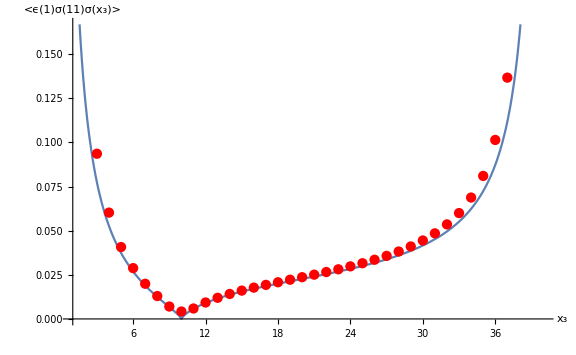

```mathematica
Show[Plot[Ising3pt[0,10,x3],{x3,1,40}],g1,AxesLabel->{"x_3","<ϵ(1)σ(11)σ(x_3)>"},ImageSize->Large,AxesStyle->Large]
```

```mathematica
(*ListContourPlot[data,Contours->{10^-2,10^-1.5,10^-1(*,10^-0.5,1*)},FrameLabel->{"x_2","x_3"},PlotLegends->BarLegend[Automatic,All,"TickLabels"->(Superscript[10,#]&/@{-2,-1.5,-1})],ContourShading->Table[Darker[Cyan,i],{i,0,1,0.1}]];
Show[%,Graphics[{White,Rectangle[{0,0},{40,3}]}],Graphics[{White,Rectangle[{0,0},{3,40}]}],Graphics[{White,Rectangle[{0,37},{40,40}]}],Graphics[{White,Rectangle[{37,0},{40,40}]}],Graphics[{White,Polygon[{{0,2},{2,0},{52,50},{50,52}}]}]]
Export["fig-eps-sig-sig-DMRG.pdf",%]*)
```

```mathematica
(* ContourPlot[Ising3pt[0,x2,x3],{x2,0,40},{x3,0,40},PlotPoints->50,FrameLabel->{"x_2","x_3"},Contours->{10^-2,10^-1.5,10^-1(*,10^-0.5,1*)},PlotLegends->BarLegend[Automatic,All,"TickLabels"->(Superscript[10,#]&/@{-2,-1.5,-1})],ContourShading->Table[Darker[Cyan,i],{i,0,1,0.1}]]
Export["fig-eps-sig-sig-theory.pdf",%] *)
```

```mathematica
Plot3D[f[x2,x3,40],{x2,0,40},{x3,0,40},PlotPoints->100,PlotLabel->"<ϵ(0)σ(x_2)σ(x_3)>, CFT",AxesLabel->{"x_2","x_3"},PlotRange->{0,10^-0.5}]
Export["fig-eps-sig-sig-theory-3D.pdf",Rasterize[%,"Image"]]
```

-Graphics3D-

fig-eps-sig-sig-theory-3D.pdf

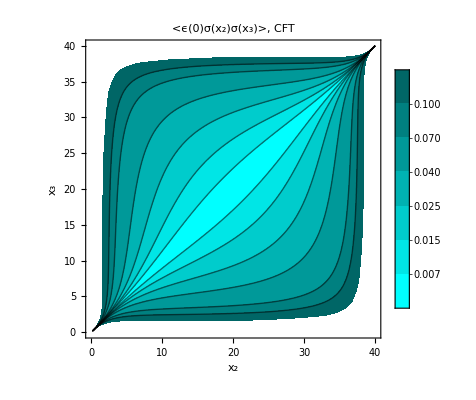

fig-eps-sig-sig-theory.pdf

```mathematica
ContourPlot[Ising3pt[0,x2,x3],{x2,0,40},{x3,0,40},PlotPoints->50,FrameLabel->{"x_2","x_3"},Contours->{0.007,0.015,0.025,0.04,0.07,10^-1},PlotRange->{0,0.16},PlotLegends->Automatic,ContourShading->Table[Darker[Cyan,i],{i,0,1,0.1}],PlotLabel->"<ϵ(0)σ(x_2)σ(x_3)>, CFT"]
Export["fig-eps-sig-sig-theory.pdf",Rasterize[%,"Image"]]
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

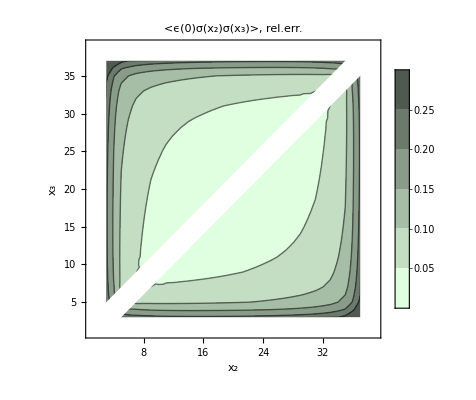

fig-eps-sig-sig-relative-error.pdf

```mathematica
{#[[1]],#[[2]],Abs[(#[[3]])/Ising3pt[0,#[[1]],#[[2]]]-1]}&/@data;
ListContourPlot[%,Contours->{0.05,0.1,0.15,0.2,0.25},FrameLabel->{"x_2","x_3"},ContourShading->Table[Darker[LightGreen,i],{i,0,1,0.13}],PlotLegends->Automatic,PlotLabel->"<ϵ(0)σ(x_2)σ(x_3)>, rel.err."];
Show[%,Graphics[{White,Rectangle[{0,0},{40,3}]}],Graphics[{White,Rectangle[{0,0},{3,40}]}],Graphics[{White,Rectangle[{0,37},{40,40}]}],Graphics[{White,Rectangle[{37,0},{40,40}]}],Graphics[{White,Polygon[{{0,2},{2,0},{52,50},{50,52}}]}]]
Export["fig-eps-sig-sig-relative-error.pdf",Rasterize[%,"Image"]]
(*ContourPlot[%,{x2,0,39},{x3,0,39},FrameLabel->{"x_2","x_3"},Contours->{10^-2,10^-1.5,10^-1,10^-0.5},PlotLegends->Automatic,ContourShading->Table[Darker[Cyan,i],{i,0,1,0.2}]]*)
```

```mathematica
{#[[1]],#[[2]],Abs[(#[[3]])/Ising3pt[0,#[[1]],#[[2]]]-1]}&/@data;
cp=ListContourPlot[%,Contours->{0.1},ContourShading->False,ContourStyle->{Thick,Dashed,Red}];

(*ContourPlot[%,{x2,0,39},{x3,0,39},FrameLabel->{"x_2","x_3"},Contours->{10^-2,10^-1.5,10^-1,10^-0.5},PlotLegends->Automatic,ContourShading->Table[Darker[Cyan,i],{i,0,1,0.2}]]*)
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

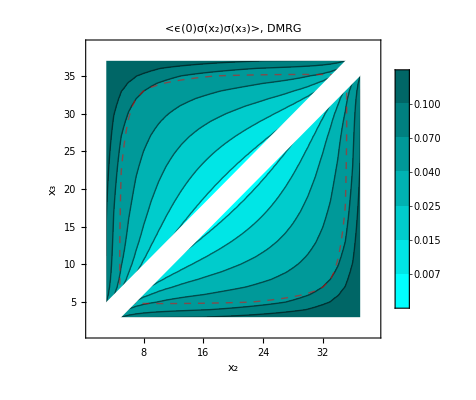

fig-eps-sig-sig-DMRG.pdf

```mathematica
ListContourPlot[data,Contours->{0.007,0.015,0.025,0.04,0.07,10^-1},FrameLabel->{"x_2","x_3"},PlotLegends->Automatic,ContourShading->Table[Darker[Cyan,i],{i,0,1,0.1}],PlotLabel->"<ϵ(0)σ(x_2)σ(x_3)>, DMRG"];
Show[%,cp,Graphics[{White,Rectangle[{0,0},{40,3}]}],Graphics[{White,Rectangle[{0,0},{3,40}]}],Graphics[{White,Rectangle[{0,37},{40,40}]}],Graphics[{White,Rectangle[{37,0},{40,40}]}],Graphics[{White,Polygon[{{0,2},{2,0},{52,50},{50,52}}]}]]
Export["fig-eps-sig-sig-DMRG.pdf",Rasterize[%,"Image"]]
```

### sample ⟨σσ⟩

```mathematica
L=40;
data$temp=Riffle[Table[i,{i,1,20}],0.5293860225014412/0.2999304743017528{0.64195,0.5017,0.45375,0.423125,0.400625,0.382475,0.368225,0.356875,0.34615,0.33675,0.332025,0.32835,0.324575,0.3225,0.319525,0.315225,0.31235,0.3101,0.30765,0.3066}]//Partition[#,2]&;
data$temp2={(L/π)Sin[#[[1]] π/L],#[[2]]}&/@%//N;
```

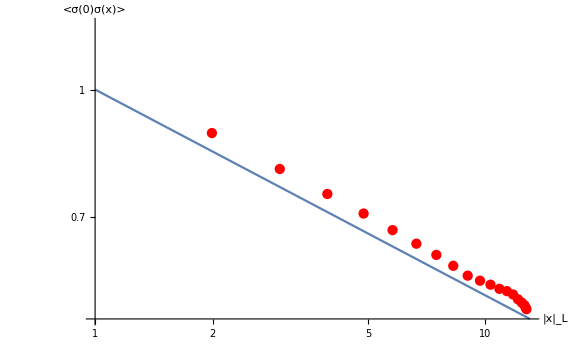

```mathematica
g=Show[LogLogPlot[1/y^(1/4),{y,1,13},PlotRange->{Automatic,{0,1.2}}],ListLogLogPlot[data$temp2[[2;;20]], PlotStyle->Red],AxesLabel->{"|x|_L","<σ(0)σ(x)>"},ImageSize->Large,AxesStyle->Large]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/junchenrong/Library/Mobile Documents/com~apple~CloudDocs/Research_projects/0.0 Rydberg_Atoms/plots

```mathematica
Export["fig-sigma-sigma-sample-10e3.pdf",g]
```

fig-sigma-sigma-sample-10e3.pdf

```mathematica
L=40;
data$temp=Riffle[Table[i,{i,1,20}],0.5293860225014412/0.2999304743017528{0.6319950000000001,0.4882625,0.43884,0.4072799999999999,0.38568250000000004,0.3690375,0.356035,0.34541750000000004,0.33657750000000003,0.3292175,0.3232775,0.3184775,0.31414749999999997,0.3100225,0.306705,0.3046375,0.30364500000000005,0.30269749999999995,0.30164749999999996,0.301235}]//Partition[#,2]&;
data$temp2={(L/π)Sin[#[[1]] π/L],#[[2]]}&/@%//N;
```

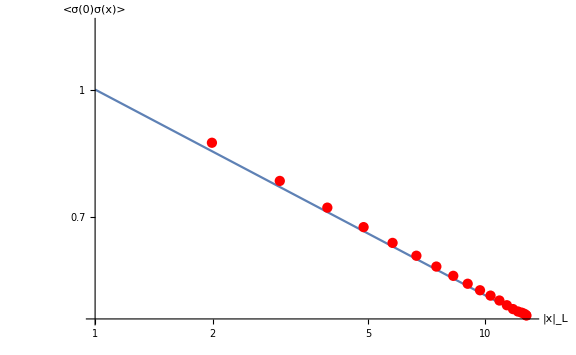

```mathematica
g=Show[LogLogPlot[1/y^(1/4),{y,1,13},PlotRange->{Automatic,{0,1.2}}],ListLogLogPlot[data$temp2[[2;;20]], PlotStyle->Red],AxesLabel->{"|x|_L","<σ(0)σ(x)>"},ImageSize->Large,AxesStyle->Large]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/junchenrong/Library/Mobile Documents/com~apple~CloudDocs/Research_projects/0.0 Rydberg_Atoms/plots

```mathematica
Export["fig-sigma-sigma-sample-10e4.pdf",g]
```

fig-sigma-sigma-sample-10e4.pdf

### Sample ⟨σσϵ⟩

#### sample size 10^4

```mathematica
measure0(*sample size 10^4*)={{{0.12448758000023129,0.0005492731777114875},{0.1091562347501945,0.0005127500243613351},{0.10322119000014951,0.00046216995377198507},{0.10309553125013417,0.00047804776724102814},{0.10022663325012392,0.0004715468404660588},{0.09930000950011697,0.0004772453263131212},{0.09781781750011154,0.00047407829163013027},{0.09584399425010745,0.000477232825222227},{0.09386892425010418,0.0004763136298491982},{0.09250177200010133,0.0004777414400098029},{0.09141949800009888,0.00047709021012448297},{0.09087149225009676,0.00047829889818837507},{0.09033581050009493,0.00047716273756364687},{0.08979312250009379,0.00047857988864739013},{0.08989335225009297,0.00047757044136108155},{0.09040126925009218,0.000478534820152826},{0.0905818437500916,0.00047798926460283135},{0.0905940345000913,0.0004780822527429468},{0.09068554475009125,0.00047800814875681024},{0.09104324800009123,0.00047822185620408466},{0.09135885800009114,0.0004775582637830621},{0.09137324800009111,0.00047777332639113213},{0.09158429475009136,0.00047790638054802647},{0.09240653450009158,0.00047810287308186256},{0.09376934375009181,0.00047670754599493496},{0.09511251925009229,0.00047726659410646146},{0.09686335225009315,0.00047551993646971903},{0.09939062250009435,0.0004762358240963874},{0.10206206050009584,0.0004744254493686252},{0.10534899225009758,0.00047427302185443964},{0.10922324800009985,0.00047203925954763946},{0.11294677200010256,0.0004723808457240382},{0.11799892425010565,0.0004685523505511602},{0.12567149425010926,0.0004690159199960388},{0.13580781750011367,0.0004599208100036395},{0.1506775095001196,0.00046056205209037935},{0.17554663325012748,0.00043427416025481713},{0.2648680312501392,0.00041186273335110384},{0.31734619000015546,0.00037283813613133934}},{{0.1091562347501945,0.0005127500243613351},{0.05371383000021856,0.0005548642710944672},{0.04968373475018264,0.0004908596204656816},{0.05722119000014263,0.0004783817998812912},{0.059520531250128295,0.00047476436393296983},{0.060957883250119284,0.0004774507520959546},{0.06184000950011291,0.0004750758501731345},{0.06169031750010769,0.00047629745306251766},{0.061043994250103636,0.0004758175198119083},{0.06058392425010048,0.0004766188473726008},{0.060194272000097734,0.0004761167421120559},{0.06025949800009519,0.000476872718454716},{0.060397742250093214,0.0004757193880478624},{0.06038081050009191,0.00047668739353595865},{0.06068687250009104,0.000476064108151209},{0.06135460225009017,0.00047663624572032544},{0.061931269250089314,0.00047624250383088113},{0.06216684375008884,0.0004761821787588357},{0.062315284500088636,0.0004761418218540573},{0.06282179475008862,0.0004765322374886025},{0.06319449800008858,0.0004758696058749947},{0.06323635800008848,0.00047588209754681867},{0.06335824800008868,0.0004759262701920384},{0.06392429475008894,0.0004764342970649545},{0.06512778450008903,0.0004752115175073874},{0.0663768437500891,0.00047575656007732434},{0.06792376925008954,0.0004745951288675843},{0.07010210225009061,0.0004750660981286524},{0.07248062250009203,0.0004738371800338938},{0.07522206050009368,0.00047381170684364593},{0.07845649225009564,0.0004722460984251903},{0.08165074800009783,0.00047252256527637835},{0.08565302200010062,0.00046991840619368117},{0.09177142425010429,0.0004710099107105776},{0.1004927442501081,0.00046415281238879616},{0.11310906750011267,0.00046541260210038947},{0.13455375950011916,0.00044510460706645514},{0.20637413325012818,0.0004412531249052352},{0.2648680312501392,0.0004118627333511024}},{{0.10322119000014951,0.00046216995377198507},{0.04968373475018264,0.0004908596204656816},{0.01057508000011788,0.0005319378406096167},{0.013854984750129076,0.0004943944265914871},{0.018736190000110654,0.0004544375439734007},{0.021626781250103505,0.00046197712166255397},{0.023524133250099718,0.00045668401969910265},{0.024536259500095303,0.00045950867739460354},{0.025204067500091448,0.0004567680002152962},{0.025665244250088905,0.00045858124940530615},{0.025920174250087066,0.00045741920160383983},{0.02622052200008471,0.00045837387097275213},{0.026716998000082495,0.0004570292157934885},{0.027021492250080527,0.0004579624607020271},{0.02739331050007979,0.00045729297519317153},{0.02797812250007913,0.00045832753693375686},{0.028549602250078524,0.0004576531325423425},{0.029003769250078443,0.0004578619500912002},{0.029324343750078447,0.00045756638703602087},{0.02986653450007876,0.00045801746313945925},{0.03029179475007957,0.0004577464523456499},{0.030238248000079845,0.0004574931290048705},{0.0302026080000797,0.0004572392329374313},{0.03044324800007918,0.0004577383176919149},{0.031015544750078967,0.0004573925474187382},{0.031952784500079004,0.0004579671718349278},{0.03308684375007941,0.00045692671001107155},{0.034567519250081,0.0004576172002114357},{0.03614710225008252,0.000456494778873292},{0.0379768725000843,0.0004569704563636614},{0.0401995605000866,0.0004556889251570535},{0.042292742250088604,0.00045637222009500665},{0.04483199800009148,0.00045453998852826966},{0.04877052200009543,0.00045605968333647685},{0.05437392425009989,0.0004519858991206667},{0.0632052442501045,0.00045421023245496546},{0.07812531750011022,0.00044064396537789183},{0.1345537595001192,0.00044510460706645314},{0.17554663325012754,0.0004342741602548144}},{{0.10309553125013417,0.00047804776724102814},{0.05722119000014263,0.0004783817998812912},{0.013854984750129076,0.0004943944265914871},{0.006818830000024212,0.0005439792224855433},{0.008108734750061247,0.0004948766822210064},{0.011713690000082594,0.00046963348132256786},{0.013916781250084491,0.00047011846672897025},{0.015127883250083282,0.00046951659076912715},{0.01613625950008166,0.0004690148860452401},{0.01692031750007975,0.00046869779106875723},{0.017567744250078763,0.00046868965590479846},{0.017971424250077164,0.00046908123922624606},{0.01844927200007502,0.0004681812568933083},{0.018838248000073644,0.0004688744246652176},{0.019113992250072712,0.00046846305070215793},{0.01972706050007207,0.00046890080530674903},{0.02028312250007147,0.0004687353675259632},{0.020938352250071603,0.0004685060762373797},{0.021401269250071804,0.0004686708294353954},{0.02179434375007226,0.0004687197368689347},{0.02232528450007323,0.0004685660736626457},{0.022398044750074033,0.00046855538011587904},{0.022266998000073535,0.00046832322263703124},{0.02239385800007267,0.00046858317073326955},{0.022704498000072525,0.0004680985091938427},{0.023421794750071685,0.00046897717824856595},{0.024507784500072235,0.0004681035077895624},{0.025778093750074785,0.000468572427433466},{0.027160019250076634,0.00046785308358788277},{0.028685852250077987,0.0004679287815879662},{0.030720622500080112,0.000467155752600277},{0.03267206050008217,0.00046782145103931326},{0.0347264922500846,0.00046611258717649213},{0.037731998000088425,0.0004677924453371231},{0.0423455220000935,0.00046373217479535995},{0.05016142425009874,0.00046674557056773484},{0.06320524425010432,0.00045421023245496546},{0.11310906750011283,0.0004654126021003878},{0.1506775095001196,0.0004605620520903832}},{{0.10022663325012392,0.0004715468404660588},{0.059520531250128295,0.00047476436393296983},{0.018736190000110654,0.0004544375439734007},{0.008108734750061247,0.0004948766822210064},{0.0037000799999862,0.0005393318408767414},{0.005249984749977381,0.0004983534393711434},{0.0077736900000473915,0.00046313570991432686},{0.009261781250050768,0.00046828238968796027},{0.010234133250056753,0.0004646184701554484},{0.011087509500062298,0.0004661146086373155},{0.01199531750006262,0.00046416741356944847},{0.012683994250064525,0.00046566153439163096},{0.013135174250064044,0.0004642746523428659},{0.013565522000063718,0.00046544318583117874},{0.013928248000063512,0.000464592475156808},{0.014471492250062983,0.0004654184799301988},{0.015155810500063205,0.000464886999709668},{0.01588437250006496,0.0004648995183846011},{0.016485852250065932,0.00046456389007326295},{0.016830019250066584,0.00046507943174761305},{0.01706434375006697,0.0004646950199038582},{0.017171534500067646,0.0004649497693504554},{0.017269294750067762,0.00046502908876001284},{0.01741949800006687,0.0004650846992142888},{0.017721358000065836,0.00046423839930081166},{0.01822949800006632,0.00046501607593511703},{0.019100544750067082,0.0004644798222014158},{0.020266534500068323,0.00046510552127558335},{0.02165184375007075,0.0004639834473736933},{0.02317001925007326,0.0004645258698487728},{0.024828352250076176,0.0004636008725489406},{0.026726872500078224,0.0004645386414175648},{0.028687060500079888,0.0004625515379893003},{0.031148992250082917,0.00046434813117979246},{0.0350807480000878,0.0004599783477576408},{0.04234552200009382,0.00046373217479536304},{0.054373924250099744,0.0004519858991206659},{0.10049274425010796,0.00046415281238879817},{0.1358078175001136,0.00045992081000364267}},{{0.09930000950011697,0.0004772453263131212},{0.060957883250119284,0.0004774507520959546},{0.021626781250103505,0.00046197712166255397},{0.011713690000082594,0.00046963348132256786},{0.005249984749977381,0.0004983534393711434},{0.002681330000025867,0.0005436489499794572},{0.0036562347499882407,0.0004971596445992691},{0.0055936900000087475,0.0004688939984058982},{0.006721781250021962,0.0004709251876943248},{0.007569133250033966,0.0004691107593753654},{0.008590009500043348,0.00046911778521218766},{0.00943906750005005,0.00046864799334421666},{0.00989899425004946,0.0004683766651250711},{0.010211424250048815,0.0004689772289297733},{0.010610522000049145,0.00046857313933494247},{0.011220748000053172,0.00046893318799143415},{0.011910242250054255,0.00046880474786702744},{0.012597060500055329,0.00046861915226041926},{0.013250622500056507,0.0004686244042067869},{0.013664602250057353,0.00046878202094051473},{0.013883769250057593,0.0004688194995276819},{0.013840593750057886,0.00046864292170106916},{0.013899034500058464,0.00046878517326169323},{0.014178044750058743,0.0004692815020440986},{0.014436998000057715,0.0004682844720871887},{0.014853858000059183,0.0004686016013213433},{0.015550748000062876,0.000468048463859953},{0.01660679475006511,0.00046896853546410703},{0.017922784500066236,0.00046796916081121254},{0.019518093750068247,0.00046833649522944146},{0.02120126925007089,0.0004676763225919782},{0.02278835225007355,0.0004682210243379368},{0.02470312250007589,0.0004666105832596617},{0.0273808105000791,0.00046816285876795035},{0.03114899225008351,0.0004643481311797978},{0.03773199800008974,0.0004677924453371225},{0.04877052200009601,0.00045605968333647213},{0.09177142425010426,0.00047100991071057714},{0.12567149425010926,0.0004690159199960344}},{{0.09781781750011154,0.00047407829163013027},{0.06184000950011291,0.0004750758501731345},{0.023524133250099718,0.00045668401969910265},{0.013916781250084491,0.00047011846672897025},{0.0077736900000473915,0.00046313570991432686},{0.0036562347499882407,0.0004971596445992691},{0.001945080000023725,0.0005413132019249627},{0.0028674847500047723,0.0004992614228832233},{0.004391189999990058,0.0004660403792128932},{0.0055380312499955855,0.00046994667091869463},{0.006432883250016374,0.00046648264334362316},{0.007328759500034057,0.0004679472170057071},{0.007895317500035958,0.0004658467323385565},{0.008093994250035182,0.00046739361927830526},{0.008398924250035321,0.0004663272379491604},{0.008990522000037294,0.00046710353555016424},{0.009634498000039137,0.0004666544493695752},{0.010213992250041166,0.0004668623264223274},{0.010845810500045782,0.00046655333301422105},{0.0114018725000499,0.0004669900210306128},{0.011850852250051993,0.00046645041503868374},{0.011978769250052717,0.00046683388679542496},{0.011805593750052901,0.00046661994846638555},{0.011866534500052782,0.0004671766514779287},{0.012190544750052684,0.0004664311322831024},{0.012621998000055309,0.00046675615299599286},{0.013226358000057411,0.0004657932515317328},{0.01412324800005945,0.00046679526638653614},{0.015325544750061629,0.00046622052091008584},{0.016991534500064805,0.00046655057169817294},{0.018821843750067457,0.00046569779924697996},{0.020385019250069716,0.00046672677746221396},{0.022010852250072203,0.00046479073555518265},{0.024703122500075832,0.00046661058325966475},{0.02868706050008073,0.0004625515379893036},{0.03472649225008665,0.00046611258717649425},{0.0448319980000928,0.00045453998852827644},{0.08565302200010097,0.00046991840619366854},{0.11799892425010573,0.0004685523505511638}},{{0.09584399425010745,0.000477232825222227},{0.06169031750010769,0.00047629745306251766},{0.024536259500095303,0.00045950867739460354},{0.015127883250083282,0.00046951659076912715},{0.009261781250050768,0.00046828238968796027},{0.0055936900000087475,0.0004688939984058982},{0.0028674847500047723,0.0004992614228832233},{0.0017213300000234583,0.000543208637090141},{0.0024374847500277397,0.000498111720265731},{0.0039836899999916055,0.00046841098543834},{0.0050330312499834865,0.00047075677697382926},{0.005819133250004875,0.0004690436860680304},{0.006513759500010815,0.0004688342488375362},{0.006922817500017421,0.00046835866718762203},{0.0072464942500202485,0.00046840898300236876},{0.007685174250027249,0.0004686442376973645},{0.00817427200003043,0.00046859986896145194},{0.008530748000033523,0.0004684275836365271},{0.009047742250035832,0.00046833161006026023},{0.009557060500038243,0.00046850632308233805},{0.010046872500041161,0.00046835552684847993},{0.010343352250044884,0.00046828427627741015},{0.010288769250046398,0.00046853209537350073},{0.010149343750045307,0.0004687187577896386},{0.010326534500045188,0.00046806609189852736},{0.010961794750049143,0.00046867319399205285},{0.011684498000053134,0.0004676655679799446},{0.012348858000056284,0.0004685123341916461},{0.013349498000057117,0.0004677568181758192},{0.014873044750059699,0.00046848178229052866},{0.01682778450006418,0.0004678401985848465},{0.018821843750067634,0.0004684293653135309},{0.020385019250069653,0.00046672677746221515},{0.022788352250072894,0.0004682210243379365},{0.026726872500078172,0.00046453864141756475},{0.03267206050008452,0.00046782145103930713},{0.042292742250090165,0.00045637222009501185},{0.08165074800009822,0.0004725225652763836},{0.11294677200010256,0.0004723808457240454}},{{0.09386892425010418,0.0004763136298491982},{0.061043994250103636,0.0004758175198119083},{0.025204067500091448,0.0004567680002152962},{0.01613625950008166,0.0004690148860452401},{0.010234133250056753,0.0004646184701554484},{0.006721781250021962,0.0004709251876943248},{0.004391189999990058,0.0004660403792128932},{0.0024374847500277397,0.000498111720265731},{0.0014775800000119694,0.0005421852815215188},{0.002253734750021676,0.0004993500903552039},{0.0035436900000045115,0.00046691463308406555},{0.004401781249990818,0.0004707987985454223},{0.005114133249983926,0.0004671306485018086},{0.005717509499995977,0.0004685889963132966},{0.006042817500006615,0.0004668797828164754},{0.006418994250013812,0.00046826895563011983},{0.006756424250016747,0.0004676407651285637},{0.006919272000017962,0.00046779426086206735},{0.007303248000023253,0.0004672910917653489},{0.007820242250029048,0.0004678373215866743},{0.008198310500034143,0.00046729017221220184},{0.008369372500036807,0.00046758533466191566},{0.008468352250037116,0.0004675839684228121},{0.008500019250036711,0.0004680088543796354},{0.008551843750037013,0.00046714998836261656},{0.009164034500041966,0.00046796768825545796},{0.010066794750047991,0.0004669857093973059},{0.01077199800004958,0.0004677960225273266},{0.011593858000050729,0.0004667588382151609},{0.01289449800005457,0.0004674540679231493},{0.014734294750059223,0.0004669618013223737},{0.016827784500064332,0.00046784019858485035},{0.018821843750067863,0.00046569779924698034},{0.021201269250071337,0.0004676763225919746},{0.02482835225007566,0.00046360087254893804},{0.030720622500082277,0.0004671557526002833},{0.04019956050008809,0.0004556889251570536},{0.0784564922500959,0.00047224609842518527},{0.10922324800009992,0.00047203925954763593}},{{0.09250177200010133,0.0004777414400098029},{0.06058392425010048,0.0004766188473726008},{0.025665244250088905,0.00045858124940530615},{0.01692031750007975,0.00046869779106875723},{0.011087509500062298,0.0004661146086373155},{0.007569133250033966,0.0004691107593753654},{0.0055380312499955855,0.00046994667091869463},{0.0039836899999916055,0.00046841098543834},{0.002253734750021676,0.0004993500903552039},{0.0012488299999976649,0.0005430654627584747},{0.001746234750010474,0.0004983731379457785},{0.00280869000001659,0.0004684260188167015},{0.0036892812500052934,0.00047037312642908194},{0.004320383249991936,0.0004686027475222357},{0.004626259499988443,0.00046876359316948106},{0.004999067499987243,0.0004684029727751281},{0.00524149424999365,0.00046886213875916866},{0.00526267424999303,0.00046844454674455907},{0.005660522000000303,0.00046846164342180096},{0.006229498000010969,0.0004685219121653875},{0.0066264922500175434,0.0004682451087481738},{0.00683706050002392,0.0004681371767140429},{0.006816872500020921,0.0004684868209741122},{0.006838352250017958,0.00046851862199144713},{0.007006269250017335,0.00046804942050484384},{0.007488093750028538,0.00046849027576522354},{0.008297784500034015,0.00046778252516026914},{0.009166794750040124,0.00046852979681116986},{0.010093248000044708,0.0004675790157629207},{0.011355108000047156,0.00046797871666002627},{0.012894498000050403,0.0004674540679231493},{0.014873044750058835,0.0004684817822905247},{0.016991534500064576,0.000466550571698177},{0.019518093750068733,0.0004683364952294362},{0.023170019250073382,0.0004645258698487708},{0.028685852250079812,0.0004679287815879644},{0.03797687250008612,0.00045697045636366085},{0.07522206050009386,0.0004738117068436468},{0.10534899225009765,0.0004742730218544471}},{{0.09141949800009888,0.00047709021012448297},{0.060194272000097734,0.0004761167421120559},{0.025920174250087066,0.00045741920160383983},{0.017567744250078763,0.00046868965590479846},{0.01199531750006262,0.00046416741356944847},{0.008590009500043348,0.00046911778521218766},{0.006432883250016374,0.00046648264334362316},{0.0050330312499834865,0.00047075677697382926},{0.0035436900000045115,0.00046691463308406555},{0.001746234750010474,0.0004983731379457785},{0.0007863299999905448,0.0005424901791831602},{0.0012524847499915035,0.0004996538624951888},{0.0022711900000160963,0.0004669182872953701},{0.003024281250012912,0.00047078497063230627},{0.003442883250003676,0.00046764847556911423},{0.0038800094999945156,0.00046906226779923647},{0.004204067499993013,0.00046759687453891196},{0.004121494249992616,0.00046818028449889147},{0.0043889242499906105,0.00046778906560183335},{0.005101771999989444,0.00046838187904541396},{0.005530747999997616,0.00046762080006560207},{0.00580149224999967,0.0004679865420614604},{0.005898310500004751,0.00046789083906575285},{0.005771872499997105,0.00046832648498276687},{0.00586960224999865,0.0004673141037831436},{0.006292519250007257,0.000468137308077491},{0.0069255937500167656,0.0004672364930043256},{0.007640284500028156,0.00046802344784270403},{0.008631794750032076,0.00046708728747233514},{0.010093248000040187,0.000467579015762925},{0.011593858000043294,0.0004667588382151582},{0.013349498000052704,0.00046775681817581795},{0.015325544750060179,0.0004662205209100889},{0.01792278450006578,0.00046796916081121227},{0.021651843750071342,0.00046398344737369924},{0.027160019250076908,0.0004678530835878854},{0.03614710225008378,0.00045649477887329},{0.07248062250009212,0.00047383718003388907},{0.10206206050009567,0.000474425449368631}},{{0.09087149225009676,0.00047829889818837507},{0.06025949800009519,0.000476872718454716},{0.02622052200008471,0.00045837387097275213},{0.017971424250077164,0.00046908123922624606},{0.012683994250064525,0.00046566153439163096},{0.00943906750005005,0.00046864799334421666},{0.007328759500034057,0.0004679472170057071},{0.005819133250004875,0.0004690436860680304},{0.004401781249990818,0.0004707987985454223},{0.00280869000001659,0.0004684260188167015},{0.0012524847499915035,0.0004996538624951888},{0.0006163299999911586,0.0005433281938313846},{0.001117484749991203,0.0004986321261368687},{0.00188119000000688,0.0004687477729942775},{0.002440531250021789,0.0004708952003854034},{0.002901633250010173,0.00046914229515425225},{0.003342509500004406,0.0004695935429477468},{0.003546567499998532,0.00046819245743612384},{0.003688994249993193,0.00046890669281646815},{0.0043801742499903025,0.00046889842775423685},{0.004973021999989006,0.0004687681675628681},{0.005211997999988419,0.00046848669996287873},{0.005453992249988794,0.0004686911466814843},{0.005539560499990208,0.0004687443762481595},{0.005503122499990046,0.0004681524504243051},{0.005705852249999325,0.0004687371869421657},{0.006246269250008222,0.00046796429802072444},{0.006781843750013842,0.0004686608953249047},{0.0076402845000203366,0.000468023447842698},{0.009166794750032913,0.0004685297968111564},{0.01077199800003955,0.0004677960225273194},{0.012348858000047357,0.0004685123341916441},{0.0141232480000571,0.00046679526638653815},{0.01660679475006412,0.0004689685354641063},{0.020266534500068538,0.00046510552127558357},{0.025778093750075417,0.00046857242743346156},{0.03456751925008188,0.00045761720021143825},{0.07010210225009102,0.00047506609812864687},{0.09939062250009423,0.00047623582409638557}},{{0.09033581050009493,0.00047716273756364687},{0.060397742250093214,0.0004757193880478624},{0.026716998000082495,0.0004570292157934885},{0.01844927200007502,0.0004681812568933083},{0.013135174250064044,0.0004642746523428659},{0.00989899425004946,0.0004683766651250711},{0.007895317500035958,0.0004658467323385565},{0.006513759500010815,0.0004688342488375362},{0.005114133249983926,0.0004671306485018086},{0.0036892812500052934,0.00047037312642908194},{0.0022711900000160963,0.0004669182872953701},{0.001117484749991203,0.0004986321261368687},{0.0007050799999897101,0.0005422917864507188},{0.0010137347499913092,0.0004995022447447587},{0.0016786900000046268,0.0004670063349347436},{0.0022792812500152444,0.00047075168345480983},{0.0026503832500167084,0.00046797381614875275},{0.002987509500007726,0.0004686546192760955},{0.0033690674999954577,0.00046736208060489383},{0.003842744249991218,0.00046818431576558557},{0.0043451742499889335,0.0004675663864329665},{0.004684271999986482,0.00046765060633155783},{0.004868247999984997,0.00046758369828771507},{0.005105242249984581,0.00046808902465275654},{0.005213310499987902,0.0004671387736587897},{0.005320622499990802,0.0004681031894256956},{0.005743352250002842,0.0004667073749894697},{0.006246269250009599,0.0004679642980207259},{0.006925593750014152,0.0004672364930043248},{0.008297784500028202,0.00046778252516027895},{0.01006679475003766,0.00046698570939729736},{0.011684498000043023,0.0004676655679799372},{0.013226358000052117,0.00046579325153174453},{0.015550748000060446,0.00046804846385995694},{0.019100544750066534,0.000464479822201418},{0.024507784500074098,0.00046810350778956597},{0.033086843750081064,0.000456926710011076},{0.06792376925009003,0.0004745951288675896},{0.0968633522500931,0.00047551993646972076}},{{0.08979312250009379,0.00047857988864739013},{0.06038081050009191,0.00047668739353595865},{0.027021492250080527,0.0004579624607020271},{0.018838248000073644,0.0004688744246652176},{0.013565522000063718,0.00046544318583117874},{0.010211424250048815,0.0004689772289297733},{0.008093994250035182,0.00046739361927830526},{0.006922817500017421,0.00046835866718762203},{0.005717509499995977,0.0004685889963132966},{0.004320383249991936,0.0004686027475222357},{0.003024281250012912,0.00047078497063230627},{0.00188119000000688,0.0004687477729942775},{0.0010137347499913092,0.0004995022447447587},{0.0006988299999921542,0.0005432991106864596},{0.0010162347499930557,0.0004990047080608194},{0.0015486900000044946,0.00046866543184641654},{0.0019342812500143932,0.0004712624715058702},{0.002329133250017313,0.0004686795049160116},{0.002867509500009528,0.0004691707282818739},{0.0033865674999990717,0.00046841338082623685},{0.0036677442499920524,0.0004687082450038774},{0.00397142424999022,0.0004684193826767212},{0.004301771999989916,0.0004688829324818278},{0.004560747999987958,0.00046864365370934575},{0.004808992249986325,0.000468347272443963},{0.005033310499986513,0.00046913853610436616},{0.0053206224999909285,0.0004681031894256984},{0.00570585225000523,0.000468737186942166},{0.006292519250010589,0.0004681373080774947},{0.007488093750020349,0.00046849027576521986},{0.009164034500032756,0.0004679676882554559},{0.010961794750041814,0.0004686731939920357},{0.012621998000050594,0.0004667561529959968},{0.014853858000058487,0.0004686016013213301},{0.018229498000065784,0.00046501607593511275},{0.023421794750072004,0.00046897717824856275},{0.03195278450007958,0.00045796717183492914},{0.06637684375008931,0.00047575656007732347},{0.09511251925009218,0.0004772665941064638}},{{0.08989335225009297,0.00047757044136108155},{0.06068687250009104,0.000476064108151209},{0.02739331050007979,0.00045729297519317153},{0.019113992250072712,0.00046846305070215793},{0.013928248000063512,0.000464592475156808},{0.010610522000049145,0.00046857313933494247},{0.008398924250035321,0.0004663272379491604},{0.0072464942500202485,0.00046840898300236876},{0.006042817500006615,0.0004668797828164754},{0.004626259499988443,0.00046876359316948106},{0.003442883250003676,0.00046764847556911423},{0.002440531250021789,0.0004708952003854034},{0.0016786900000046268,0.0004670063349347436},{0.0010162347499930557,0.0004990047080608194},{0.000590079999993861,0.0005425935536741766},{0.0007449847499946147,0.0004995778067354639},{0.0009736899999953973,0.000467664509876355},{0.0014767812500040506,0.00047082892367397033},{0.002169133250018071,0.0004681716958123676},{0.002731259500016374,0.00046917862524970303},{0.0032403175000005903,0.00046737452089772285},{0.003483994249992851,0.0004681866121555872},{0.003822674249991989,0.000467934083397156},{0.004311771999991255,0.00046835445493692286},{0.004590747999987766,0.0004675574139475186},{0.004808992249986506,0.0004683472724439624},{0.005213310499991029,0.00046713877365879217},{0.005503122500001976,0.0004681524504243067},{0.005869602250007098,0.00046731410378314503},{0.007006269250018696,0.00046804942050484454},{0.00855184375003114,0.0004671499883624833},{0.010326534500041541,0.0004680660918985247},{0.01219054475004998,0.00046643113228310684},{0.014436998000056933,0.00046828447208718154},{0.017721358000064913,0.00046423839930081963},{0.02270449800007119,0.0004680985091938425},{0.031015544750077825,0.000457392547418732},{0.06512778450008896,0.00047521151750738836},{0.09376934375009159,0.00047670754599492965}},{{0.09040126925009218,0.000478534820152826},{0.06135460225009017,0.00047663624572032544},{0.02797812250007913,0.00045832753693375686},{0.01972706050007207,0.00046890080530674903},{0.014471492250062983,0.0004654184799301988},{0.011220748000053172,0.00046893318799143415},{0.008990522000037294,0.00046710353555016424},{0.007685174250027249,0.0004686442376973645},{0.006418994250013812,0.00046826895563011983},{0.004999067499987243,0.0004684029727751281},{0.0038800094999945156,0.00046906226779923647},{0.002901633250010173,0.00046914229515425225},{0.0022792812500152444,0.00047075168345480983},{0.0015486900000044946,0.00046866543184641654},{0.0007449847499946147,0.0004995778067354639},{0.0005475799999963282,0.0005434094477581527},{0.0005474847499984817,0.0004996868692703564},{0.0009336899999960165,0.0004685496734110616},{0.0017517812500152852,0.00047148871017465926},{0.002380383250017331,0.0004691934149819482},{0.0027825095000121483,0.0004693124854604149},{0.003224067499999879,0.00046821290537821936},{0.003537744249993324,0.0004691076678612723},{0.0038764242499932807,0.0004692164948725874},{0.004311771999990452,0.00046835445493692275},{0.004560747999988536,0.00046864365370935057},{0.005105242249988361,0.00046808902465275817},{0.005539560500004542,0.0004687443762481599},{0.005771872500007447,0.0004683264849827661},{0.006838352250016677,0.00046851862199144973},{0.008500019250031708,0.00046800885437963595},{0.010149343750040334,0.00046871875778963526},{0.01186653450004751,0.0004671766514779285},{0.01417804475005499,0.00046928150204410154},{0.017419498000063736,0.0004650846992142839},{0.0223938580000717,0.00046858317073327545},{0.030443248000078166,0.00045773831769190654},{0.06392429475008882,0.0004764342970649567},{0.0924065345000915,0.00047810287308186673}},{{0.0905818437500916,0.00047798926460283135},{0.061931269250089314,0.00047624250383088113},{0.028549602250078524,0.0004576531325423425},{0.02028312250007147,0.0004687353675259632},{0.015155810500063205,0.000464886999709668},{0.011910242250054255,0.00046880474786702744},{0.009634498000039137,0.0004666544493695752},{0.00817427200003043,0.00046859986896145194},{0.006756424250016747,0.0004676407651285637},{0.00524149424999365,0.00046886213875916866},{0.004204067499993013,0.00046759687453891196},{0.003342509500004406,0.0004695935429477468},{0.0026503832500167084,0.00046797381614875275},{0.0019342812500143932,0.0004712624715058702},{0.0009736899999953973,0.000467664509876355},{0.0005474847499984817,0.0004996868692703564},{0.000547579999995548,0.0005430441532847191},{0.0007512347499970417,0.0004994528941262523},{0.001356190000010146,0.00046802763032492695},{0.0020942812500158742,0.0004714451310100668},{0.0024903832500186335,0.00046852963303107935},{0.00275500950001334,0.00046902699312343716},{0.0032478174999991966,0.00046780553047193093},{0.003537744249998705,0.0004691076678612793},{0.003822674249997723,0.0004679340833971601},{0.004301771999989974,0.0004688829324818294},{0.004868247999990874,0.00046758369828707425},{0.005453992250004893,0.0004686911466814885},{0.005898310500011305,0.00046789083906575307},{0.006816872500015814,0.00046848682097410874},{0.00846835225003047,0.00046758396842282423},{0.01028876925004009,0.0004685320953735083},{0.011805593750046695,0.00046661994846638755},{0.013899034500053021,0.00046878517326169806},{0.017269294750063398,0.000465029088759996},{0.022266998000071352,0.0004683232226370354},{0.030202608000078904,0.00045723923293742685},{0.06335824800008875,0.0004759262701920377},{0.09158429475009143,0.00047790638054803335}},{{0.0905940345000913,0.0004780822527429468},{0.06216684375008884,0.0004761821787588357},{0.029003769250078443,0.0004578619500912002},{0.020938352250071603,0.0004685060762373797},{0.01588437250006496,0.0004648995183846011},{0.012597060500055329,0.00046861915226041926},{0.010213992250041166,0.0004668623264223274},{0.008530748000033523,0.0004684275836365271},{0.006919272000017962,0.00046779426086206735},{0.00526267424999303,0.00046844454674455907},{0.004121494249992616,0.00046818028449889147},{0.003546567499998532,0.00046819245743612384},{0.002987509500007726,0.0004686546192760955},{0.002329133250017313,0.0004686795049160116},{0.0014767812500040506,0.00047082892367397033},{0.0009336899999960165,0.0004685496734110616},{0.0007512347499970417,0.0004994528941262523},{0.0006375799999945159,0.0005430095455276777},{0.0007849847499943382,0.000499137949801935},{0.0012286899999980562,0.000468299017086062},{0.001960531250013918,0.00047112851819300946},{0.0024016332500145813,0.00046857221505728193},{0.0027550095000099624,0.00046902699312343233},{0.0032240674999986937,0.00046821290537821995},{0.0034839942499972714,0.00046818661215558696},{0.003971424249991838,0.00046841938267672405},{0.0046842719999918535,0.00046765060633156575},{0.005211997999995857,0.0004684866999628889},{0.005801492250011296,0.0004679865420614242},{0.006837060500017421,0.00046813717671404203},{0.008369372500029988,0.0004675853346619137},{0.010343352250042457,0.00046828427627741237},{0.01197876925004844,0.0004668338867954325},{0.013840593750053849,0.0004686429217010801},{0.017171534500063736,0.0004649497693504518},{0.022398044750072153,0.0004685553801158789},{0.03023824800007954,0.0004574931290048765},{0.06323635800008888,0.0004758820975468277},{0.09137324800009128,0.00047777332639113235}},{{0.09068554475009125,0.00047800814875681024},{0.062315284500088636,0.0004761418218540573},{0.029324343750078447,0.00045756638703602087},{0.021401269250071804,0.0004686708294353954},{0.016485852250065932,0.00046456389007326295},{0.013250622500056507,0.0004686244042067869},{0.010845810500045782,0.00046655333301422105},{0.009047742250035832,0.00046833161006026023},{0.007303248000023253,0.0004672910917653489},{0.005660522000000303,0.00046846164342180096},{0.0043889242499906105,0.00046778906560183335},{0.003688994249993193,0.00046890669281646815},{0.0033690674999954577,0.00046736208060489383},{0.002867509500009528,0.0004691707282818739},{0.002169133250018071,0.0004681716958123676},{0.0017517812500152852,0.00047148871017465926},{0.001356190000010146,0.00046802763032492695},{0.0007849847499943382,0.000499137949801935},{0.0004238299999937655,0.0005429453152533717},{0.0003887347499976979,0.0004995532323985115},{0.0009461899999935827,0.00046788390191941144},{0.0019605312500123795,0.00047112851819300594},{0.002490383250014386,0.0004685296330310787},{0.002782509500009079,0.0004693124854604132},{0.003240317499998697,0.0004673745208977179},{0.0036677442499977015,0.0004687082450038841},{0.004345174249994081,0.00046756638643297025},{0.004973021999990407,0.0004687681675628792},{0.005530748000004135,0.0004676208000656072},{0.006626492250016902,0.00046824510874817247},{0.008198310500030628,0.0004672901722122057},{0.010046872500042343,0.000468355526848484},{0.011850852250049063,0.00046645041503869583},{0.013883769250055878,0.0004688194995276844},{0.017064343750065342,0.0004646950199038507},{0.022325284500073306,0.0004685660736626413},{0.030291794750080068,0.0004577464523456466},{0.06319449800008911,0.00047586960587500324},{0.0913588580000912,0.00047755826378306234}},{{0.09104324800009123,0.00047822185620408466},{0.06282179475008862,0.0004765322374886025},{0.02986653450007876,0.00045801746313945925},{0.02179434375007226,0.0004687197368689347},{0.016830019250066584,0.00046507943174761305},{0.013664602250057353,0.00046878202094051473},{0.0114018725000499,0.0004669900210306128},{0.009557060500038243,0.00046850632308233805},{0.007820242250029048,0.0004678373215866743},{0.006229498000010969,0.0004685219121653875},{0.005101771999989444,0.00046838187904541396},{0.0043801742499903025,0.00046889842775423685},{0.003842744249991218,0.00046818431576558557},{0.0033865674999990717,0.00046841338082623685},{0.002731259500016374,0.00046917862524970303},{0.002380383250017331,0.0004691934149819482},{0.0020942812500158742,0.0004714451310100668},{0.0012286899999980562,0.000468299017086062},{0.0003887347499976979,0.0004995532323985115},{0.00011757999999905295,0.000768392831630313},{0.0003887347499956563,0.000499553232398509},{0.001228689999993365,0.0004682990170860627},{0.0020942812500129343,0.00047144513101006426},{0.0023803832500127165,0.00046919341498194634},{0.0027312595000067177,0.00046917862524969913},{0.003386567499997637,0.00046841338082623745},{0.0038427442499976592,0.0004681843157655879},{0.004380174249995176,0.0004688984277542424},{0.005101771999988949,0.0004683818790454193},{0.006229498000013798,0.000468521912165394},{0.007820242250028543,0.0004678373215866775},{0.00955706050004101,0.0004685063230823346},{0.011401872500048323,0.0004669900210306062},{0.013664602250056094,0.00046878202094051543},{0.016830019250065636,0.0004650794317476153},{0.02179434375007329,0.0004687197368689326},{0.029866534500079988,0.00045801746313945687},{0.06282179475008896,0.0004765322374886008},{0.09104324800009128,0.00047822185620408536}},{{0.09135885800009114,0.0004775582637830621},{0.06319449800008858,0.0004758696058749947},{0.03029179475007957,0.0004577464523456499},{0.02232528450007323,0.0004685660736626457},{0.01706434375006697,0.0004646950199038582},{0.013883769250057593,0.0004688194995276819},{0.011850852250051993,0.00046645041503868374},{0.010046872500041161,0.00046835552684847993},{0.008198310500034143,0.00046729017221220184},{0.0066264922500175434,0.0004682451087481738},{0.005530747999997616,0.00046762080006560207},{0.004973021999989006,0.0004687681675628681},{0.0043451742499889335,0.0004675663864329665},{0.0036677442499920524,0.0004687082450038774},{0.0032403175000005903,0.00046737452089772285},{0.0027825095000121483,0.0004693124854604149},{0.0024903832500186335,0.00046852963303107935},{0.001960531250013918,0.00047112851819300946},{0.0009461899999935827,0.00046788390191941144},{0.0003887347499956563,0.000499553232398509},{0.0004238299999937232,0.0005429453152533743},{0.0007849847499914349,0.0004991379498019418},{0.0013561899999962896,0.00046802763032492744},{0.0017517812500073564,0.00047148871017465427},{0.0021691332500108373,0.00046817169581236684},{0.0028675094999982857,0.00046917072828187625},{0.0033690674999958255,0.00046736208060489226},{0.0036889942499962226,0.0004689066928164707},{0.004388924249993387,0.0004677890656018354},{0.005660522000006482,0.0004684616434217993},{0.007303248000027309,0.0004672910917653526},{0.009047742250037606,0.0004683316100602493},{0.010845810500048245,0.0004665533330142203},{0.013250622500055242,0.00046862440420677824},{0.01648585225006519,0.0004645638900732599},{0.021401269250072224,0.0004686708294354014},{0.029324343750079626,0.00045756638703601903},{0.0623152845000888,0.00047614182185405293},{0.0906855447500914,0.0004780081487568056}},{{0.09137324800009111,0.00047777332639113213},{0.06323635800008848,0.00047588209754681867},{0.030238248000079845,0.0004574931290048705},{0.022398044750074033,0.00046855538011587904},{0.017171534500067646,0.0004649497693504554},{0.013840593750057886,0.00046864292170106916},{0.011978769250052717,0.00046683388679542496},{0.010343352250044884,0.00046828427627741015},{0.008369372500036807,0.00046758533466191566},{0.00683706050002392,0.0004681371767140429},{0.00580149224999967,0.0004679865420614604},{0.005211997999988419,0.00046848669996287873},{0.004684271999986482,0.00046765060633155783},{0.00397142424999022,0.0004684193826767212},{0.003483994249992851,0.0004681866121555872},{0.003224067499999879,0.00046821290537821936},{0.00275500950001334,0.00046902699312343716},{0.0024016332500145813,0.00046857221505728193},{0.0019605312500123795,0.00047112851819300594},{0.001228689999993365,0.0004682990170860627},{0.0007849847499914349,0.0004991379498019418},{0.0006375799999908879,0.0005430095455276777},{0.0007512347499916514,0.000499452894126247},{0.000933689999993818,0.0004685496734110602},{0.0014767812500052471,0.00047082892367397087},{0.0023291332500154564,0.0004686795049160105},{0.0029875094999957667,0.00046865461927608716},{0.003546567499992636,0.00046819245743612065},{0.004121494249993,0.0004681802844988865},{0.005262674250000594,0.00046844454674456075},{0.006919272000023266,0.0004677942608620691},{0.008530748000034095,0.0004684275836365276},{0.010213992250047588,0.00046686232642233894},{0.012597060500054113,0.00046861915226041904},{0.015884372500063013,0.0004648995183846108},{0.02093835225007195,0.0004685060762373797},{0.02900376925007946,0.0004578619500911976},{0.06216684375008904,0.00047618217875883625},{0.09059403450009136,0.000478082252742956}},{{0.09158429475009136,0.00047790638054802647},{0.06335824800008868,0.0004759262701920384},{0.0302026080000797,0.0004572392329374313},{0.022266998000073535,0.00046832322263703124},{0.017269294750067762,0.00046502908876001284},{0.013899034500058464,0.00046878517326169323},{0.011805593750052901,0.00046661994846638555},{0.010288769250046398,0.00046853209537350073},{0.008468352250037116,0.0004675839684228121},{0.006816872500020921,0.0004684868209741122},{0.005898310500004751,0.00046789083906575285},{0.005453992249988794,0.0004686911466814843},{0.004868247999984997,0.00046758369828771507},{0.004301771999989916,0.0004688829324818278},{0.003822674249991989,0.000467934083397156},{0.003537744249993324,0.0004691076678612723},{0.0032478174999991966,0.00046780553047193093},{0.0027550095000099624,0.00046902699312343233},{0.002490383250014386,0.0004685296330310787},{0.0020942812500129343,0.00047144513101006426},{0.0013561899999962896,0.00046802763032492744},{0.0007512347499916514,0.000499452894126247},{0.0005475799999911604,0.0005430441532847099},{0.0005474847499960101,0.0004996868692703601},{0.0009736899999969196,0.0004676645098763543},{0.0019342812500150188,0.00047126247150587066},{0.002650383250002381,0.00046797381614875074},{0.003342509499992014,0.00046959354294775157},{0.004204067499991357,0.0004675968745389164},{0.005241494249998957,0.0004688621387591638},{0.006756424250021011,0.00046764076512856496},{0.008174272000033607,0.000468599868961462},{0.009634498000043836,0.0004666544493695829},{0.011910242250054045,0.00046880474786702354},{0.015155810500061285,0.0004648869997096548},{0.020283122500071287,0.00046873536752596503},{0.02854960225007932,0.00045765313254234497},{0.06193126925008942,0.00047624250383087295},{0.09058184375009153,0.0004779892646028413}},{{0.09240653450009158,0.00047810287308186256},{0.06392429475008894,0.0004764342970649545},{0.03044324800007918,0.0004577383176919149},{0.02239385800007267,0.00046858317073326955},{0.01741949800006687,0.0004650846992142888},{0.014178044750058743,0.0004692815020440986},{0.011866534500052782,0.0004671766514779287},{0.010149343750045307,0.0004687187577896386},{0.008500019250036711,0.0004680088543796354},{0.006838352250017958,0.00046851862199144713},{0.005771872499997105,0.00046832648498276687},{0.005539560499990208,0.0004687443762481595},{0.005105242249984581,0.00046808902465275654},{0.004560747999987958,0.00046864365370934575},{0.004311771999991255,0.00046835445493692286},{0.0038764242499932807,0.0004692164948725874},{0.003537744249998705,0.0004691076678612793},{0.0032240674999986937,0.00046821290537821995},{0.002782509500009079,0.0004693124854604132},{0.0023803832500127165,0.00046919341498194634},{0.0017517812500073564,0.00047148871017465427},{0.000933689999993818,0.0004685496734110602},{0.0005474847499960101,0.0004996868692703601},{0.0005475799999951015,0.0005434094477581537},{0.0007449847499966002,0.0004995778067354601},{0.001548690000007698,0.000468665431846417},{0.0022792812500180377,0.00047075168345481644},{0.002901633249996355,0.0004691422951542532},{0.0038800094999922505,0.000469062267799236},{0.004999067499987106,0.00046840297277512746},{0.006418994250016981,0.0004682689556301219},{0.007685174250032313,0.00046864423769736347},{0.008990522000039265,0.0004671035355501685},{0.011220748000050866,0.0004689331879914439},{0.014471492250061366,0.00046541847993020435},{0.019727060500071288,0.00046890080530674144},{0.02797812250007886,0.00045832753693375724},{0.06135460225009016,0.00047663624572032875},{0.09040126925009191,0.0004785348201528352}},{{0.09376934375009181,0.00047670754599493496},{0.06512778450008903,0.0004752115175073874},{0.031015544750078967,0.0004573925474187382},{0.022704498000072525,0.0004680985091938427},{0.017721358000065836,0.00046423839930081166},{0.014436998000057715,0.0004682844720871887},{0.012190544750052684,0.0004664311322831024},{0.010326534500045188,0.00046806609189852736},{0.008551843750037013,0.00046714998836261656},{0.007006269250017335,0.00046804942050484384},{0.00586960224999865,0.0004673141037831436},{0.005503122499990046,0.0004681524504243051},{0.005213310499987902,0.0004671387736587897},{0.004808992249986325,0.000468347272443963},{0.004590747999987766,0.0004675574139475186},{0.004311771999990452,0.00046835445493692275},{0.003822674249997723,0.0004679340833971601},{0.0034839942499972714,0.00046818661215558696},{0.003240317499998697,0.0004673745208977179},{0.0027312595000067177,0.00046917862524969913},{0.0021691332500108373,0.00046817169581236684},{0.0014767812500052471,0.00047082892367397087},{0.0009736899999969196,0.0004676645098763543},{0.0007449847499966002,0.0004995778067354601},{0.0005900799999953085,0.0005425935536741752},{0.0010162347499930527,0.0004990047080608216},{0.0016786900000158613,0.00046700633493475393},{0.0024405312500081176,0.0004708952003854071},{0.0034428832499904523,0.0004676484755691032},{0.004626259499989505,0.00046876359316947884},{0.006042817500014552,0.0004668797828164808},{0.0072464942500306264,0.00046840898300237516},{0.008398924250036775,0.00046632723794916227},{0.010610522000048982,0.00046857313933495104},{0.013928248000060999,0.00046459247515679423},{0.019113992250071966,0.00046846305070215376},{0.027393310500079638,0.00045729297519317717},{0.060686872500091055,0.0004760641081512105},{0.08989335225009276,0.00047757044136108486}},{{0.09511251925009229,0.00047726659410646146},{0.0663768437500891,0.00047575656007732434},{0.031952784500079004,0.0004579671718349278},{0.023421794750071685,0.00046897717824856595},{0.01822949800006632,0.00046501607593511703},{0.014853858000059183,0.0004686016013213433},{0.012621998000055309,0.00046675615299599286},{0.010961794750049143,0.00046867319399205285},{0.009164034500041966,0.00046796768825545796},{0.007488093750028538,0.00046849027576522354},{0.006292519250007257,0.000468137308077491},{0.005705852249999325,0.0004687371869421657},{0.005320622499990802,0.0004681031894256956},{0.005033310499986513,0.00046913853610436616},{0.004808992249986506,0.0004683472724439624},{0.004560747999988536,0.00046864365370935057},{0.004301771999989974,0.0004688829324818294},{0.003971424249991838,0.00046841938267672405},{0.0036677442499977015,0.0004687082450038841},{0.003386567499997637,0.00046841338082623745},{0.0028675094999982857,0.00046917072828187625},{0.0023291332500154564,0.0004686795049160105},{0.0019342812500150188,0.00047126247150587066},{0.001548690000007698,0.000468665431846417},{0.0010162347499930527,0.0004990047080608216},{0.0006988299999940372,0.0005432991106864561},{0.0010137347499981574,0.0004995022447447504},{0.0018811900000178616,0.00046874777299428565},{0.003024281249996478,0.00047078497063230627},{0.0043203832499895106,0.00046860274752223425},{0.005717509500011963,0.0004685889963133037},{0.006922817500023338,0.00046835866718762035},{0.008093994250034455,0.00046739361927830537},{0.01021142425004832,0.0004689772289297751},{0.01356552200005944,0.0004654431858311798},{0.018838248000072597,0.0004688744246652171},{0.02702149225008076,0.0004579624607020335},{0.0603808105000923,0.00047668739353595865},{0.08979312250009387,0.0004785798886473891}},{{0.09686335225009315,0.00047551993646971903},{0.06792376925008954,0.0004745951288675843},{0.03308684375007941,0.00045692671001107155},{0.024507784500072235,0.0004681035077895624},{0.019100544750067082,0.0004644798222014158},{0.015550748000062876,0.000468048463859953},{0.013226358000057411,0.0004657932515317328},{0.011684498000053134,0.0004676655679799446},{0.010066794750047991,0.0004669857093973059},{0.008297784500034015,0.00046778252516026914},{0.0069255937500167656,0.0004672364930043256},{0.006246269250008222,0.00046796429802072444},{0.005743352250002842,0.0004667073749894697},{0.0053206224999909285,0.0004681031894256984},{0.005213310499991029,0.00046713877365879217},{0.005105242249988361,0.00046808902465275817},{0.004868247999990874,0.00046758369828707425},{0.0046842719999918535,0.00046765060633156575},{0.004345174249994081,0.00046756638643297025},{0.0038427442499976592,0.0004681843157655879},{0.0033690674999958255,0.00046736208060489226},{0.0029875094999957667,0.00046865461927608716},{0.002650383250002381,0.00046797381614875074},{0.0022792812500180377,0.00047075168345481644},{0.0016786900000158613,0.00046700633493475393},{0.0010137347499981574,0.0004995022447447504},{0.0007050799999984551,0.0005422917864507211},{0.0011174847499991888,0.0004986321261368671},{0.0022711900000175526,0.00046691828729536846},{0.0036892812499929586,0.000470373126429084},{0.005114133249988226,0.00046713064850181275},{0.006513759500022878,0.00046883424883755376},{0.007895317500032044,0.0004658467323385697},{0.00989899425004743,0.0004683766651250554},{0.013135174250059924,0.0004642746523428546},{0.01844927200007212,0.0004681812568932987},{0.026716998000081624,0.00045702921579348515},{0.060397742250094054,0.00047571938804786423},{0.09033581050009523,0.0004771627375636368}},{{0.09939062250009435,0.0004762358240963874},{0.07010210225009061,0.0004750660981286524},{0.034567519250081,0.0004576172002114357},{0.025778093750074785,0.000468572427433466},{0.020266534500068323,0.00046510552127558335},{0.01660679475006511,0.00046896853546410703},{0.01412324800005945,0.00046679526638653614},{0.012348858000056284,0.0004685123341916461},{0.01077199800004958,0.0004677960225273266},{0.009166794750040124,0.00046852979681116986},{0.007640284500028156,0.00046802344784270403},{0.006781843750013842,0.0004686608953249047},{0.006246269250009599,0.0004679642980207259},{0.00570585225000523,0.000468737186942166},{0.005503122500001976,0.0004681524504243067},{0.005539560500004542,0.0004687443762481599},{0.005453992250004893,0.0004686911466814885},{0.005211997999995857,0.0004684866999628889},{0.004973021999990407,0.0004687681675628792},{0.004380174249995176,0.0004688984277542424},{0.0036889942499962226,0.0004689066928164707},{0.003546567499992636,0.00046819245743612065},{0.003342509499992014,0.00046959354294775157},{0.002901633249996355,0.0004691422951542532},{0.0024405312500081176,0.0004708952003854071},{0.0018811900000178616,0.00046874777299428565},{0.0011174847499991888,0.0004986321261368671},{0.0006163299999974413,0.0005433281938313921},{0.0012524847500014324,0.000499653862495183},{0.0028086900000043693,0.0004684260188166977},{0.004401781249990284,0.00047079879854541423},{0.00581913325001428,0.0004690436860680192},{0.007328759500027363,0.0004679472170057232},{0.009439067500039948,0.00046864799334420224},{0.012683994250060478,0.0004656615343916299},{0.017971424250073344,0.00046908123922624725},{0.026220522000082368,0.0004583738709727525},{0.06025949800009601,0.0004768727184547165},{0.09087149225009686,0.00047829889818837545}},{{0.10206206050009584,0.0004744254493686252},{0.07248062250009203,0.0004738371800338938},{0.03614710225008252,0.000456494778873292},{0.027160019250076634,0.00046785308358788277},{0.02165184375007075,0.0004639834473736933},{0.017922784500066236,0.00046796916081121254},{0.015325544750061629,0.00046622052091008584},{0.013349498000057117,0.0004677568181758192},{0.011593858000050729,0.0004667588382151609},{0.010093248000044708,0.0004675790157629207},{0.008631794750032076,0.00046708728747233514},{0.0076402845000203366,0.000468023447842698},{0.006925593750014152,0.0004672364930043248},{0.006292519250010589,0.0004681373080774947},{0.005869602250007098,0.00046731410378314503},{0.005771872500007447,0.0004683264849827661},{0.005898310500011305,0.00046789083906575307},{0.005801492250011296,0.0004679865420614242},{0.005530748000004135,0.0004676208000656072},{0.005101771999988949,0.0004683818790454193},{0.004388924249993387,0.0004677890656018354},{0.004121494249993,0.0004681802844988865},{0.004204067499991357,0.0004675968745389164},{0.0038800094999922505,0.000469062267799236},{0.0034428832499904523,0.0004676484755691032},{0.003024281249996478,0.00047078497063230627},{0.0022711900000175526,0.00046691828729536846},{0.0012524847500014324,0.000499653862495183},{0.0007863299999920335,0.0005424901791831619},{0.0017462347500192103,0.0004983731379457841},{0.003543689999997847,0.0004669146330840609},{0.005033031249986369,0.0004707567769738353},{0.006432883250013426,0.0004664826433436209},{0.008590009500035214,0.0004691177852121864},{0.011995317500059686,0.000464167413569438},{0.01756774425007568,0.00046868965590479624},{0.025920174250083337,0.0004574192016038188},{0.06019427200009858,0.0004761167421120601},{0.0914194980000989,0.00047709021012448465}},{{0.10534899225009758,0.00047427302185443964},{0.07522206050009368,0.00047381170684364593},{0.0379768725000843,0.0004569704563636614},{0.028685852250077987,0.0004679287815879662},{0.02317001925007326,0.0004645258698487728},{0.019518093750068247,0.00046833649522944146},{0.016991534500064805,0.00046655057169817294},{0.014873044750059699,0.00046848178229052866},{0.01289449800005457,0.0004674540679231493},{0.011355108000047156,0.00046797871666002627},{0.010093248000040187,0.000467579015762925},{0.009166794750032913,0.0004685297968111564},{0.008297784500028202,0.00046778252516027895},{0.007488093750020349,0.00046849027576521986},{0.007006269250018696,0.00046804942050484454},{0.006838352250016677,0.00046851862199144973},{0.006816872500015814,0.00046848682097410874},{0.006837060500017421,0.00046813717671404203},{0.006626492250016902,0.00046824510874817247},{0.006229498000013798,0.000468521912165394},{0.005660522000006482,0.0004684616434217993},{0.005262674250000594,0.00046844454674456075},{0.005241494249998957,0.0004688621387591638},{0.004999067499987106,0.00046840297277512746},{0.004626259499989505,0.00046876359316947884},{0.0043203832499895106,0.00046860274752223425},{0.0036892812499929586,0.000470373126429084},{0.0028086900000043693,0.0004684260188166977},{0.0017462347500192103,0.0004983731379457841},{0.0012488299999915827,0.0005430654627584774},{0.0022537347500200364,0.0004993500903551946},{0.0039836899999915855,0.0004684109854383412},{0.005538031249990123,0.0004699466709186907},{0.007569133250028006,0.0004691107593753639},{0.011087509500059437,0.00046611460863730777},{0.016920317500078032,0.0004686977910687666},{0.02566524425008541,0.00045858124940531585},{0.060583924250101215,0.00047661884737259293},{0.09250177200010151,0.00047774144000979965}},{{0.10922324800009985,0.00047203925954763946},{0.07845649225009564,0.0004722460984251903},{0.0401995605000866,0.0004556889251570535},{0.030720622500080112,0.000467155752600277},{0.024828352250076176,0.0004636008725489406},{0.02120126925007089,0.0004676763225919782},{0.018821843750067457,0.00046569779924697996},{0.01682778450006418,0.0004678401985848465},{0.014734294750059223,0.0004669618013223737},{0.012894498000050403,0.0004674540679231493},{0.011593858000043294,0.0004667588382151582},{0.01077199800003955,0.0004677960225273194},{0.01006679475003766,0.00046698570939729736},{0.009164034500032756,0.0004679676882554559},{0.00855184375003114,0.0004671499883624833},{0.008500019250031708,0.00046800885437963595},{0.00846835225003047,0.00046758396842282423},{0.008369372500029988,0.0004675853346619137},{0.008198310500030628,0.0004672901722122057},{0.007820242250028543,0.0004678373215866775},{0.007303248000027309,0.0004672910917653526},{0.006919272000023266,0.0004677942608620691},{0.006756424250021011,0.00046764076512856496},{0.006418994250016981,0.0004682689556301219},{0.006042817500014552,0.0004668797828164808},{0.005717509500011963,0.0004685889963133037},{0.005114133249988226,0.00046713064850181275},{0.004401781249990284,0.00047079879854541423},{0.003543689999997847,0.0004669146330840609},{0.0022537347500200364,0.0004993500903551946},{0.0014775800000089857,0.0005421852815215113},{0.002437484750021296,0.0004981117202657263},{0.00439118999999111,0.00046604037921290563},{0.0067217812500207355,0.00047092518769432354},{0.010234133250057328,0.0004646184701554426},{0.016136259500079964,0.00046901488604523986},{0.025204067500088616,0.0004567680002152919},{0.06104399425010407,0.0004758175198119036},{0.09386892425010449,0.0004763136298492048}},{{0.11294677200010256,0.0004723808457240382},{0.08165074800009783,0.00047252256527637835},{0.042292742250088604,0.00045637222009500665},{0.03267206050008217,0.00046782145103931326},{0.026726872500078224,0.0004645386414175648},{0.02278835225007355,0.0004682210243379368},{0.020385019250069716,0.00046672677746221396},{0.018821843750067634,0.0004684293653135309},{0.016827784500064332,0.00046784019858485035},{0.014873044750058835,0.0004684817822905247},{0.013349498000052704,0.00046775681817581795},{0.012348858000047357,0.0004685123341916441},{0.011684498000043023,0.0004676655679799372},{0.010961794750041814,0.0004686731939920357},{0.010326534500041541,0.0004680660918985247},{0.010149343750040334,0.00046871875778963526},{0.01028876925004009,0.0004685320953735083},{0.010343352250042457,0.00046828427627741237},{0.010046872500042343,0.000468355526848484},{0.00955706050004101,0.0004685063230823346},{0.009047742250037606,0.0004683316100602493},{0.008530748000034095,0.0004684275836365276},{0.008174272000033607,0.000468599868961462},{0.007685174250032313,0.00046864423769736347},{0.0072464942500306264,0.00046840898300237516},{0.006922817500023338,0.00046835866718762035},{0.006513759500022878,0.00046883424883755376},{0.00581913325001428,0.0004690436860680192},{0.005033031249986369,0.0004707567769738353},{0.0039836899999915855,0.0004684109854383412},{0.002437484750021296,0.0004981117202657263},{0.0017213300000217097,0.0005432086370901444},{0.002867484750008526,0.0004992614228832388},{0.005593689999999542,0.00046889399840589047},{0.009261781250056798,0.00046828238968797155},{0.015127883250082637,0.0004695165907691166},{0.02453625950009246,0.0004595086773946048},{0.06169031750010804,0.0004762974530625251},{0.09584399425010769,0.0004772328252222227}},{{0.11799892425010565,0.0004685523505511602},{0.08565302200010062,0.00046991840619368117},{0.04483199800009148,0.00045453998852826966},{0.0347264922500846,0.00046611258717649213},{0.028687060500079888,0.0004625515379893003},{0.02470312250007589,0.0004666105832596617},{0.022010852250072203,0.00046479073555518265},{0.020385019250069653,0.00046672677746221515},{0.018821843750067863,0.00046569779924698034},{0.016991534500064576,0.000466550571698177},{0.015325544750060179,0.0004662205209100889},{0.0141232480000571,0.00046679526638653815},{0.013226358000052117,0.00046579325153174453},{0.012621998000050594,0.0004667561529959968},{0.01219054475004998,0.00046643113228310684},{0.01186653450004751,0.0004671766514779285},{0.011805593750046695,0.00046661994846638755},{0.01197876925004844,0.0004668338867954325},{0.011850852250049063,0.00046645041503869583},{0.011401872500048323,0.0004669900210306062},{0.010845810500048245,0.0004665533330142203},{0.010213992250047588,0.00046686232642233894},{0.009634498000043836,0.0004666544493695829},{0.008990522000039265,0.0004671035355501685},{0.008398924250036775,0.00046632723794916227},{0.008093994250034455,0.00046739361927830537},{0.007895317500032044,0.0004658467323385697},{0.007328759500027363,0.0004679472170057232},{0.006432883250013426,0.0004664826433436209},{0.005538031249990123,0.0004699466709186907},{0.00439118999999111,0.00046604037921290563},{0.002867484750008526,0.0004992614228832388},{0.001945080000024666,0.0005413132019249713},{0.003656234749989452,0.000497159644599279},{0.00777369000004486,0.0004631357099143266},{0.013916781250086122,0.0004701184667289668},{0.023524133250096443,0.0004566840196990963},{0.06184000950011343,0.0004750758501731342},{0.09781781750011168,0.00047407829163012056}},{{0.12567149425010926,0.0004690159199960388},{0.09177142425010429,0.0004710099107105776},{0.04877052200009543,0.00045605968333647685},{0.037731998000088425,0.0004677924453371231},{0.031148992250082917,0.00046434813117979246},{0.0273808105000791,0.00046816285876795035},{0.024703122500075832,0.00046661058325966475},{0.022788352250072894,0.0004682210243379365},{0.021201269250071337,0.0004676763225919746},{0.019518093750068733,0.0004683364952294362},{0.01792278450006578,0.00046796916081121227},{0.01660679475006412,0.0004689685354641063},{0.015550748000060446,0.00046804846385995694},{0.014853858000058487,0.0004686016013213301},{0.014436998000056933,0.00046828447208718154},{0.01417804475005499,0.00046928150204410154},{0.013899034500053021,0.00046878517326169806},{0.013840593750053849,0.0004686429217010801},{0.013883769250055878,0.0004688194995276844},{0.013664602250056094,0.00046878202094051543},{0.013250622500055242,0.00046862440420677824},{0.012597060500054113,0.00046861915226041904},{0.011910242250054045,0.00046880474786702354},{0.011220748000050866,0.0004689331879914439},{0.010610522000048982,0.00046857313933495104},{0.01021142425004832,0.0004689772289297751},{0.00989899425004743,0.0004683766651250554},{0.009439067500039948,0.00046864799334420224},{0.008590009500035214,0.0004691177852121864},{0.007569133250028006,0.0004691107593753639},{0.0067217812500207355,0.00047092518769432354},{0.005593689999999542,0.00046889399840589047},{0.003656234749989452,0.000497159644599279},{0.0026813300000071683,0.0005436489499794521},{0.005249984749983791,0.0004983534393711313},{0.011713690000081772,0.0004696334813225703},{0.021626781250100962,0.00046197712166255083},{0.06095788325011967,0.0004774507520959583},{0.09930000950011711,0.0004772453263131212}},{{0.13580781750011367,0.0004599208100036395},{0.1004927442501081,0.00046415281238879616},{0.05437392425009989,0.0004519858991206667},{0.0423455220000935,0.00046373217479535995},{0.0350807480000878,0.0004599783477576408},{0.03114899225008351,0.0004643481311797978},{0.02868706050008073,0.0004625515379893036},{0.026726872500078172,0.00046453864141756475},{0.02482835225007566,0.00046360087254893804},{0.023170019250073382,0.0004645258698487708},{0.021651843750071342,0.00046398344737369924},{0.020266534500068538,0.00046510552127558357},{0.019100544750066534,0.000464479822201418},{0.018229498000065784,0.00046501607593511275},{0.017721358000064913,0.00046423839930081963},{0.017419498000063736,0.0004650846992142839},{0.017269294750063398,0.000465029088759996},{0.017171534500063736,0.0004649497693504518},{0.017064343750065342,0.0004646950199038507},{0.016830019250065636,0.0004650794317476153},{0.01648585225006519,0.0004645638900732599},{0.015884372500063013,0.0004648995183846108},{0.015155810500061285,0.0004648869997096548},{0.014471492250061366,0.00046541847993020435},{0.013928248000060999,0.00046459247515679423},{0.01356552200005944,0.0004654431858311798},{0.013135174250059924,0.0004642746523428546},{0.012683994250060478,0.0004656615343916299},{0.011995317500059686,0.000464167413569438},{0.011087509500059437,0.00046611460863730777},{0.010234133250057328,0.0004646184701554426},{0.009261781250056798,0.00046828238968797155},{0.00777369000004486,0.0004631357099143266},{0.005249984749983791,0.0004983534393711313},{0.003700079999998786,0.0005393318408767528},{0.008108734750055135,0.000494876682221013},{0.01873619000010832,0.00045443754397339343},{0.05952053125012872,0.0004747643639329747},{0.10022663325012415,0.00047154684046603963}},{{0.1506775095001196,0.00046056205209037935},{0.11310906750011267,0.00046541260210038947},{0.0632052442501045,0.00045421023245496546},{0.05016142425009874,0.00046674557056773484},{0.04234552200009382,0.00046373217479536304},{0.03773199800008974,0.0004677924453371225},{0.03472649225008665,0.00046611258717649425},{0.03267206050008452,0.00046782145103930713},{0.030720622500082277,0.0004671557526002833},{0.028685852250079812,0.0004679287815879644},{0.027160019250076908,0.0004678530835878854},{0.025778093750075417,0.00046857242743346156},{0.024507784500074098,0.00046810350778956597},{0.023421794750072004,0.00046897717824856275},{0.02270449800007119,0.0004680985091938425},{0.0223938580000717,0.00046858317073327545},{0.022266998000071352,0.0004683232226370354},{0.022398044750072153,0.0004685553801158789},{0.022325284500073306,0.0004685660736626413},{0.02179434375007329,0.0004687197368689326},{0.021401269250072224,0.0004686708294354014},{0.02093835225007195,0.0004685060762373797},{0.020283122500071287,0.00046873536752596503},{0.019727060500071288,0.00046890080530674144},{0.019113992250071966,0.00046846305070215376},{0.018838248000072597,0.0004688744246652171},{0.01844927200007212,0.0004681812568932987},{0.017971424250073344,0.00046908123922624725},{0.01756774425007568,0.00046868965590479624},{0.016920317500078032,0.0004686977910687666},{0.016136259500079964,0.00046901488604523986},{0.015127883250082637,0.0004695165907691166},{0.013916781250086122,0.0004701184667289668},{0.011713690000081772,0.0004696334813225703},{0.008108734750055135,0.000494876682221013},{0.006818830000027899,0.0005439792224855415},{0.013854984750125875,0.0004943944265914884},{0.05722119000014285,0.00047838179988129325},{0.10309553125013435,0.0004780477672410253}},{{0.17554663325012748,0.00043427416025481713},{0.13455375950011916,0.00044510460706645514},{0.07812531750011022,0.00044064396537789183},{0.06320524425010432,0.00045421023245496546},{0.054373924250099744,0.0004519858991206659},{0.04877052200009601,0.00045605968333647213},{0.0448319980000928,0.00045453998852827644},{0.042292742250090165,0.00045637222009501185},{0.04019956050008809,0.0004556889251570536},{0.03797687250008612,0.00045697045636366085},{0.03614710225008378,0.00045649477887329},{0.03456751925008188,0.00045761720021143825},{0.033086843750081064,0.000456926710011076},{0.03195278450007958,0.00045796717183492914},{0.031015544750077825,0.000457392547418732},{0.030443248000078166,0.00045773831769190654},{0.030202608000078904,0.00045723923293742685},{0.03023824800007954,0.0004574931290048765},{0.030291794750080068,0.0004577464523456466},{0.029866534500079988,0.00045801746313945687},{0.029324343750079626,0.00045756638703601903},{0.02900376925007946,0.0004578619500911976},{0.02854960225007932,0.00045765313254234497},{0.02797812250007886,0.00045832753693375724},{0.027393310500079638,0.00045729297519317717},{0.02702149225008076,0.0004579624607020335},{0.026716998000081624,0.00045702921579348515},{0.026220522000082368,0.0004583738709727525},{0.025920174250083337,0.0004574192016038188},{0.02566524425008541,0.00045858124940531585},{0.025204067500088616,0.0004567680002152919},{0.02453625950009246,0.0004595086773946048},{0.023524133250096443,0.0004566840196990963},{0.021626781250100962,0.00046197712166255083},{0.01873619000010832,0.00045443754397339343},{0.013854984750125875,0.0004943944265914884},{0.010575080000113276,0.0005319378406096159},{0.049683734750182645,0.00049085962046568},{0.1032211900001497,0.0004621699537719782}},{{0.2648680312501392,0.00041186273335110384},{0.20637413325012818,0.0004412531249052352},{0.1345537595001192,0.00044510460706645314},{0.11310906750011283,0.0004654126021003878},{0.10049274425010796,0.00046415281238879817},{0.09177142425010426,0.00047100991071057714},{0.08565302200010097,0.00046991840619366854},{0.08165074800009822,0.0004725225652763836},{0.0784564922500959,0.00047224609842518527},{0.07522206050009386,0.0004738117068436468},{0.07248062250009212,0.00047383718003388907},{0.07010210225009102,0.00047506609812864687},{0.06792376925009003,0.0004745951288675896},{0.06637684375008931,0.00047575656007732347},{0.06512778450008896,0.00047521151750738836},{0.06392429475008882,0.0004764342970649567},{0.06335824800008875,0.0004759262701920377},{0.06323635800008888,0.0004758820975468277},{0.06319449800008911,0.00047586960587500324},{0.06282179475008896,0.0004765322374886008},{0.0623152845000888,0.00047614182185405293},{0.06216684375008904,0.00047618217875883625},{0.06193126925008942,0.00047624250383087295},{0.06135460225009016,0.00047663624572032875},{0.060686872500091055,0.0004760641081512105},{0.0603808105000923,0.00047668739353595865},{0.060397742250094054,0.00047571938804786423},{0.06025949800009601,0.0004768727184547165},{0.06019427200009858,0.0004761167421120601},{0.060583924250101215,0.00047661884737259293},{0.06104399425010407,0.0004758175198119036},{0.06169031750010804,0.0004762974530625251},{0.06184000950011343,0.0004750758501731342},{0.06095788325011967,0.0004774507520959583},{0.05952053125012872,0.0004747643639329747},{0.05722119000014285,0.00047838179988129325},{0.049683734750182645,0.00049085962046568},{0.05371383000021877,0.0005548642710944692},{0.10915623475019463,0.0005127500243613398}},{{0.31734619000015546,0.00037283813613133934},{0.2648680312501392,0.0004118627333511024},{0.17554663325012754,0.0004342741602548144},{0.1506775095001196,0.0004605620520903832},{0.1358078175001136,0.00045992081000364267},{0.12567149425010926,0.0004690159199960344},{0.11799892425010573,0.0004685523505511638},{0.11294677200010256,0.0004723808457240454},{0.10922324800009992,0.00047203925954763593},{0.10534899225009765,0.0004742730218544471},{0.10206206050009567,0.000474425449368631},{0.09939062250009423,0.00047623582409638557},{0.0968633522500931,0.00047551993646972076},{0.09511251925009218,0.0004772665941064638},{0.09376934375009159,0.00047670754599492965},{0.0924065345000915,0.00047810287308186673},{0.09158429475009143,0.00047790638054803335},{0.09137324800009128,0.00047777332639113235},{0.0913588580000912,0.00047755826378306234},{0.09104324800009128,0.00047822185620408536},{0.0906855447500914,0.0004780081487568056},{0.09059403450009136,0.000478082252742956},{0.09058184375009153,0.0004779892646028413},{0.09040126925009191,0.0004785348201528352},{0.08989335225009276,0.00047757044136108486},{0.08979312250009387,0.0004785798886473891},{0.09033581050009523,0.0004771627375636368},{0.09087149225009686,0.00047829889818837545},{0.0914194980000989,0.00047709021012448465},{0.09250177200010151,0.00047774144000979965},{0.09386892425010449,0.0004763136298492048},{0.09584399425010769,0.0004772328252222227},{0.09781781750011168,0.00047407829163012056},{0.09930000950011711,0.0004772453263131212},{0.10022663325012415,0.00047154684046603963},{0.10309553125013435,0.0004780477672410253},{0.1032211900001497,0.0004621699537719782},{0.10915623475019463,0.0005127500243613398},{0.12448758000023138,0.0005492731777114902}}};
```

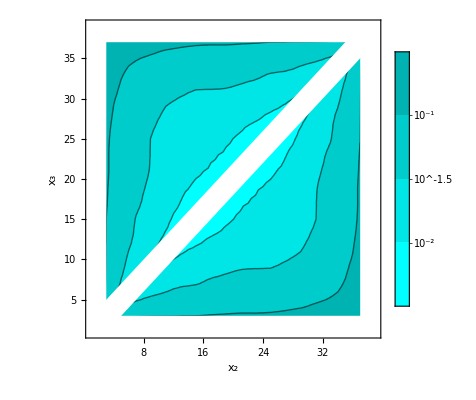

fig-eps-sig-sig-sample-10e4.pdf

```mathematica
L=40;
Table[{i,j,((L/π)Sin[20 π/L])^(-1/4)/0.2999304743017528 √(((L/π)Sin[20 π/L])^-2/0.0014561975206714428)measure0[[i,j,1]]},{i,1,39},{j,1,39}]//Flatten[#,1]&;
ListContourPlot[%,Contours->{10^-2,10^-1.5,10^-1(*,10^-0.5,1*)},PlotLegends->BarLegend[Automatic,All,"TickLabels"->(Superscript[10,#]&/@{-2,-1.5,-1})],FrameLabel->{"x_2","x_3"},ContourShading->Table[Darker[Cyan,i],{i,0,1,0.1}]];
Show[%,Graphics[{White,Rectangle[{0,0},{40,3}]}],Graphics[{White,Rectangle[{0,0},{3,40}]}],Graphics[{White,Rectangle[{0,37},{40,40}]}],Graphics[{White,Rectangle[{37,0},{40,40}]}],Graphics[{White,Polygon[{{0,2},{2,0},{52,50},{50,52}}]}]]
Export["fig-eps-sig-sig-sample-10e4.pdf",%]
```

#### sampel size 10^5

```mathematica
measure0(*sample size 10^5*)={{{0.12421279157294633,0.000173834294348671},{0.10923919929954218,0.00016235633565857196},{0.10402263792199896,0.00014621734962367853},{0.10446496074267432,0.00015145303028681883},{0.10180709894576745,0.00014932003954108158},{0.1001821032119714,0.00015107377406559162},{0.09811698848161052,0.00015025973127692804},{0.09663377378735988,0.00015108515441195248},{0.09536916315398161,0.00015065996326256168},{0.09433779743522819,0.00015125872695297913},{0.09322517141910024,0.000150973921472547},{0.09238462271972293,0.00015134148895906693},{0.09165851439659577,0.00015116380532928173},{0.09101466466284386,0.00015144915159524377},{0.09058074718234267,0.00015128169008953588},{0.09036197038571667,0.00015147045480543673},{0.09005892044471565,0.00015132289703688695},{0.08995753629090257,0.00015151051501521495},{0.09016571337771474,0.00015134714671162204},{0.09055503755877711,0.00015152714770839317},{0.09119775496871485,0.00015126436064091976},{0.09203628755877796,0.00015137121894588713},{0.09292083837771649,0.00015112855591112726},{0.09407466129090523,0.00015118160428816843},{0.09546442044471905,0.00015086943672508243},{0.09688647038572049,0.00015096075198820855},{0.09858362218234228,0.00015062518867407177},{0.10064578966282363,0.00015068318151384135},{0.1029843893965504,0.00015017013503456787},{0.10582462271964768,0.000150255327209951},{0.10950029641898727,0.00014944123488400192},{0.11389979743507192,0.00014954295018551858},{0.1193295381537744,0.00014832883127889992},{0.12653552378708832,0.00014844461244204168},{0.13633761348126083,0.00014579643381192842},{0.15123147821152969,0.0001459417580606265},{0.17658072394519078,0.0001372723864939764},{0.2659820857418053,0.00013024820625091166},{0.31784763792092263,0.00011778793911505684}},{{0.10923919929954218,0.00016235633565857196},{0.053726291573380394,0.00017572660140543526},{0.05023557429965906,0.00015537643729175086},{0.058415387922034906,0.00015168465356593625},{0.06108058574271825,0.00015055607172986322},{0.06203684894577553,0.0001512170325106079},{0.062159978211958296,0.00015065954706673944},{0.062091238481579526,0.00015103770984017722},{0.062031648787326484,0.00015070136598725623},{0.06203341315394924,0.00015106154556946785},{0.06182104743519705,0.000150854549048013},{0.061578296419069894,0.0001510513132694077},{0.06135912271969314,0.00015089547746142468},{0.061157264396566706,0.00015105720618034833},{0.061103414662816116,0.00015093036667474853},{0.06118899718231568,0.00015106619275693186},{0.06122134538569002,0.00015093453998971402},{0.06131817044468968,0.00015103621638540854},{0.061568661290877194,0.00015092295666970635},{0.062037213377689825,0.00015105519897043665},{0.06273503755875275,0.00015085590856167704},{0.06355612996869117,0.00015093428367045123},{0.06447441255875505,0.00015078261630686982},{0.0655040883776942,0.00015082585025029846},{0.0666995362908833,0.00015059732070622564},{0.06795604544469758,0.00015065819399980908},{0.06933797038569973,0.0001504269910665127},{0.07103549718232731,0.0001505240392372581},{0.0730435396628303,0.0001501753084700778},{0.07541788939658337,0.00015026362337010172},{0.07842237271971231,0.0001496756222577776},{0.08208729641909204,0.0001498203050479432},{0.08665342243522271,0.00014897192526589005},{0.09265878815397971,0.0001491960911235895},{0.10097702378732949,0.00014718962595862238},{0.11350023848144629,0.00014763375743554055},{0.13535022821163245,0.00014087800552271313},{0.20763772394507374,0.0001396464883884321},{0.2659820857418054,0.00013024820625090957}},{{0.10402263792199896,0.00014621734962367853},{0.05023557429965906,0.00015537643729175086},{0.011076541573266038,0.0001684082538415193},{0.014584074299535787,0.00015662472719268672},{0.01968888792186956,0.00014414199066818204},{0.022213835742549627,0.00014647622898688372},{0.023640223945613412,0.00014474464442366703},{0.02455835321180514,0.00014560478624583645},{0.025268488481435897,0.0001448457432310606},{0.02587589878719211,0.00014535187682499534},{0.026365038153823107,0.0001449290063940618},{0.026651672435076598,0.0001452808266284257},{0.02680842141895399,0.0001449715592351797},{0.026875872719580543,0.00014519240903171528},{0.027079889396457352,0.00014497634961989044},{0.027399914662709655,0.00014519765208559075},{0.027612622182211957,0.00014502831909066042},{0.02786272038558899,0.0001451547264084475},{0.028130295444591294,0.00014499035880249472},{0.02844878629078156,0.00014515775282837774},{0.02901183837759812,0.0001449788566171935},{0.029633037558664446,0.00014510205308497642},{0.03034200496860598,0.00014491855099929563},{0.031180162558672814,0.00014504239633285617},{0.031986463377614904,0.00014489748553032233},{0.03279816129080597,0.00014497620795968317},{0.03368742044462216,0.00014476813201676927},{0.03476534538562621,0.00014491575006087974},{0.03607874718225615,0.00014468123207840474},{0.03769141466276253,0.00014486978560297026},{0.03964188939651998,0.0001444500292764945},{0.04195499771965267,0.00014467954930424195},{0.04492867141903678,0.00014411916708349006},{0.049029297435173494,0.0001445703767547449},{0.05455103815393671,0.00014324708533546473},{0.06340277378732843,0.00014401994731173367},{0.07863023848160025,0.0001396542482744633},{0.13535022821163228,0.0001408780055227127},{0.17658072394519073,0.0001372723864939775}},{{0.10446496074267432,0.00015145303028681883},{0.058415387922034906,0.00015168465356593625},{0.014584074299535787,0.00015662472719268672},{0.007186916573266815,0.00017241933706172778},{0.008521574299577719,0.00015701283662909998},{0.01186738792194558,0.0001489938956854989},{0.013813835742615731,0.00014923366321897458},{0.015077098945665819,0.0001488654670564211},{0.015967353211846187,0.00014875236932423476},{0.01665011348146721,0.0001487984157969011},{0.017335898787214407,0.00014868140554530427},{0.017787913153837952,0.0001487888423893718},{0.0180790474350873,0.0001487027376280839},{0.018283546418961825,0.00014873796928092055},{0.018487247719586413,0.00014864848220282783},{0.018782514396460802,0.00014875305883255333},{0.019009914662710223,0.0001486874776248008},{0.019351872182208893,0.0001487494197022165},{0.019716720385582486,0.0001486388991035842},{0.020057170444581284,0.00014874130750581452},{0.02051616129076708,0.00014861564918820867},{0.021068963377577417,0.0001486930790287154},{0.021693412558637343,0.0001485949054648972},{0.022396879968572096,0.00014865068675989345},{0.023112037558632358,0.0001485600849311334},{0.023843838377569176,0.00014862981914943608},{0.02461303629075666,0.00014847244403054418},{0.025458295444571812,0.00014857088978070747},{0.02657447038557881,0.00014837023781731496},{0.02797362218221295,0.00014857853627331803},{0.029664789662723966,0.00014822522300786148},{0.03160113939648494,0.00014844398700927997},{0.034080122719621686,0.00014793847916356835},{0.03773554641901272,0.0001483727891644911},{0.04254404743515548,0.0001471883539373725},{0.050110288153927304,0.00014814504374169944},{0.0634027737873284,0.00014401994731173392},{0.11350023848144614,0.00014763375743553995},{0.15123147821153007,0.00014594175806062576}},{{0.10180709894576745,0.00014932003954108158},{0.06108058574271825,0.00015055607172986322},{0.01968888792186956,0.00014414199066818204},{0.008521574299577719,0.00015701283662909998},{0.004010916573261583,0.0001709544462982842},{0.005447824299575028,0.0001580332017425739},{0.007861137921948818,0.00014706253658668762},{0.00951508574263583,0.0001485970188299702},{0.010616973945697987,0.00014728380184029824},{0.011403103211883609,0.00014792281977440695},{0.0120899884815058,0.0001473520430878461},{0.012619148787252801,0.0001477089266237821},{0.013000163153874743,0.0001474074087914354},{0.0133185474351212,0.00014766484227125704},{0.013591171418993716,0.00014741508028624968},{0.013818747719617655,0.0001475989556450851},{0.01397326439649182,0.00014743628087974172},{0.014262789662739363,0.00014758445197097925},{0.014665747182236089,0.00014744284429932025},{0.015101970385608175,0.00014757801923899865},{0.015642670444604694,0.0001473536675983899},{0.016178161290788758,0.00014750987591840873},{0.01671496337759809,0.00014737430514380064},{0.017293912558657067,0.0001475090909795566},{0.017897629968590824,0.00014733609982674615},{0.01859428755864952,0.00014747448430785343},{0.019344463377583426,0.00014727353234000615},{0.020112661290767407,0.00014742450403821278},{0.021069295444576093,0.00014716606856782983},{0.022337595385570893,0.00014741650602246925},{0.023900247182192077,0.00014703658329574235},{0.02568516466269717,0.00014735709308956075},{0.027873514396461827,0.00014680681790492194},{0.031162997719606678,0.00014729577300269197},{0.03564017141900376,0.0001460739580488921},{0.0425440474351554,0.00014718835393737247},{0.05455103815393634,0.0001432470853354629},{0.10097702378732965,0.00014718962595862103},{0.136337613481261,0.0001457964338119287}},{{0.1001821032119714,0.00015107377406559162},{0.06203684894577553,0.0001512170325106079},{0.022213835742549627,0.00014647622898688372},{0.01186738792194558,0.0001489938956854989},{0.005447824299575028,0.0001580332017425739},{0.00291354157325403,0.00017220278210120394},{0.0038366992995722523,0.00015763830827205216},{0.005854637921947627,0.00014871981947053782},{0.0072449607426349595,0.00014928076035026342},{0.008143973945697127,0.0001487448664864698},{0.00884372821188435,0.00014876679205542726},{0.009473988481509215,0.000148666655972254},{0.009934648787258997,0.0001486417810082196},{0.010293288153883778,0.00014866569167145018},{0.010638922435133584,0.0001486273405186977},{0.010902171419008493,0.0001486469315599833},{0.011000997719633145,0.00014857403486723836},{0.011244514396507718,0.00014863109382075773},{0.011607164662757161,0.0001485946546179747},{0.012048247182255487,0.00014868233600824252},{0.012711470385626556,0.00014852044039762906},{0.0132667954446225,0.00014859520177457595},{0.013762286290806667,0.00014851200290226936},{0.014323838377613907,0.00014858931507154415},{0.014835662558672053,0.0001484861653271754},{0.015430879968605007,0.0001485655445483656},{0.016151787558662884,0.00014843027445617967},{0.016907588377596212,0.00014855008465104193},{0.017770036290779084,0.00014833717657397323},{0.018895670444585504,0.00014849876440336656},{0.02035922038557855,0.0001481477041410316},{0.022036372182196555,0.00014847057846802963},{0.024083164662690955,0.00014800677189501072},{0.027046889396455456,0.00014844926461930386},{0.03116299771960744,0.000147295773002693},{0.037735546419012916,0.00014837278916449248},{0.049029297435173515,0.0001445703767547479},{0.09265878815397986,0.00014919609112358861},{0.1265355237870885,0.0001484446124420373}},{{0.09811698848161052,0.00015025973127692804},{0.062159978211958296,0.00015065954706673944},{0.023640223945613412,0.00014474464442366703},{0.013813835742615731,0.00014923366321897458},{0.007861137921948818,0.00014706253658668762},{0.0038366992995722523,0.00015763830827205216},{0.0020340415732514644,0.00017154643070805745},{0.0030428242995687344,0.00015826325608938737},{0.004672387921946492,0.00014778499027625632},{0.005765460742634015,0.00014912562142843953},{0.006517848945696322,0.00014796468671468517},{0.007151478211883722,0.00014845082367973458},{0.007719738481508596,0.00014794679241683805},{0.008148648787258541,0.00014824499342238164},{0.008518163153883375,0.00014799305667056894},{0.00883067243513318,0.0001482245872137797},{0.008931921419008053,0.00014801088188736138},{0.009137372719632943,0.0001481482143450272},{0.009503139396507937,0.00014797909197919768},{0.009937914662757752,0.00014816214809136062},{0.01055499718225759,0.0001479730136904217},{0.01118009538563173,0.00014810748585010572},{0.011716670444630532,0.00014791241453156558},{0.012232411290816696,0.00014804388434453517},{0.012702213377627005,0.00014790134475675193},{0.013210287558685689,0.00014806972342728338},{0.013865379968617956,0.0001478563296205239},{0.014598162558674304,0.00014804810625234193},{0.015408213377605912,0.00014782164646929706},{0.016410911290787318,0.00014803165882845267},{0.017707170444592035,0.00014762441560658377},{0.019328095385583485,0.00014796733974068303},{0.02130399718219964,0.00014747091700584},{0.02408316466269121,0.0001480067718950116},{0.027873514396461803,0.00014680681790491985},{0.03408012271962247,0.00014793847916356797},{0.0449286714190373,0.00014411916708349288},{0.08665342243522298,0.00014897192526589352},{0.11932953815377396,0.00014832883127890244}},{{0.09663377378735988,0.00015108515441195248},{0.062091238481579526,0.00015103770984017722},{0.02455835321180514,0.00014560478624583645},{0.015077098945665819,0.0001488654670564211},{0.00951508574263583,0.0001485970188299702},{0.005854637921947627,0.00014871981947053782},{0.0030428242995687344,0.00015826325608938737},{0.0018620415732504825,0.00017207905916342563},{0.0025725742995651255,0.00015782707910812818},{0.003908887921944902,0.00014862408230864209},{0.004773460742633097,0.00014932630953010326},{0.00541272394569557,0.00014864192951382464},{0.00599847821188311,0.00014873376041531935},{0.0064718634815080205,0.00014859349241462704},{0.0069013987872579745,0.0001485914558335898},{0.00728816315388288,0.0001485701630192789},{0.007435047435132726,0.00014857273703707097},{0.007573171419007626,0.00014857778489817784},{0.007905747719632563,0.00014848812262657933},{0.008336264396507595,0.00014858522328603125},{0.00891416466275762,0.00014849228320513373},{0.009574372182257724,0.0001485766742013589},{0.010179345385632598,0.00014846666810531365},{0.010687795444632473,0.0001484952836274368},{0.011106286290819728,0.00014839331324790198},{0.011532463377632,0.00014850620544220553},{0.012106162558693009,0.00014836778312195874},{0.01282025496862674,0.00014847522925092702},{0.01361278755868285,0.00014831524118625244},{0.014555338377612224,0.00014850464558110836},{0.015773911290791445,0.00014814810957344251},{0.017362670444594403,0.00014839096776640855},{0.019328095385583572,0.00014796733974068314},{0.02203637218219726,0.00014847057846802616},{0.02568516466269789,0.000147357093089559},{0.03160113939648667,0.00014844398700927802},{0.041954997719653095,0.00014467954930423986},{0.08208729641909238,0.00014982030504794299},{0.11389979743507234,0.00014954295018552107}},{{0.09536916315398161,0.00015065996326256168},{0.062031648787326484,0.00015070136598725623},{0.025268488481435897,0.0001448457432310606},{0.015967353211846187,0.00014875236932423476},{0.010616973945697987,0.00014728380184029824},{0.0072449607426349595,0.00014928076035026342},{0.004672387921946492,0.00014778499027625632},{0.0025725742995651255,0.00015782707910812818},{0.0015186665732493225,0.00017170427003347657},{0.002113199299563113,0.00015832458271229524},{0.0031628879219430493,0.00014806224417396636},{0.003927960742632167,0.00014925287315057533},{0.004537848945694778,0.0001481590439909336},{0.005034853211882357,0.00014858471393956022},{0.005506238481507289,0.00014813762070029217},{0.005955398787257307,0.0001483891960817983},{0.0061872881538822,0.000148147676299513},{0.006350672435132164,0.00014836682723351897},{0.006579796419007018,0.00014814422428718058},{0.007014622719632203,0.00014833384286600472},{0.007603764396507333,0.00014813081094231014},{0.008204289662757434,0.00014829891521822146},{0.008874872182257642,0.0001481248158106899},{0.009439970385632676,0.00014822122418620349},{0.009798170444632603,0.00014803190270747024},{0.010180161290820118,0.00014819279572518006},{0.010694588377632704,0.00014801270823511657},{0.011381662558695023,0.00014820862111070322},{0.012157879968630799,0.00014795730645151384},{0.013002537558688047,0.00014821244120923242},{0.014193088377615841,0.0001478389888352749},{0.015773911290791788,0.00014814810957344295},{0.01770717044459238,0.00014762441560658393},{0.020359220385579004,0.0001481477041410339},{0.023900247182192996,0.00014703658329574324},{0.029664789662725843,0.00014822522300786352},{0.0396418893965207,0.00014445002927649503},{0.07842237271971268,0.00014967562225778154},{0.10950029641898923,0.00014944123488400373}},{{0.09433779743522819,0.00015125872695297913},{0.06203341315394924,0.00015106154556946785},{0.02587589878719211,0.00014535187682499534},{0.01665011348146721,0.0001487984157969011},{0.011403103211883609,0.00014792281977440695},{0.008143973945697127,0.0001487448664864698},{0.005765460742634015,0.00014912562142843953},{0.003908887921944902,0.00014862408230864209},{0.002113199299563113,0.00015832458271229524},{0.0012157915732494695,0.0001720998742606743},{0.0016850742995616448,0.00015805601293136765},{0.002619887921940318,0.00014862801373267877},{0.0033753357426308354,0.00014940284471042314},{0.003948973945693869,0.00014866047456880784},{0.004419728211881859,0.00014879270640806203},{0.004840988481506783,0.00014860896142175094},{0.005157773787256961,0.0001486265006431311},{0.005440538153881823,0.000148611625860346},{0.005658672435131662,0.00014860071931767406},{0.005973796419006745,0.00014864310372611914},{0.006540747719631941,0.00014853567708472188},{0.007088889396507043,0.00014858529647985107},{0.007713789662757254,0.00014851558032012572},{0.008399372182257451,0.00014856806066489123},{0.008799470385632427,0.00014844003023965562},{0.009152670444632416,0.00014850666486907342},{0.009681661290819972,0.0001483815550743164},{0.010334963377632655,0.00014851983275894872},{0.011122537558695153,0.00014836342268291158},{0.011943629968630827,0.0001485336931189714},{0.013002537558687957,0.00014821244120923185},{0.014555338377612496,0.00014850464558110928},{0.01641091129078763,0.00014803165882845175},{0.018895670444586163,0.00014849876440336897},{0.022337595385572288,0.00014741650602246898},{0.027973622182214275,0.00014857853627331537},{0.037691414662763094,0.00014486978560296942},{0.07541788939658339,0.00015026362337009494},{0.10582462271964815,0.00015025532720995078}},{{0.09322517141910024,0.000150973921472547},{0.06182104743519705,0.000150854549048013},{0.026365038153823107,0.0001449290063940618},{0.017335898787214407,0.00014868140554530427},{0.0120899884815058,0.0001473520430878461},{0.00884372821188435,0.00014876679205542726},{0.006517848945696322,0.00014796468671468517},{0.004773460742633097,0.00014932630953010326},{0.0031628879219430493,0.00014806224417396636},{0.0016850742995616448,0.00015805601293136765},{0.000962541573250132,0.00017184454681147738},{0.0014274492995617956,0.0001583540248590739},{0.0023021379219398007,0.00014823861477797692},{0.0029742107426284567,0.00014935680912445611},{0.0034865989456922927,0.0001483065649701152},{0.003923853211880544,0.00014869698114665145},{0.004271363481506294,0.00014827141393908893},{0.004645023787256451,0.00014852869266758582},{0.004941913153881643,0.00014830196134219215},{0.005211047435131717,0.00014853989354050515},{0.005686046419006687,0.0001482774854064311},{0.006234997719631812,0.0001484235563919354},{0.006784764396507053,0.00014827005494609137},{0.0074625396627572265,0.00014840595379692477},{0.008012497182257364,0.00014823324012910486},{0.008351845385632339,0.0001483403677341479},{0.008808295444632306,0.00014814093396712245},{0.009456161290819916,0.00014833290886918173},{0.010250588377632696,0.00014810704887033087},{0.011122537558695236,0.0001483634226829112},{0.012157879968630889,0.00014795730645151132},{0.013612787558682721,0.00014831524118625106},{0.015408213377606153,0.00014782164646929942},{0.017770036290779702,0.00014833717657397266},{0.0210692954445773,0.00014716606856783368},{0.026574470385580484,0.00014837023781731244},{0.036078747182256135,0.00014468123207840526},{0.07304353966282975,0.00015017530847007916},{0.10298438939655051,0.00015017013503456692}},{{0.09238462271972293,0.00015134148895906693},{0.061578296419069894,0.0001510513132694077},{0.026651672435076598,0.0001452808266284257},{0.017787913153837952,0.0001487888423893718},{0.012619148787252801,0.0001477089266237821},{0.009473988481509215,0.000148666655972254},{0.007151478211883722,0.00014845082367973458},{0.00541272394569557,0.00014864192951382464},{0.003927960742632167,0.00014925287315057533},{0.002619887921940318,0.00014862801373267877},{0.0014274492995617956,0.0001583540248590739},{0.000825291573248725,0.00017208444933316348},{0.001221699299562068,0.00015812713255401712},{0.0019581379219381413,0.00014860959899634196},{0.0025783357426264865,0.0001494278454206081},{0.0031078489456904633,0.00014866469374494166},{0.003495228211879539,0.00014882146820729392},{0.003911863481505564,0.00014859955289736655},{0.004246023787256079,0.0001486361727491041},{0.004602163153881395,0.00014865935811942107},{0.005091172435131582,0.00014860801680972638},{0.00560867141900658,0.00014860294525788557},{0.006150247719631939,0.00014852265300283754},{0.006707264396507129,0.00014856348917632447},{0.007320289662757253,0.00014848949080143212},{0.007768872182257295,0.00014854771028433524},{0.008134345385632243,0.0001484072809601324},{0.00871042044463236,0.00014849728038105755},{0.009456161290820138,0.00014833290886917893},{0.010334963377632754,0.00014851983275895018},{0.011381662558695282,0.00014820862111070382},{0.012820254968626538,0.00014847522925092756},{0.014598162558674951,0.0001480481062523401},{0.016907588377597624,0.0001485500846510415},{0.02011266129076871,0.0001474245040382171},{0.025458295444573856,0.00014857088978070888},{0.034765345385624924,0.00014491575006087982},{0.07103549718232698,0.00015052403923725916},{0.10064578966282363,0.00015068318151384}},{{0.09165851439659577,0.00015116380532928173},{0.06135912271969314,0.00015089547746142468},{0.02680842141895399,0.0001449715592351797},{0.0180790474350873,0.0001487027376280839},{0.013000163153874743,0.0001474074087914354},{0.009934648787258997,0.0001486417810082196},{0.007719738481508596,0.00014794679241683805},{0.00599847821188311,0.00014873376041531935},{0.004537848945694778,0.0001481590439909336},{0.0033753357426308354,0.00014940284471042314},{0.0023021379219398007,0.00014823861477797692},{0.001221699299562068,0.00015812713255401712},{0.0006989165732491066,0.00017191412658689877},{0.001017199299562284,0.00015837149960455134},{0.001701637921937976,0.00014832589968793558},{0.002355585742626703,0.00014942913179788085},{0.002785348945689546,0.0001484174400074963},{0.003228228211878617,0.00014878023063865986},{0.003622863481504907,0.00014835682666633075},{0.003944148787255213,0.0001486311921183638},{0.0044936631538808535,0.00014835841153043938},{0.005057797435131328,0.00014856736642334677},{0.0055321714190066556,0.0001483422682651165},{0.006062372719631924,0.000148486093963899},{0.006658389396507071,0.0001482963104549523},{0.00722941466275723,0.0001484712563767311},{0.007686497182257237,0.00014830695473320803},{0.008134345385632328,0.00014840728096013328},{0.00880829544463253,0.00014814093396711976},{0.009681661290820223,0.00014838155507431317},{0.010694588377632859,0.00014801270823511844},{0.012106162558693054,0.00014836778312196137},{0.013865379968618469,0.0001478563296205246},{0.016151787558665094,0.00014843027445617866},{0.019344463377585792,0.00014727353234000493},{0.024613036290758807,0.000148472444030547},{0.033687420444619816,0.00014476813201676883},{0.06933797038569957,0.00015042699106651051},{0.09858362218234286,0.0001506251886740735}},{{0.09101466466284386,0.00015144915159524377},{0.061157264396566706,0.00015105720618034833},{0.026875872719580543,0.00014519240903171528},{0.018283546418961825,0.00014873796928092055},{0.0133185474351212,0.00014766484227125704},{0.010293288153883778,0.00014866569167145018},{0.008148648787258541,0.00014824499342238164},{0.0064718634815080205,0.00014859349241462704},{0.005034853211882357,0.00014858471393956022},{0.003948973945693869,0.00014866047456880784},{0.0029742107426284567,0.00014935680912445611},{0.0019581379219381413,0.00014860959899634196},{0.001017199299562284,0.00015837149960455134},{0.0005866665732500885,0.00017208656511537125},{0.0008670742995619184,0.00015819037998291287},{0.001541887921937538,0.00014861640682281823},{0.0020638357426255674,0.00014945749842661896},{0.0024867239456887536,0.00014868589326784147},{0.0029248532118781607,0.00014883742916804049},{0.003302863481503591,0.00014864718488872812},{0.003790148787254724,0.00014863121680911773},{0.004400163153880714,0.0001486117124608991},{0.004907922435131361,0.00014859777808191925},{0.005411171419006744,0.0001485897031133242},{0.005974497719631978,0.00014848416323370061},{0.006581639396507133,0.000148531347429608},{0.007229414662757224,0.00014847125637672766},{0.007768872182257339,0.00014854771028433768},{0.00835184538563246,0.00014834036773415054},{0.009152670444632558,0.00014850666486907106},{0.010180161290820248,0.0001481927957251802},{0.011532463377632305,0.0001485062054422048},{0.013210287558686246,0.00014806972342728565},{0.015430879968607446,0.00014856554454836725},{0.018594287558652577,0.00014747448430785408},{0.02384383837757061,0.0001486298191494389},{0.03279816129080311,0.00014497620795968357},{0.06795604544469754,0.00015065819399981292},{0.0968864703857208,0.00015096075198820923}},{{0.09058074718234267,0.00015128169008953588},{0.061103414662816116,0.00015093036667474853},{0.027079889396457352,0.00014497634961989044},{0.018487247719586413,0.00014864848220282783},{0.013591171418993716,0.00014741508028624968},{0.010638922435133584,0.0001486273405186977},{0.008518163153883375,0.00014799305667056894},{0.0069013987872579745,0.0001485914558335898},{0.005506238481507289,0.00014813762070029217},{0.004419728211881859,0.00014879270640806203},{0.0034865989456922927,0.0001483065649701152},{0.0025783357426264865,0.0001494278454206081},{0.001701637921937976,0.00014832589968793558},{0.0008670742995619184,0.00015819037998291287},{0.0004395415732499089,0.00017194032031624587},{0.0006905742995622748,0.00015834298965936667},{0.0012228879219369614,0.00014837969313713606},{0.001724085742625046,0.00014946248723174353},{0.002171723945688472,0.00014844786934848825},{0.002652603211876685,0.00014885770689331937},{0.00317011348150327,0.00014836014663046924},{0.0037138987872546185,0.0001486104729534562},{0.004285663153880597,0.0001483531825009085},{0.004833922435131399,0.0001485510873601507},{0.00534967141900669,0.00014831771391407306},{0.005974497719631841,0.00014848416323370018},{0.006658389396507076,0.0001482963104549546},{0.007320289662757266,0.00014848949080143117},{0.008012497182257347,0.00014823324012910156},{0.008799470385632424,0.0001484400302396567},{0.009798170444632616,0.0001480319027074752},{0.01110628629081992,0.00014839331324790063},{0.012702213377627381,0.0001479013447567515},{0.014835662558673897,0.0001484861653271773},{0.017897629968593655,0.00014733609982674615},{0.023112037558634575,0.00014856008493113529},{0.03198646337761183,0.00014489748553032778},{0.06669953629088292,0.00015059732070622322},{0.09546442044471941,0.00015086943672507896}},{{0.09036197038571667,0.00015147045480543673},{0.06118899718231568,0.00015106619275693186},{0.027399914662709655,0.00014519765208559075},{0.018782514396460802,0.00014875305883255333},{0.013818747719617655,0.0001475989556450851},{0.010902171419008493,0.0001486469315599833},{0.00883067243513318,0.0001482245872137797},{0.00728816315388288,0.0001485701630192789},{0.005955398787257307,0.0001483891960817983},{0.004840988481506783,0.00014860896142175094},{0.003923853211880544,0.00014869698114665145},{0.0031078489456904633,0.00014866469374494166},{0.002355585742626703,0.00014942913179788085},{0.001541887921937538,0.00014861640682281823},{0.0006905742995622748,0.00015834298965936667},{0.0002726665732498426,0.00017209083890374773},{0.0004895742995620645,0.00015828183478693264},{0.001046637921936578,0.00014862429298501028},{0.0015650857426242615,0.00014946680533606675},{0.0021187239456876015,0.0001487007770756087},{0.0027062282118770543,0.00014879988801093987},{0.003207113481503718,0.00014861018475725328},{0.0037051487872546618,0.00014862093688134764},{0.004258288153880623,0.00014858640973264173},{0.004833922435131526,0.00014855108736015044},{0.005411171419006661,0.00014858970311332624},{0.006062372719631889,0.00014848609396390038},{0.006707264396507122,0.0001485634891763214},{0.007462539662757212,0.00014840595379692474},{0.008399372182257338,0.0001485680606648904},{0.009439970385632514,0.0001482212241862026},{0.010687795444632261,0.00014849528362743925},{0.012232411290817211,0.00014804388434453255},{0.014323838377615077,0.0001485893150715436},{0.017293912558658923,0.00014750909097955905},{0.022396879968573813,0.00014865068675989232},{0.03118016255867049,0.00014504239633285386},{0.06550408837769366,0.00015082585025030015},{0.09407466129090539,0.00015118160428816924}},{{0.09005892044471565,0.00015132289703688695},{0.06122134538569002,0.00015093453998971402},{0.027612622182211957,0.00014502831909066042},{0.019009914662710223,0.0001486874776248008},{0.01397326439649182,0.00014743628087974172},{0.011000997719633145,0.00014857403486723836},{0.008931921419008053,0.00014801088188736138},{0.007435047435132726,0.00014857273703707097},{0.0061872881538822,0.000148147676299513},{0.005157773787256961,0.0001486265006431311},{0.004271363481506294,0.00014827141393908893},{0.003495228211879539,0.00014882146820729392},{0.002785348945689546,0.0001484174400074963},{0.0020638357426255674,0.00014945749842661896},{0.0012228879219369614,0.00014837969313713606},{0.0004895742995620645,0.00015828183478693264},{0.00023004157325011768,0.00017197432278413322},{0.0005151992995623858,0.00015834838170539214},{0.0010151379219362415,0.00014841773948289844},{0.0016419607426244698,0.0001495117512575631},{0.0023097239456884456,0.0001484624835418108},{0.0028061032118776785,0.0001488347695549577},{0.0032314884815040066,0.00014839070566767534},{0.003705148787254763,0.00014862093688134754},{0.0042856631538809396,0.00014835318250090764},{0.004907922435131197,0.00014859777808191906},{0.0055321714190067015,0.000148342268265116},{0.00615024771963203,0.00014852265300283691},{0.006784764396507158,0.00014827005494608852},{0.0077137896627572046,0.00014851558032012843},{0.008874872182257418,0.00014812481581068926},{0.010179345385632463,0.00014846666810531297},{0.011716670444630754,0.00014791241453156434},{0.013762286290807639,0.00014851200290227074},{0.016714963377599226,0.00014737430514380083},{0.021693412558638114,0.00014859490546489888},{0.030342004968603484,0.00014491855099929302},{0.06447441255875491,0.00015078261630686825},{0.09292083837771682,0.0001511285559111277}},{{0.08995753629090257,0.00015151051501521495},{0.06131817044468968,0.00015103621638540854},{0.02786272038558899,0.0001451547264084475},{0.019351872182208893,0.0001487494197022165},{0.014262789662739363,0.00014758445197097925},{0.011244514396507718,0.00014863109382075773},{0.009137372719632943,0.0001481482143450272},{0.007573171419007626,0.00014857778489817784},{0.006350672435132164,0.00014836682723351897},{0.005440538153881823,0.000148611625860346},{0.004645023787256451,0.00014852869266758582},{0.003911863481505564,0.00014859955289736655},{0.003228228211878617,0.00014878023063865986},{0.0024867239456887536,0.00014868589326784147},{0.001724085742625046,0.00014946248723174353},{0.001046637921936578,0.00014862429298501028},{0.0005151992995623858,0.00015834838170539214},{0.00028504157324835486,0.00017210492206727666},{0.0004853242995615478,0.00015831140979915482},{0.001035887921936806,0.00014867923073110924},{0.0017392107426251688,0.0001494705555292741},{0.002370973945688969,0.00014868908336529709},{0.002806103211877886,0.00014883476955495587},{0.0032071134815037676,0.00014861018475725282},{0.003713898787255027,0.00014861047295345703},{0.004400163153880898,0.0001486117124609012},{0.005057797435131314,0.00014856736642334756},{0.005608671419006764,0.000148602945257888},{0.006234997719632106,0.0001484235563919333},{0.0070888893965072005,0.00014858529647984996},{0.008204289662757415,0.00014829891521821894},{0.00957437218225763,0.00014857667420135797},{0.011180095385631776,0.0001481074858501045},{0.013266795444623416,0.00014859520177457639},{0.01617816129078969,0.0001475098759184116},{0.021068963377577223,0.00014869307902871503},{0.02963303755866214,0.00014510205308497406},{0.06355612996869126,0.00015093428367044992},{0.0920362875587786,0.0001513712189458893}},{{0.09016571337771474,0.00015134714671162204},{0.061568661290877194,0.00015092295666970635},{0.028130295444591294,0.00014499035880249472},{0.019716720385582486,0.0001486388991035842},{0.014665747182236089,0.00014744284429932025},{0.011607164662757161,0.0001485946546179747},{0.009503139396507937,0.00014797909197919768},{0.007905747719632563,0.00014848812262657933},{0.006579796419007018,0.00014814422428718058},{0.005658672435131662,0.00014860071931767406},{0.004941913153881643,0.00014830196134219215},{0.004246023787256079,0.0001486361727491041},{0.003622863481504907,0.00014835682666633075},{0.0029248532118781607,0.00014883742916804049},{0.002171723945688472,0.00014844786934848825},{0.0015650857426242615,0.00014946680533606675},{0.0010151379219362415,0.00014841773948289844},{0.0004853242995615478,0.00015831140979915482},{0.00026341657324848773,0.00017198322809080477},{0.0005019492995621287,0.00015834027336564233},{0.001042887921937263,0.00014838773343860774},{0.0017392107426244107,0.00014947055552927318},{0.0023097239456887284,0.00014846248354181342},{0.0027062282118777065,0.00014879988801093946},{0.0031701134815038294,0.0001483601466304642},{0.0037901487872554,0.00014863121680911868},{0.0044936631538812655,0.0001483584115304399},{0.005091172435131657,0.0001486080168097254},{0.0056860464190069595,0.00014827748540643102},{0.006540747719632136,0.00014853567708471844},{0.007603764396507362,0.000148130810942309},{0.008914164662757572,0.00014849228320513332},{0.010554997182257575,0.0001479730136904236},{0.01271147038562694,0.00014852044039762749},{0.015642670444605093,0.00014735366759838846},{0.020516161290766048,0.00014861564918820954},{0.02901183837759606,0.00014497885661719404},{0.06273503755875258,0.0001508559085616762},{0.09119775496871545,0.00015126436064091898}},{{0.09055503755877711,0.00015152714770839317},{0.062037213377689825,0.00015105519897043665},{0.02844878629078156,0.00014515775282837774},{0.020057170444581284,0.00014874130750581452},{0.015101970385608175,0.00014757801923899865},{0.012048247182255487,0.00014868233600824252},{0.009937914662757752,0.00014816214809136062},{0.008336264396507595,0.00014858522328603125},{0.007014622719632203,0.00014833384286600472},{0.005973796419006745,0.00014864310372611914},{0.005211047435131717,0.00014853989354050515},{0.004602163153881395,0.00014865935811942107},{0.003944148787255213,0.0001486311921183638},{0.003302863481503591,0.00014864718488872812},{0.002652603211876685,0.00014885770689331937},{0.0021187239456876015,0.0001487007770756087},{0.0016419607426244698,0.0001495117512575631},{0.001035887921936806,0.00014867923073110924},{0.0005019492995621287,0.00015834027336564233},{0.0003015415732502992,0.00024344826691701248},{0.0005019492995622738,0.00015834027336564434},{0.001035887921936409,0.00014867923073111168},{0.0016419607426246177,0.0001495117512575625},{0.002118723945688015,0.0001487007770756093},{0.0026526032118773172,0.0001488577068933195},{0.003302863481504396,0.00014864718488873015},{0.003944148787255406,0.00014863119211836438},{0.0046021631538810445,0.0001486593581194231},{0.005211047435131537,0.00014853989354050623},{0.005973796419007075,0.00014864310372611936},{0.00701462271963225,0.0001483338428660005},{0.008336264396507465,0.0001485852232860298},{0.009937914662757475,0.00014816214809135756},{0.012048247182255946,0.0001486823360082394},{0.015101970385608565,0.00014757801923899927},{0.020057170444580406,0.00014874130750581652},{0.02844878629078008,0.00014515775282837687},{0.06203721337768939,0.0001510551989704361},{0.09055503755877752,0.0001515271477083914}},{{0.09119775496871485,0.00015126436064091976},{0.06273503755875275,0.00015085590856167704},{0.02901183837759812,0.0001449788566171935},{0.02051616129076708,0.00014861564918820867},{0.015642670444604694,0.0001473536675983899},{0.012711470385626556,0.00014852044039762906},{0.01055499718225759,0.0001479730136904217},{0.00891416466275762,0.00014849228320513373},{0.007603764396507333,0.00014813081094231014},{0.006540747719631941,0.00014853567708472188},{0.005686046419006687,0.0001482774854064311},{0.005091172435131582,0.00014860801680972638},{0.0044936631538808535,0.00014835841153043938},{0.003790148787254724,0.00014863121680911773},{0.00317011348150327,0.00014836014663046924},{0.0027062282118770543,0.00014879988801093987},{0.0023097239456884456,0.0001484624835418108},{0.0017392107426251688,0.0001494705555292741},{0.001042887921937263,0.00014838773343860774},{0.0005019492995622738,0.00015834027336564434},{0.00026341657324849364,0.00017198322809080333},{0.0004853242995617721,0.0001583114097991549},{0.0010151379219368966,0.0001484177394828974},{0.001565085742624623,0.0001494668053360671},{0.002171723945688951,0.00014844786934849064},{0.0029248532118783775,0.00014883742916803937},{0.003622863481505256,0.0001483568266663329},{0.004246023787255644,0.00014863617274910365},{0.0049419131538814,0.0001483019613421896},{0.005658672435131965,0.0001486007193176734},{0.0065797964190072895,0.00014814422428718527},{0.007905747719632485,0.00014848812262657914},{0.00950313939650782,0.00014797909197919936},{0.011607164662757276,0.00014859465461797617},{0.014665747182236394,0.00014744284429932085},{0.019716720385581737,0.00014863889910358543},{0.028130295444590787,0.0001449903588024924},{0.061568661290876646,0.0001509229566697025},{0.09016571337771499,0.00015134714671161904}},{{0.09203628755877796,0.00015137121894588713},{0.06355612996869117,0.00015093428367045123},{0.029633037558664446,0.00014510205308497642},{0.021068963377577417,0.0001486930790287154},{0.016178161290788758,0.00014750987591840873},{0.0132667954446225,0.00014859520177457595},{0.01118009538563173,0.00014810748585010572},{0.009574372182257724,0.0001485766742013589},{0.008204289662757434,0.00014829891521822146},{0.007088889396507043,0.00014858529647985107},{0.006234997719631812,0.0001484235563919354},{0.00560867141900658,0.00014860294525788557},{0.005057797435131328,0.00014856736642334677},{0.004400163153880714,0.0001486117124608991},{0.0037138987872546185,0.0001486104729534562},{0.003207113481503718,0.00014861018475725328},{0.0028061032118776785,0.0001488347695549577},{0.002370973945688969,0.00014868908336529709},{0.0017392107426244107,0.00014947055552927318},{0.001035887921936409,0.00014867923073111168},{0.0004853242995617721,0.0001583114097991549},{0.00028504157324889425,0.00017210492206727807},{0.0005151992995613971,0.00015834838170539456},{0.0010466379219365952,0.00014862429298500906},{0.0017240857426254479,0.00014946248723174218},{0.0024867239456895255,0.0001486858932678413},{0.0032282282118790413,0.00014878023063866043},{0.003911863481505521,0.00014859955289736617},{0.00464502378725644,0.00014852869266758324},{0.005440538153881823,0.00014861162586034526},{0.006350672435132201,0.00014836682723351664},{0.0075731714190075934,0.00014857778489817808},{0.009137372719632945,0.0001481482143450251},{0.011244514396507727,0.00014863109382075472},{0.014262789662739193,0.0001475844519709785},{0.019351872182207654,0.00014874941970221671},{0.027862720385588815,0.00014515472640844605},{0.061318170444689325,0.00015103621638540908},{0.08995753629090289,0.00015151051501521422}},{{0.09292083837771649,0.00015112855591112726},{0.06447441255875505,0.00015078261630686982},{0.03034200496860598,0.00014491855099929563},{0.021693412558637343,0.0001485949054648972},{0.01671496337759809,0.00014737430514380064},{0.013762286290806667,0.00014851200290226936},{0.011716670444630532,0.00014791241453156558},{0.010179345385632598,0.00014846666810531365},{0.008874872182257642,0.0001481248158106899},{0.007713789662757254,0.00014851558032012572},{0.006784764396507053,0.00014827005494609137},{0.006150247719631939,0.00014852265300283754},{0.0055321714190066556,0.0001483422682651165},{0.004907922435131361,0.00014859777808191925},{0.004285663153880597,0.0001483531825009085},{0.0037051487872546618,0.00014862093688134764},{0.0032314884815040066,0.00014839070566767534},{0.002806103211877886,0.00014883476955495587},{0.0023097239456887284,0.00014846248354181342},{0.0016419607426246177,0.0001495117512575625},{0.0010151379219368966,0.0001484177394828974},{0.0005151992995613971,0.00015834838170539456},{0.00023004157324961786,0.0001719743227841338},{0.0004895742995625327,0.00015828183478692977},{0.0012228879219363911,0.00014837969313714094},{0.002063835742626368,0.00014945749842661758},{0.002785348945690713,0.00014841744000749477},{0.0034952282118796228,0.00014882146820729278},{0.004271363481506003,0.000148271413939093},{0.005157773787257004,0.00014862650064313175},{0.006187288153882351,0.00014814767629951593},{0.007435047435132787,0.00014857273703707303},{0.00893192141900813,0.0001480108818873598},{0.011000997719633157,0.0001485740348672382},{0.013973264396491792,0.0001474362808797425},{0.019009914662708922,0.00014868747762480157},{0.027612622182212034,0.00014502831909065877},{0.061221345385689886,0.000150934539989716},{0.09005892044471614,0.00015132289703688478}},{{0.09407466129090523,0.00015118160428816843},{0.0655040883776942,0.00015082585025029846},{0.031180162558672814,0.00014504239633285617},{0.022396879968572096,0.00014865068675989345},{0.017293912558657067,0.0001475090909795566},{0.014323838377613907,0.00014858931507154415},{0.012232411290816696,0.00014804388434453517},{0.010687795444632473,0.0001484952836274368},{0.009439970385632676,0.00014822122418620349},{0.008399372182257451,0.00014856806066489123},{0.0074625396627572265,0.00014840595379692477},{0.006707264396507129,0.00014856348917632447},{0.006062372719631924,0.000148486093963899},{0.005411171419006744,0.0001485897031133242},{0.004833922435131399,0.0001485510873601507},{0.004258288153880623,0.00014858640973264173},{0.003705148787254763,0.00014862093688134754},{0.0032071134815037676,0.00014861018475725282},{0.0027062282118777065,0.00014879988801093946},{0.002118723945688015,0.0001487007770756093},{0.001565085742624623,0.0001494668053360671},{0.0010466379219365952,0.00014862429298500906},{0.0004895742995625327,0.00015828183478692977},{0.00027266657324985196,0.00017209083890374588},{0.0006905742995621022,0.00015834298965936917},{0.0015418879219380333,0.00014861640682281688},{0.0023555857426268384,0.00014942913179787987},{0.0031078489456910405,0.0001486646937449421},{0.0039238532118810975,0.00014869698114665183},{0.0048409884815069975,0.00014860896142175216},{0.0059553987872576165,0.00014838919608180007},{0.007288163153882954,0.0001485701630192794},{0.008830672435133212,0.00014822458721377616},{0.01090217141900858,0.0001486469315599837},{0.013818747719618125,0.00014759895564508895},{0.01878251439645947,0.00014875305883255529},{0.027399914662709766,0.00014519765208559384},{0.061188997182315435,0.00015106619275693603},{0.09036197038571707,0.0001514704548054383}},{{0.09546442044471905,0.00015086943672508243},{0.0666995362908833,0.00015059732070622564},{0.031986463377614904,0.00014489748553032233},{0.023112037558632358,0.0001485600849311334},{0.017897629968590824,0.00014733609982674615},{0.014835662558672053,0.0001484861653271754},{0.012702213377627005,0.00014790134475675193},{0.011106286290819728,0.00014839331324790198},{0.009798170444632603,0.00014803190270747024},{0.008799470385632427,0.00014844003023965562},{0.008012497182257364,0.00014823324012910486},{0.007320289662757253,0.00014848949080143212},{0.006658389396507071,0.0001482963104549523},{0.005974497719631978,0.00014848416323370061},{0.00534967141900669,0.00014831771391407306},{0.004833922435131526,0.00014855108736015044},{0.0042856631538809396,0.00014835318250090764},{0.003713898787255027,0.00014861047295345703},{0.0031701134815038294,0.0001483601466304642},{0.0026526032118773172,0.0001488577068933195},{0.002171723945688951,0.00014844786934849064},{0.0017240857426254479,0.00014946248723174218},{0.0012228879219363911,0.00014837969313714094},{0.0006905742995621022,0.00015834298965936917},{0.0004395415732485944,0.0001719403203162484},{0.0008670742995615028,0.0001581903799829156},{0.0017016379219386305,0.00014832589968793885},{0.0025783357426268478,0.00014942784542060734},{0.0034865989456925052,0.000148306564970123},{0.004419728211881291,0.00014879270640806073},{0.005506238481507611,0.000148137620700289},{0.006901398787258026,0.00014859145583359114},{0.008518163153883346,0.00014799305667056791},{0.010638922435133705,0.00014862734051869579},{0.01359117141899442,0.0001474150802862489},{0.018487247719585525,0.00014864848220282878},{0.02707988939645621,0.00014497634961989182},{0.061103414662816095,0.0001509303666747488},{0.09058074718234319,0.00015128169008953393}},{{0.09688647038572049,0.00015096075198820855},{0.06795604544469758,0.00015065819399980908},{0.03279816129080597,0.00014497620795968317},{0.023843838377569176,0.00014862981914943608},{0.01859428755864952,0.00014747448430785343},{0.015430879968605007,0.0001485655445483656},{0.013210287558685689,0.00014806972342728338},{0.011532463377632,0.00014850620544220553},{0.010180161290820118,0.00014819279572518006},{0.009152670444632416,0.00014850666486907342},{0.008351845385632339,0.0001483403677341479},{0.007768872182257295,0.00014854771028433524},{0.00722941466275723,0.0001484712563767311},{0.006581639396507133,0.000148531347429608},{0.005974497719631841,0.00014848416323370018},{0.005411171419006661,0.00014858970311332624},{0.004907922435131197,0.00014859777808191906},{0.004400163153880898,0.0001486117124609012},{0.0037901487872554,0.00014863121680911868},{0.003302863481504396,0.00014864718488873015},{0.0029248532118783775,0.00014883742916803937},{0.0024867239456895255,0.0001486858932678413},{0.002063835742626368,0.00014945749842661758},{0.0015418879219380333,0.00014861640682281688},{0.0008670742995615028,0.0001581903799829156},{0.0005866665732492437,0.00017208656511537095},{0.0010171992995616729,0.0001583714996045473},{0.001958137921938533,0.0001486095989963437},{0.002974210742628755,0.0001493568091244529},{0.003948973945693532,0.00014866047456880938},{0.005034853211882282,0.00014858471393955786},{0.006471863481508072,0.00014859349241462823},{0.008148648787258572,0.0001482449934223827},{0.010293288153883794,0.00014866569167145083},{0.013318547435122162,0.00014766484227126016},{0.018283546418961016,0.0001487379692809183},{0.026875872719578992,0.00014519240903171536},{0.061157264396567136,0.000151057206180348},{0.0910146646628447,0.00015144915159524174}},{{0.09858362218234228,0.00015062518867407177},{0.06933797038569973,0.0001504269910665127},{0.03368742044462216,0.00014476813201676927},{0.02461303629075666,0.00014847244403054418},{0.019344463377583426,0.00014727353234000615},{0.016151787558662884,0.00014843027445617967},{0.013865379968617956,0.0001478563296205239},{0.012106162558693009,0.00014836778312195874},{0.010694588377632704,0.00014801270823511657},{0.009681661290819972,0.0001483815550743164},{0.008808295444632306,0.00014814093396712245},{0.008134345385632243,0.0001484072809601324},{0.007686497182257237,0.00014830695473320803},{0.007229414662757224,0.00014847125637672766},{0.006658389396507076,0.0001482963104549546},{0.006062372719631889,0.00014848609396390038},{0.0055321714190067015,0.000148342268265116},{0.005057797435131314,0.00014856736642334756},{0.0044936631538812655,0.0001483584115304399},{0.003944148787255406,0.00014863119211836438},{0.003622863481505256,0.0001483568266663329},{0.0032282282118790413,0.00014878023063866043},{0.002785348945690713,0.00014841744000749477},{0.0023555857426268384,0.00014942913179787987},{0.0017016379219386305,0.00014832589968793885},{0.0010171992995616729,0.0001583714996045473},{0.0006989165732498058,0.0001719141265868981},{0.0012216992995617432,0.0001581271325540223},{0.002302137921938898,0.00014823861477797587},{0.003375335742629801,0.00014940284471042092},{0.004537848945694652,0.00014815904399093256},{0.005998478211883141,0.0001487337604153174},{0.007719738481508662,0.00014794679241684144},{0.00993464878725899,0.0001486417810082247},{0.013000163153875373,0.00014740740879143663},{0.018079047435086204,0.0001487027376280832},{0.026808421418952597,0.00014497155923517895},{0.061359122719693515,0.00015089547746142745},{0.09165851439659646,0.00015116380532928324}},{{0.10064578966282363,0.00015068318151384135},{0.07103549718232731,0.0001505240392372581},{0.03476534538562621,0.00014491575006087974},{0.025458295444571812,0.00014857088978070747},{0.020112661290767407,0.00014742450403821278},{0.016907588377596212,0.00014855008465104193},{0.014598162558674304,0.00014804810625234193},{0.01282025496862674,0.00014847522925092702},{0.011381662558695023,0.00014820862111070322},{0.010334963377632655,0.00014851983275894872},{0.009456161290819916,0.00014833290886918173},{0.00871042044463236,0.00014849728038105755},{0.008134345385632328,0.00014840728096013328},{0.007768872182257339,0.00014854771028433768},{0.007320289662757266,0.00014848949080143117},{0.006707264396507122,0.0001485634891763214},{0.00615024771963203,0.00014852265300283691},{0.005608671419006764,0.000148602945257888},{0.005091172435131657,0.0001486080168097254},{0.0046021631538810445,0.0001486593581194231},{0.004246023787255644,0.00014863617274910365},{0.003911863481505521,0.00014859955289736617},{0.0034952282118796228,0.00014882146820729278},{0.0031078489456910405,0.0001486646937449421},{0.0025783357426268478,0.00014942784542060734},{0.001958137921938533,0.0001486095989963437},{0.0012216992995617432,0.0001581271325540223},{0.0008252915732484527,0.00017208444933316977},{0.0014274492995606047,0.00015835402485907864},{0.002619887921939717,0.00014862801373268007},{0.003927960742631818,0.00014925287315057032},{0.005412723945695682,0.00014864192951382428},{0.007151478211883861,0.00014845082367973206},{0.009473988481509241,0.000148666655972255},{0.012619148787253606,0.00014770892662378373},{0.017787913153837317,0.0001487888423893714},{0.02665167243507546,0.00014528082662842282},{0.06157829641907017,0.0001510513132694093},{0.09238462271972338,0.00015134148895906908}},{{0.1029843893965504,0.00015017013503456787},{0.0730435396628303,0.0001501753084700778},{0.03607874718225615,0.00014468123207840474},{0.02657447038557881,0.00014837023781731496},{0.021069295444576093,0.00014716606856782983},{0.017770036290779084,0.00014833717657397323},{0.015408213377605912,0.00014782164646929706},{0.01361278755868285,0.00014831524118625244},{0.012157879968630799,0.00014795730645151384},{0.011122537558695153,0.00014836342268291158},{0.010250588377632696,0.00014810704887033087},{0.009456161290820138,0.00014833290886917893},{0.00880829544463253,0.00014814093396711976},{0.00835184538563246,0.00014834036773415054},{0.008012497182257347,0.00014823324012910156},{0.007462539662757212,0.00014840595379692474},{0.006784764396507158,0.00014827005494608852},{0.006234997719632106,0.0001484235563919333},{0.0056860464190069595,0.00014827748540643102},{0.005211047435131537,0.00014853989354050623},{0.0049419131538814,0.0001483019613421896},{0.00464502378725644,0.00014852869266758324},{0.004271363481506003,0.000148271413939093},{0.0039238532118810975,0.00014869698114665183},{0.0034865989456925052,0.000148306564970123},{0.002974210742628755,0.0001493568091244529},{0.002302137921938898,0.00014823861477797587},{0.0014274492995606047,0.00015835402485907864},{0.0009625415732498372,0.00017184454681147508},{0.0016850742995610944,0.00015805601293136473},{0.003162887921942501,0.00014806224417396644},{0.004773460742633366,0.0001493263095301039},{0.0065178489456966145,0.0001479646867146825},{0.008843728211884528,0.00014876679205542466},{0.012089988481506197,0.00014735204308784442},{0.0173358987872147,0.0001486814055453053},{0.026365038153821973,0.0001449290063940605},{0.06182104743519702,0.00015085454904800976},{0.09322517141910057,0.00015097392147255136}},{{0.10582462271964768,0.000150255327209951},{0.07541788939658337,0.00015026362337010172},{0.03769141466276253,0.00014486978560297026},{0.02797362218221295,0.00014857853627331803},{0.022337595385570893,0.00014741650602246925},{0.018895670444585504,0.00014849876440336656},{0.016410911290787318,0.00014803165882845267},{0.014555338377612224,0.00014850464558110836},{0.013002537558688047,0.00014821244120923242},{0.011943629968630827,0.0001485336931189714},{0.011122537558695236,0.0001483634226829112},{0.010334963377632754,0.00014851983275895018},{0.009681661290820223,0.00014838155507431317},{0.009152670444632558,0.00014850666486907106},{0.008799470385632424,0.0001484400302396567},{0.008399372182257338,0.0001485680606648904},{0.0077137896627572046,0.00014851558032012843},{0.0070888893965072005,0.00014858529647984996},{0.006540747719632136,0.00014853567708471844},{0.005973796419007075,0.00014864310372611936},{0.005658672435131965,0.0001486007193176734},{0.005440538153881823,0.00014861162586034526},{0.005157773787257004,0.00014862650064313175},{0.0048409884815069975,0.00014860896142175216},{0.004419728211881291,0.00014879270640806073},{0.003948973945693532,0.00014866047456880938},{0.003375335742629801,0.00014940284471042092},{0.002619887921939717,0.00014862801373268007},{0.0016850742995610944,0.00015805601293136473},{0.001215791573248295,0.00017209987426067787},{0.0021131992995623915,0.00015832458271229513},{0.003908887921944923,0.00014862408230864545},{0.005765460742634365,0.00014912562142844102},{0.008143973945697344,0.00014874486648647287},{0.011403103211884116,0.00014792281977440904},{0.01665011348146804,0.00014879841579689958},{0.025875898787191202,0.00014535187682499542},{0.06203341315394915,0.00015106154556946544},{0.09433779743522859,0.00015125872695298054}},{{0.10950029641898727,0.00014944123488400192},{0.07842237271971231,0.0001496756222577776},{0.03964188939651998,0.0001444500292764945},{0.029664789662723966,0.00014822522300786148},{0.023900247182192077,0.00014703658329574235},{0.02035922038557855,0.0001481477041410316},{0.017707170444592035,0.00014762441560658377},{0.015773911290791445,0.00014814810957344251},{0.014193088377615841,0.0001478389888352749},{0.013002537558687957,0.00014821244120923185},{0.012157879968630889,0.00014795730645151132},{0.011381662558695282,0.00014820862111070382},{0.010694588377632859,0.00014801270823511844},{0.010180161290820248,0.0001481927957251802},{0.009798170444632616,0.0001480319027074752},{0.009439970385632514,0.0001482212241862026},{0.008874872182257418,0.00014812481581068926},{0.008204289662757415,0.00014829891521821894},{0.007603764396507362,0.000148130810942309},{0.00701462271963225,0.0001483338428660005},{0.0065797964190072895,0.00014814422428718527},{0.006350672435132201,0.00014836682723351664},{0.006187288153882351,0.00014814767629951593},{0.0059553987872576165,0.00014838919608180007},{0.005506238481507611,0.000148137620700289},{0.005034853211882282,0.00014858471393955786},{0.004537848945694652,0.00014815904399093256},{0.003927960742631818,0.00014925287315057032},{0.003162887921942501,0.00014806224417396644},{0.0021131992995623915,0.00015832458271229513},{0.001518666573248184,0.00017170427003347893},{0.0025725742995654256,0.0001578270791081264},{0.0046723879219465305,0.0001477849902762532},{0.007244960742635084,0.00014928076035026054},{0.010616973945698,0.00014728380184029824},{0.015967353211847325,0.00014875236932423606},{0.02526848848143501,0.0001448457432310603},{0.06203164878732659,0.00015070136598725512},{0.09536916315398206,0.00015065996326255933}},{{0.11389979743507192,0.00014954295018551858},{0.08208729641909204,0.0001498203050479432},{0.04195499771965267,0.00014467954930424195},{0.03160113939648494,0.00014844398700927997},{0.02568516466269717,0.00014735709308956075},{0.022036372182196555,0.00014847057846802963},{0.019328095385583485,0.00014796733974068303},{0.017362670444594403,0.00014839096776640855},{0.015773911290791788,0.00014814810957344295},{0.014555338377612496,0.00014850464558110928},{0.013612787558682721,0.00014831524118625106},{0.012820254968626538,0.00014847522925092756},{0.012106162558693054,0.00014836778312196137},{0.011532463377632305,0.0001485062054422048},{0.01110628629081992,0.00014839331324790063},{0.010687795444632261,0.00014849528362743925},{0.010179345385632463,0.00014846666810531297},{0.00957437218225763,0.00014857667420135797},{0.008914164662757572,0.00014849228320513332},{0.008336264396507465,0.0001485852232860298},{0.007905747719632485,0.00014848812262657914},{0.0075731714190075934,0.00014857778489817808},{0.007435047435132787,0.00014857273703707303},{0.007288163153882954,0.0001485701630192794},{0.006901398787258026,0.00014859145583359114},{0.006471863481508072,0.00014859349241462823},{0.005998478211883141,0.0001487337604153174},{0.005412723945695682,0.00014864192951382428},{0.004773460742633366,0.0001493263095301039},{0.003908887921944923,0.00014862408230864545},{0.0025725742995654256,0.0001578270791081264},{0.0018620415732509507,0.00017207905916342527},{0.003042824299567381,0.00015826325608939281},{0.005854637921947621,0.00014871981947053959},{0.00951508574263591,0.0001485970188299733},{0.015077098945666818,0.00014886546705642354},{0.024558353211805578,0.0001456047862458372},{0.06209123848157962,0.00015103770984017912},{0.09663377378736028,0.00015108515441195183}},{{0.1193295381537744,0.00014832883127889992},{0.08665342243522271,0.00014897192526589005},{0.04492867141903678,0.00014411916708349006},{0.034080122719621686,0.00014793847916356835},{0.027873514396461827,0.00014680681790492194},{0.024083164662690955,0.00014800677189501072},{0.02130399718219964,0.00014747091700584},{0.019328095385583572,0.00014796733974068314},{0.01770717044459238,0.00014762441560658393},{0.01641091129078763,0.00014803165882845175},{0.015408213377606153,0.00014782164646929942},{0.014598162558674951,0.0001480481062523401},{0.013865379968618469,0.0001478563296205246},{0.013210287558686246,0.00014806972342728565},{0.012702213377627381,0.0001479013447567515},{0.012232411290817211,0.00014804388434453255},{0.011716670444630754,0.00014791241453156434},{0.011180095385631776,0.0001481074858501045},{0.010554997182257575,0.0001479730136904236},{0.009937914662757475,0.00014816214809135756},{0.00950313939650782,0.00014797909197919936},{0.009137372719632945,0.0001481482143450251},{0.00893192141900813,0.0001480108818873598},{0.008830672435133212,0.00014822458721377616},{0.008518163153883346,0.00014799305667056791},{0.008148648787258572,0.0001482449934223827},{0.007719738481508662,0.00014794679241684144},{0.007151478211883861,0.00014845082367973206},{0.0065178489456966145,0.0001479646867146825},{0.005765460742634365,0.00014912562142844102},{0.0046723879219465305,0.0001477849902762532},{0.003042824299567381,0.00015826325608939281},{0.002034041573251347,0.00017154643070806038},{0.0038366992995710262,0.0001576383082720484},{0.007861137921948813,0.00014706253658668638},{0.013813835742615634,0.00014923366321897773},{0.023640223945613343,0.00014474464442366648},{0.06215997821195851,0.00015065954706673914},{0.0981169884816109,0.0001502597312769281}},{{0.12653552378708832,0.00014844461244204168},{0.09265878815397971,0.0001491960911235895},{0.049029297435173494,0.0001445703767547449},{0.03773554641901272,0.0001483727891644911},{0.031162997719606678,0.00014729577300269197},{0.027046889396455456,0.00014844926461930386},{0.02408316466269121,0.0001480067718950116},{0.02203637218219726,0.00014847057846802616},{0.020359220385579004,0.0001481477041410339},{0.018895670444586163,0.00014849876440336897},{0.017770036290779702,0.00014833717657397266},{0.016907588377597624,0.0001485500846510415},{0.016151787558665094,0.00014843027445617866},{0.015430879968607446,0.00014856554454836725},{0.014835662558673897,0.0001484861653271773},{0.014323838377615077,0.0001485893150715436},{0.013762286290807639,0.00014851200290227074},{0.013266795444623416,0.00014859520177457639},{0.01271147038562694,0.00014852044039762749},{0.012048247182255946,0.0001486823360082394},{0.011607164662757276,0.00014859465461797617},{0.011244514396507727,0.00014863109382075472},{0.011000997719633157,0.0001485740348672382},{0.01090217141900858,0.0001486469315599837},{0.010638922435133705,0.00014862734051869579},{0.010293288153883794,0.00014866569167145083},{0.00993464878725899,0.0001486417810082247},{0.009473988481509241,0.000148666655972255},{0.008843728211884528,0.00014876679205542466},{0.008143973945697344,0.00014874486648647287},{0.007244960742635084,0.00014928076035026054},{0.005854637921947621,0.00014871981947053959},{0.0038366992995710262,0.0001576383082720484},{0.002913541573254082,0.00017220278210120359},{0.005447824299574966,0.00015803320174257091},{0.01186738792194567,0.00014899389568549562},{0.022213835742549745,0.00014647622898688285},{0.06203684894577545,0.00015121703251060474},{0.10018210321197163,0.00015107377406558826}},{{0.13633761348126083,0.00014579643381192842},{0.10097702378732949,0.00014718962595862238},{0.05455103815393671,0.00014324708533546473},{0.04254404743515548,0.0001471883539373725},{0.03564017141900376,0.0001460739580488921},{0.03116299771960744,0.000147295773002693},{0.027873514396461803,0.00014680681790491985},{0.02568516466269789,0.000147357093089559},{0.023900247182192996,0.00014703658329574324},{0.022337595385572288,0.00014741650602246898},{0.0210692954445773,0.00014716606856783368},{0.02011266129076871,0.0001474245040382171},{0.019344463377585792,0.00014727353234000493},{0.018594287558652577,0.00014747448430785408},{0.017897629968593655,0.00014733609982674615},{0.017293912558658923,0.00014750909097955905},{0.016714963377599226,0.00014737430514380083},{0.01617816129078969,0.0001475098759184116},{0.015642670444605093,0.00014735366759838846},{0.015101970385608565,0.00014757801923899927},{0.014665747182236394,0.00014744284429932085},{0.014262789662739193,0.0001475844519709785},{0.013973264396491792,0.0001474362808797425},{0.013818747719618125,0.00014759895564508895},{0.01359117141899442,0.0001474150802862489},{0.013318547435122162,0.00014766484227126016},{0.013000163153875373,0.00014740740879143663},{0.012619148787253606,0.00014770892662378373},{0.012089988481506197,0.00014735204308784442},{0.011403103211884116,0.00014792281977440904},{0.010616973945698,0.00014728380184029824},{0.00951508574263591,0.0001485970188299733},{0.007861137921948813,0.00014706253658668638},{0.005447824299574966,0.00015803320174257091},{0.004010916573261155,0.00017095444629828356},{0.008521574299577466,0.0001570128366290996},{0.01968888792187026,0.00014414199066818193},{0.06108058574271771,0.0001505560717298614},{0.10180709894576788,0.00014932003954108307}},{{0.15123147821152969,0.0001459417580606265},{0.11350023848144629,0.00014763375743554055},{0.06340277378732843,0.00014401994731173367},{0.050110288153927304,0.00014814504374169944},{0.0425440474351554,0.00014718835393737247},{0.037735546419012916,0.00014837278916449248},{0.03408012271962247,0.00014793847916356797},{0.03160113939648667,0.00014844398700927802},{0.029664789662725843,0.00014822522300786352},{0.027973622182214275,0.00014857853627331537},{0.026574470385580484,0.00014837023781731244},{0.025458295444573856,0.00014857088978070888},{0.024613036290758807,0.000148472444030547},{0.02384383837757061,0.0001486298191494389},{0.023112037558634575,0.00014856008493113529},{0.022396879968573813,0.00014865068675989232},{0.021693412558638114,0.00014859490546489888},{0.021068963377577223,0.00014869307902871503},{0.020516161290766048,0.00014861564918820954},{0.020057170444580406,0.00014874130750581652},{0.019716720385581737,0.00014863889910358543},{0.019351872182207654,0.00014874941970221671},{0.019009914662708922,0.00014868747762480157},{0.01878251439645947,0.00014875305883255529},{0.018487247719585525,0.00014864848220282878},{0.018283546418961016,0.0001487379692809183},{0.018079047435086204,0.0001487027376280832},{0.017787913153837317,0.0001487888423893714},{0.0173358987872147,0.0001486814055453053},{0.01665011348146804,0.00014879841579689958},{0.015967353211847325,0.00014875236932423606},{0.015077098945666818,0.00014886546705642354},{0.013813835742615634,0.00014923366321897773},{0.01186738792194567,0.00014899389568549562},{0.008521574299577466,0.0001570128366290996},{0.007186916573266786,0.00017241933706172314},{0.014584074299536842,0.0001566247271926881},{0.058415387922034746,0.0001516846535659347},{0.104464960742675,0.00015145303028681883}},{{0.17658072394519078,0.0001372723864939764},{0.13535022821163245,0.00014087800552271313},{0.07863023848160025,0.0001396542482744633},{0.0634027737873284,0.00014401994731173392},{0.05455103815393634,0.0001432470853354629},{0.049029297435173515,0.0001445703767547479},{0.0449286714190373,0.00014411916708349288},{0.041954997719653095,0.00014467954930423986},{0.0396418893965207,0.00014445002927649503},{0.037691414662763094,0.00014486978560296942},{0.036078747182256135,0.00014468123207840526},{0.034765345385624924,0.00014491575006087982},{0.033687420444619816,0.00014476813201676883},{0.03279816129080311,0.00014497620795968357},{0.03198646337761183,0.00014489748553032778},{0.03118016255867049,0.00014504239633285386},{0.030342004968603484,0.00014491855099929302},{0.02963303755866214,0.00014510205308497406},{0.02901183837759606,0.00014497885661719404},{0.02844878629078008,0.00014515775282837687},{0.028130295444590787,0.0001449903588024924},{0.027862720385588815,0.00014515472640844605},{0.027612622182212034,0.00014502831909065877},{0.027399914662709766,0.00014519765208559384},{0.02707988939645621,0.00014497634961989182},{0.026875872719578992,0.00014519240903171536},{0.026808421418952597,0.00014497155923517895},{0.02665167243507546,0.00014528082662842282},{0.026365038153821973,0.0001449290063940605},{0.025875898787191202,0.00014535187682499542},{0.02526848848143501,0.0001448457432310603},{0.024558353211805578,0.0001456047862458372},{0.023640223945613343,0.00014474464442366648},{0.022213835742549745,0.00014647622898688285},{0.01968888792187026,0.00014414199066818193},{0.014584074299536842,0.0001566247271926881},{0.011076541573266208,0.00016840825384151738},{0.05023557429965884,0.00015537643729175162},{0.10402263792199937,0.0001462173496236781}},{{0.2659820857418053,0.00013024820625091166},{0.20763772394507374,0.0001396464883884321},{0.13535022821163228,0.0001408780055227127},{0.11350023848144614,0.00014763375743553995},{0.10097702378732965,0.00014718962595862103},{0.09265878815397986,0.00014919609112358861},{0.08665342243522298,0.00014897192526589352},{0.08208729641909238,0.00014982030504794299},{0.07842237271971268,0.00014967562225778154},{0.07541788939658339,0.00015026362337009494},{0.07304353966282975,0.00015017530847007916},{0.07103549718232698,0.00015052403923725916},{0.06933797038569957,0.00015042699106651051},{0.06795604544469754,0.00015065819399981292},{0.06669953629088292,0.00015059732070622322},{0.06550408837769366,0.00015082585025030015},{0.06447441255875491,0.00015078261630686825},{0.06355612996869126,0.00015093428367044992},{0.06273503755875258,0.0001508559085616762},{0.06203721337768939,0.0001510551989704361},{0.061568661290876646,0.0001509229566697025},{0.061318170444689325,0.00015103621638540908},{0.061221345385689886,0.000150934539989716},{0.061188997182315435,0.00015106619275693603},{0.061103414662816095,0.0001509303666747488},{0.061157264396567136,0.000151057206180348},{0.061359122719693515,0.00015089547746142745},{0.06157829641907017,0.0001510513132694093},{0.06182104743519702,0.00015085454904800976},{0.06203341315394915,0.00015106154556946544},{0.06203164878732659,0.00015070136598725512},{0.06209123848157962,0.00015103770984017912},{0.06215997821195851,0.00015065954706673914},{0.06203684894577545,0.00015121703251060474},{0.06108058574271771,0.0001505560717298614},{0.058415387922034746,0.0001516846535659347},{0.05023557429965884,0.00015537643729175162},{0.05372629157338056,0.0001757266014054378},{0.10923919929954302,0.00016235633565857128}},{{0.31784763792092263,0.00011778793911505684},{0.2659820857418054,0.00013024820625090957},{0.17658072394519073,0.0001372723864939775},{0.15123147821153007,0.00014594175806062576},{0.136337613481261,0.0001457964338119287},{0.1265355237870885,0.0001484446124420373},{0.11932953815377396,0.00014832883127890244},{0.11389979743507234,0.00014954295018552107},{0.10950029641898923,0.00014944123488400373},{0.10582462271964815,0.00015025532720995078},{0.10298438939655051,0.00015017013503456692},{0.10064578966282363,0.00015068318151384},{0.09858362218234286,0.0001506251886740735},{0.0968864703857208,0.00015096075198820923},{0.09546442044471941,0.00015086943672507896},{0.09407466129090539,0.00015118160428816924},{0.09292083837771682,0.0001511285559111277},{0.0920362875587786,0.0001513712189458893},{0.09119775496871545,0.00015126436064091898},{0.09055503755877752,0.0001515271477083914},{0.09016571337771499,0.00015134714671161904},{0.08995753629090289,0.00015151051501521422},{0.09005892044471614,0.00015132289703688478},{0.09036197038571707,0.0001514704548054383},{0.09058074718234319,0.00015128169008953393},{0.0910146646628447,0.00015144915159524174},{0.09165851439659646,0.00015116380532928324},{0.09238462271972338,0.00015134148895906908},{0.09322517141910057,0.00015097392147255136},{0.09433779743522859,0.00015125872695298054},{0.09536916315398206,0.00015065996326255933},{0.09663377378736028,0.00015108515441195183},{0.0981169884816109,0.0001502597312769281},{0.10018210321197163,0.00015107377406558826},{0.10180709894576788,0.00014932003954108307},{0.104464960742675,0.00015145303028681883},{0.10402263792199937,0.0001462173496236781},{0.10923919929954302,0.00016235633565857128},{0.12421279157294729,0.00017383429434867124}}};
```

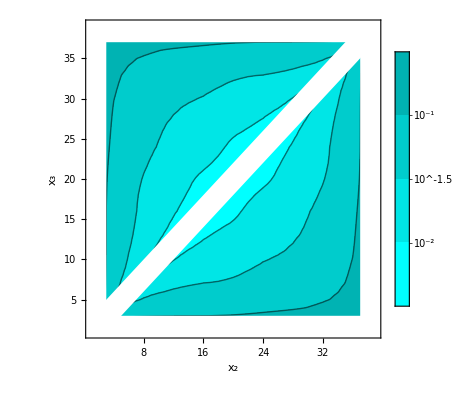

fig-eps-sig-sig-sample-10e5.pdf

```mathematica
L=40;
Table[{i,j,((L/π)Sin[20 π/L])^(-1/4)/0.2999304743017528 √(((L/π)Sin[20 π/L])^-2/0.0014561975206714428)measure0[[i,j,1]]},{i,1,39},{j,1,39}]//Flatten[#,1]&;
ListContourPlot[%,Contours->{10^-2,10^-1.5,10^-1(*,10^-0.5,1*)},PlotLegends->BarLegend[Automatic,All,"TickLabels"->(Superscript[10,#]&/@{-2,-1.5,-1})],FrameLabel->{"x_2","x_3"},ContourShading->Table[Darker[Cyan,i],{i,0,1,0.1}]];
Show[%,Graphics[{White,Rectangle[{0,0},{40,3}]}],Graphics[{White,Rectangle[{0,0},{3,40}]}],Graphics[{White,Rectangle[{0,37},{40,40}]}],Graphics[{White,Rectangle[{37,0},{40,40}]}],Graphics[{White,Polygon[{{0,2},{2,0},{52,50},{50,52}}]}]]
Export["fig-eps-sig-sig-sample-10e5.pdf",%]
```